```mathematica
Clear[tmax,n,nn,fnn,d1,d2a,d2b,d3a,d3b,vc,deqns,hrc1,rc,sd1,sd2,sd3,se2, se3,sn,sr, hr,L1,L2,L3,U1,U2,U3,hn,he2, he3,hd1,hd2,hd3,l1,l2,l3,u1,u2,u3,trans,transR,deqns,t,denominator,gwww,gwwt,gwwr,gwwr2,gwtw,gwtt,gwtr,gwtr2,gwrw,gwrt,gwrr,gwrr2,gwr2w,gwr2t,gwr2r,gwr2r2,gtww,gtwt,gtwr,gtwr2,gttw,gttt,gttr,gttr2,gtrw,gtrt,gtrr,gtrr2,gtr2w,gtr2t,gtr2r,gtr2r2,grww,grwt,grwr,grwr2,grtw,grtt,grtr,grtr2,grrw,grrt,grrr,grrr2,grr2w,grr2t,grr2r,grr2r2,gr2ww,gr2wt,gr2wr,gr2wr2,gr2tw,gr2tt,gr2tr,gr2tr2,gr2rw,gr2rt,gr2rr,gr2rr2,gr2r2w,gr2r2t,gr2r2r,gr2r2r2,a000,a002,a006,a001,a005,a004,a008,a003,a007,a009,a020,a022,a026,a021,a025,a024,a028,a023,a027,a029,a060,a062,a066,a061,a065,a064,a068,a063,a067,a069,a010,a012,a016,a011,a015,a014,a018,a013,a017,a019,a050,a052,a056,a051,a055,a054,a058,a053,a057,a059,a040,a042,a046,a041,a045,a044,a048,a043,a047,a049,a080,a082,a086,a081,a085,a084,a088,a083,a087,a089,a030,a032,a036,a031,a035,a034,a038,a033,a037,a039,a070,a072,a076,a071,a075,a074,a078,a073,a077,a079,a090,a092,a096,a091,a095,a094,a098,a093,a097,a099,a200,a202,a206,a201,a205,a204,a208,a203,a207,a209,a220,a222,a226,a221,a225,a224,a228,a223,a227,a229,a260,a262,a266,a261,a265,a264,a268,a263,a267,a269,a210,a212,a216,a211,a215,a214,a218,a213,a217,a219,a250,a252,a256,a251,a255,a254,a258,a253,a257,a259,a240,a242,a246,a241,a245,a244,a248,a243,a247,a249,a280,a282,a286,a281,a285,a284,a288,a283,a287,a289,a230,a232,a236,a231,a235,a234,a238,a233,a237,a239,a270,a272,a276,a271,a275,a274,a278,a273,a277,a279,a290,a292,a296,a291,a295,a294,a298,a293,a297,a299,a600,a602,a606,a601,a605,a604,a608,a603,a607,a609,a620,a622,a626,a621,a625,a624,a628,a623,a627,a629,a660,a662,a666,a661,a665,a664,a668,a663,a667,a669,a610,a612,a616,a611,a615,a614,a618,a613,a617,a619,a650,a652,a656,a651,a655,a654,a658,a653,a657,a659,a640,a642,a646,a641,a645,a644,a648,a643,a647,a649,a680,a682,a686,a681,a685,a684,a688,a683,a687,a689,a630,a632,a636,a631,a635,a634,a638,a633,a637,a639,a670,a672,a676,a671,a675,a674,a678,a673,a677,a679,a690,a692,a696,a691,a695,a694,a698,a693,a697,a699,a100,a102,a106,a101,a105,a104,a108,a103,a107,a109,a120,a122,a126,a121,a125,a124,a128,a123,a127,a129,a160,a162,a166,a161,a165,a164,a168,a163,a167,a169,a110,a112,a116,a111,a115,a114,a118,a113,a117,a119,a150,a152,a156,a151,a155,a154,a158,a153,a157,a159,a140,a142,a146,a141,a145,a144,a148,a143,a147,a149,a180,a182,a186,a181,a185,a184,a188,a183,a187,a189,a130,a132,a136,a131,a135,a134,a138,a133,a137,a139,a170,a172,a176,a171,a175,a174,a178,a173,a177,a179,a190,a192,a196,a191,a195,a194,a198,a193,a197,a199,a500,a502,a506,a501,a505,a504,a508,a503,a507,a509,a520,a522,a526,a521,a525,a524,a528,a523,a527,a529,a560,a562,a566,a561,a565,a564,a568,a563,a567,a569,a510,a512,a516,a511,a515,a514,a518,a513,a517,a519,a550,a552,a556,a551,a555,a554,a558,a553,a557,a559,a540,a542,a546,a541,a545,a544,a548,a543,a547,a549,a580,a582,a586,a581,a585,a584,a588,a583,a587,a589,a530,a532,a536,a531,a535,a534,a538,a533,a537,a539,a570,a572,a576,a571,a575,a574,a578,a573,a577,a579,a590,a592,a596,a591,a595,a594,a598,a593,a597,a599,a400,a402,a406,a401,a405,a404,a408,a403,a407,a409,a420,a422,a426,a421,a425,a424,a428,a423,a427,a429,a460,a462,a466,a461,a465,a464,a468,a463,a467,a469,a410,a412,a416,a411,a415,a414,a418,a413,a417,a419,a450,a452,a456,a451,a455,a454,a458,a453,a457,a459,a440,a442,a446,a441,a445,a444,a448,a443,a447,a449,a480,a482,a486,a481,a485,a484,a488,a483,a487,a489,a430,a432,a436,a431,a435,a434,a438,a433,a437,a439,a470,a472,a476,a471,a475,a474,a478,a473,a477,a479,a490,a492,a496,a491,a495,a494,a498,a493,a497,a499,a800,a802,a806,a801,a805,a804,a808,a803,a807,a809,a820,a822,a826,a821,a825,a824,a828,a823,a827,a829,a860,a862,a866,a861,a865,a864,a868,a863,a867,a869,a810,a812,a816,a811,a815,a814,a818,a813,a817,a819,a850,a852,a856,a851,a855,a854,a858,a853,a857,a859,a840,a842,a846,a841,a845,a844,a848,a843,a847,a849,a880,a882,a886,a881,a885,a884,a888,a883,a887,a889,a830,a832,a836,a831,a835,a834,a838,a833,a837,a839,a870,a872,a876,a871,a875,a874,a878,a873,a877,a879,a890,a892,a896,a891,a895,a894,a898,a893,a897,a899,a300,a302,a306,a301,a305,a304,a308,a303,a307,a309,a320,a322,a326,a321,a325,a324,a328,a323,a327,a329,a360,a362,a366,a361,a365,a364,a368,a363,a367,a369,a310,a312,a316,a311,a315,a314,a318,a313,a317,a319,a350,a352,a356,a351,a355,a354,a358,a353,a357,a359,a340,a342,a346,a341,a345,a344,a348,a343,a347,a349,a380,a382,a386,a381,a385,a384,a388,a383,a387,a389,a330,a332,a336,a331,a335,a334,a338,a333,a337,a339,a370,a372,a376,a371,a375,a374,a378,a373,a377,a379,a390,a392,a396,a391,a395,a394,a398,a393,a397,a399,a700,a702,a706,a701,a705,a704,a708,a703,a707,a709,a720,a722,a726,a721,a725,a724,a728,a723,a727,a729,a760,a762,a766,a761,a765,a764,a768,a763,a767,a769,a710,a712,a716,a711,a715,a714,a718,a713,a717,a719,a750,a752,a756,a751,a755,a754,a758,a753,a757,a759,a740,a742,a746,a741,a745,a744,a748,a743,a747,a749,a780,a782,a786,a781,a785,a784,a788,a783,a787,a789,a730,a732,a736,a731,a735,a734,a738,a733,a737,a739,a770,a772,a776,a771,a775,a774,a778,a773,a777,a779,a790,a792,a796,a791,a795,a794,a798,a793,a797,a799,a900,a902,a906,a901,a905,a904,a908,a903,a907,a909,a920,a922,a926,a921,a925,a924,a928,a923,a927,a929,a960,a962,a966,a961,a965,a964,a968,a963,a967,a969,a910,a912,a916,a911,a915,a914,a918,a913,a917,a919,a950,a952,a956,a951,a955,a954,a958,a953,a957,a959,a940,a942,a946,a941,a945,a944,a948,a943,a947,a949,a980,a982,a986,a981,a985,a984,a988,a983,a987,a989,a930,a932,a936,a931,a935,a934,a938,a933,a937,a939,a970,a972,a976,a971,a975,a974,a978,a973,a977,a979,a990,a992,a996,a991,a995,a994,a998,a993,a997,a999,f000,f002,f006,f001,f005,f004,f008,f003,f007,f009,f020,f022,f026,f021,f025,f024,f028,f023,f027,f029,f060,f062,f066,f061,f065,f064,f068,f063,f067,f069,f010,f012,f016,f011,f015,f014,f018,f013,f017,f019,f050,f052,f056,f051,f055,f054,f058,f053,f057,f059,f040,f042,f046,f041,f045,f044,f048,f043,f047,f049,f080,f082,f086,f081,f085,f084,f088,f083,f087,f089,f030,f032,f036,f031,f035,f034,f038,f033,f037,f039,f070,f072,f076,f071,f075,f074,f078,f073,f077,f079,f090,f092,f096,f091,f095,f094,f098,f093,f097,f099,f200,f202,f206,f201,f205,f204,f208,f203,f207,f209,f220,f222,f226,f221,f225,f224,f228,f223,f227,f229,f260,f262,f266,f261,f265,f264,f268,f263,f267,f269,f210,f212,f216,f211,f215,f214,f218,f213,f217,f219,f250,f252,f256,f251,f255,f254,f258,f253,f257,f259,f240,f242,f246,f241,f245,f244,f248,f243,f247,f249,f280,f282,f286,f281,f285,f284,f288,f283,f287,f289,f230,f232,f236,f231,f235,f234,f238,f233,f237,f239,f270,f272,f276,f271,f275,f274,f278,f273,f277,f279,f290,f292,f296,f291,f295,f294,f298,f293,f297,f299,f600,f602,f606,f601,f605,f604,f608,f603,f607,f609,f620,f622,f626,f621,f625,f624,f628,f623,f627,f629,f660,f662,f666,f661,f665,f664,f668,f663,f667,f669,f610,f612,f616,f611,f615,f614,f618,f613,f617,f619,f650,f652,f656,f651,f655,f654,f658,f653,f657,f659,f640,f642,f646,f641,f645,f644,f648,f643,f647,f649,f680,f682,f686,f681,f685,f684,f688,f683,f687,f689,f630,f632,f636,f631,f635,f634,f638,f633,f637,f639,f670,f672,f676,f671,f675,f674,f678,f673,f677,f679,f690,f692,f696,f691,f695,f694,f698,f693,f697,f699,f100,f102,f106,f101,f105,f104,f108,f103,f107,f109,f120,f122,f126,f121,f125,f124,f128,f123,f127,f129,f160,f162,f166,f161,f165,f164,f168,f163,f167,f169,f110,f112,f116,f111,f115,f114,f118,f113,f117,f119,f150,f152,f156,f151,f155,f154,f158,f153,f157,f159,f140,f142,f146,f141,f145,f144,f148,f143,f147,f149,f180,f182,f186,f181,f185,f184,f188,f183,f187,f189,f130,f132,f136,f131,f135,f134,f138,f133,f137,f139,f170,f172,f176,f171,f175,f174,f178,f173,f177,f179,f190,f192,f196,f191,f195,f194,f198,f193,f197,f199,f500,f502,f506,f501,f505,f504,f508,f503,f507,f509,f520,f522,f526,f521,f525,f524,f528,f523,f527,f529,f560,f562,f566,f561,f565,f564,f568,f563,f567,f569,f510,f512,f516,f511,f515,f514,f518,f513,f517,f519,f550,f552,f556,f551,f555,f554,f558,f553,f557,f559,f540,f542,f546,f541,f545,f544,f548,f543,f547,f549,f580,f582,f586,f581,f585,f584,f588,f583,f587,f589,f530,f532,f536,f531,f535,f534,f538,f533,f537,f539,f570,f572,f576,f571,f575,f574,f578,f573,f577,f579,f590,f592,f596,f591,f595,f594,f598,f593,f597,f599,f400,f402,f406,f401,f405,f404,f408,f403,f407,f409,f420,f422,f426,f421,f425,f424,f428,f423,f427,f429,f460,f462,f466,f461,f465,f464,f468,f463,f467,f469,f410,f412,f416,f411,f415,f414,f418,f413,f417,f419,f450,f452,f456,f451,f455,f454,f458,f453,f457,f459,f440,f442,f446,f441,f445,f444,f448,f443,f447,f449,f480,f482,f486,f481,f485,f484,f488,f483,f487,f489,f430,f432,f436,f431,f435,f434,f438,f433,f437,f439,f470,f472,f476,f471,f475,f474,f478,f473,f477,f479,f490,f492,f496,f491,f495,f494,f498,f493,f497,f499,f800,f802,f806,f801,f805,f804,f808,f803,f807,f809,f820,f822,f826,f821,f825,f824,f828,f823,f827,f829,f860,f862,f866,f861,f865,f864,f868,f863,f867,f869,f810,f812,f816,f811,f815,f814,f818,f813,f817,f819,f850,f852,f856,f851,f855,f854,f858,f853,f857,f859,f840,f842,f846,f841,f845,f844,f848,f843,f847,f849,f880,f882,f886,f881,f885,f884,f888,f883,f887,f889,f830,f832,f836,f831,f835,f834,f838,f833,f837,f839,f870,f872,f876,f871,f875,f874,f878,f873,f877,f879,f890,f892,f896,f891,f895,f894,f898,f893,f897,f899,f300,f302,f306,f301,f305,f304,f308,f303,f307,f309,f320,f322,f326,f321,f325,f324,f328,f323,f327,f329,f360,f362,f366,f361,f365,f364,f368,f363,f367,f369,f310,f312,f316,f311,f315,f314,f318,f313,f317,f319,f350,f352,f356,f351,f355,f354,f358,f353,f357,f359,f340,f342,f346,f341,f345,f344,f348,f343,f347,f349,f380,f382,f386,f381,f385,f384,f388,f383,f387,f389,f330,f332,f336,f331,f335,f334,f338,f333,f337,f339,f370,f372,f376,f371,f375,f374,f378,f373,f377,f379,f390,f392,f396,f391,f395,f394,f398,f393,f397,f399,f700,f702,f706,f701,f705,f704,f708,f703,f707,f709,f720,f722,f726,f721,f725,f724,f728,f723,f727,f729,f760,f762,f766,f761,f765,f764,f768,f763,f767,f769,f710,f712,f716,f711,f715,f714,f718,f713,f717,f719,f750,f752,f756,f751,f755,f754,f758,f753,f757,f759,f740,f742,f746,f741,f745,f744,f748,f743,f747,f749,f780,f782,f786,f781,f785,f784,f788,f783,f787,f789,f730,f732,f736,f731,f735,f734,f738,f733,f737,f739,f770,f772,f776,f771,f775,f774,f778,f773,f777,f779,f790,f792,f796,f791,f795,f794,f798,f793,f797,f799,f900,f902,f906,f901,f905,f904,f908,f903,f907,f909,f920,f922,f926,f921,f925,f924,f928,f923,f927,f929,f960,f962,f966,f961,f965,f964,f968,f963,f967,f969,f910,f912,f916,f911,f915,f914,f918,f913,f917,f919,f950,f952,f956,f951,f955,f954,f958,f953,f957,f959,f940,f942,f946,f941,f945,f944,f948,f943,f947,f949,f980,f982,f986,f981,f985,f984,f988,f983,f987,f989,f930,f932,f936,f931,f935,f934,f938,f933,f937,f939,f970,f972,f976,f971,f975,f974,f978,f973,f977,f979,f990,f992,f996,f991,f995,f994,f998,f993,f997,f999,propGametes,gametes,adults,fitnesses,ee0,cc0,dd0,hrc2,hrc3,t]
ClearAll["Global`*"]

Matrix Generation
```

Generation Matrix

```mathematica
trans={{X,"w/w/w","w/w/t","w/w/r2","w/w/r","w/t/w","w/t/t","w/t/r2","w/t/r","w/r2/w","w/r2/t","w/r2/r2","w/r2/r","w/r/w","w/r/t","w/r/r2","w/r/r","t/w/w","t/w/t","t/w/r2","t/w/r","t/t/w","t/t/t","t/t/r2","t/t/r","t/r2/w","t/r2/t","t/r2/r2","t/r2/r","t/r/w","t/r/t","t/r/r2","t/r/r","r2/w/w","r2/w/t","r2/w/r2","r2/w/r","r2/t/w","r2/t/t","r2/t/r2","r2/t/r","r2/r2/w","r2/r2/t","r2/r2/r2","r2/r2/r","r2/r/w","r2/r/t","r2/r/r2","r2/r/r","r/w/w","r/w/t","r/w/r2","r/w/r","r/t/w","r/t/t","r/t/r2","r/t/r","r/r2/w","r/r2/t","r/r2/r2","r/r2/r","r/r/w","r/r/t","r/r/r2","r/r/r"},

{"ww/ww/ww",1*1*1,1*1*0,1*1*0,1*1*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/ww/wt",1*1*0.5,1*1*0.5,1*1*0,1*1*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/ww/wr2",1*1*0.5,1*1*0,1*1*0.5,1*1*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/ww/wr",1*1*0.5,1*1*0,1*1*0,1*1*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/ww/tt",1*1*0,1*1*1,1*1*0,1*1*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/ww/rt",1*1*0,1*1*0.5,1*1*0,1*1*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/ww/rr2",1*1*0,1*1*0,1*1*0.5,1*1*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/ww/rr",1*1*0,1*1*0,1*1*0,1*1*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/ww/r2t",1*1*0,1*1*0.5,1*1*0.5,1*1*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/ww/r2r2",1*1*0,1*1*0,1*1*1,1*1*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0},{"ww/wt/ww",1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/wt/wt",1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/wt/wr2",1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/wt/wr",1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/wt/tt",1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/wt/rt",1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/wt/rr2",1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/wt/rr",1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/wt/r2t",1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/wt/r2r2",1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0},{"ww/wr2/ww",1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/wr2/wt",1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/wr2/wr2",1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/wr2/wr",1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/wr2/tt",1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/wr2/rt",1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/wr2/rr2",1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/wr2/rr",1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/wr2/r2t",1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/wr2/r2r2",1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0},{"ww/wr/ww",1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0},{"ww/wr/wt",1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0},{"ww/wr/wr2",1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0},{"ww/wr/wr",1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5},{"ww/wr/tt",1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0},{"ww/wr/rt",1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5},{"ww/wr/rr2",1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5},{"ww/wr/rr",1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1},{"ww/wr/r2t",1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0},{"ww/wr/r2r2",1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0},{"ww/tt/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*1*1,1*1*0,1*1*0,1*1*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/tt/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*1*0.5,1*1*0.5,1*1*0,1*1*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/tt/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*1*0.5,1*1*0,1*1*0.5,1*1*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/tt/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*1*0.5,1*1*0,1*1*0,1*1*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/tt/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*1*0,1*1*1,1*1*0,1*1*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/tt/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*1*0,1*1*0.5,1*1*0,1*1*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/tt/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*1*0,1*1*0,1*1*0.5,1*1*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/tt/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*1*0,1*1*0,1*1*0,1*1*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/tt/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*1*0,1*1*0.5,1*1*0.5,1*1*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/tt/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*1*0,1*1*0,1*1*1,1*1*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0},{"ww/rt/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0},{"ww/rt/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0},{"ww/rt/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0},{"ww/rt/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5},{"ww/rt/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0},{"ww/rt/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5},{"ww/rt/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5},{"ww/rt/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1},{"ww/rt/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0},{"ww/rt/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0},{"ww/rr2/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0},{"ww/rr2/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0},{"ww/rr2/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0},{"ww/rr2/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5},{"ww/rr2/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0},{"ww/rr2/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5},{"ww/rr2/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5},{"ww/rr2/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1},{"ww/rr2/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0},{"ww/rr2/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0},{"ww/rr/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*1*1,1*1*0,1*1*0,1*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0},{"ww/rr/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*1*0.5,1*1*0.5,1*1*0,1*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0},{"ww/rr/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*1*0.5,1*1*0,1*1*0.5,1*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0},{"ww/rr/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*1*0.5,1*1*0,1*1*0,1*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5},{"ww/rr/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*1*0,1*1*1,1*1*0,1*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0},{"ww/rr/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*1*0,1*1*0.5,1*1*0,1*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5},{"ww/rr/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*1*0,1*1*0,1*1*0.5,1*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5},{"ww/rr/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*1*0,1*1*0,1*1*0,1*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1},{"ww/rr/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*1*0,1*1*0.5,1*1*0.5,1*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0},{"ww/rr/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*1*0,1*1*0,1*1*1,1*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0},{"ww/r2t/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0*1,1*0*0,1*0*0,1*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/r2t/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/r2t/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/r2t/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/r2t/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0*0,1*0*1,1*0*0,1*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/r2t/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0.5*0,1*0.5*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0.5*0,0*0.5*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/r2t/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/r2t/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0*0,1*0*0,1*0*0,1*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/r2t/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0.5*0,1*0.5*0.5,1*0.5*0.5,1*0.5*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0.5*0,0*0.5*0.5,0*0.5*0.5,0*0.5*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/r2t/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0.5*0,1*0.5*0,1*0.5*1,1*0.5*0,1*0*0,1*0*0,1*0*1,1*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0.5*0,0*0.5*0,0*0.5*1,0*0.5*0,0*0*0,0*0*0,0*0*1,0*0*0},{"ww/r2r2/ww",1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*1*1,1*1*0,1*1*0,1*1*0,1*0*1,1*0*0,1*0*0,1*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*1*1,0*1*0,0*1*0,0*1*0,0*0*1,0*0*0,0*0*0,0*0*0},{"ww/r2r2/wt",1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*1*0.5,1*1*0.5,1*1*0,1*1*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*1*0.5,0*1*0.5,0*1*0,0*1*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0},{"ww/r2r2/wr2",1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*1*0.5,1*1*0,1*1*0.5,1*1*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*1*0.5,0*1*0,0*1*0.5,0*1*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0},{"ww/r2r2/wr",1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*1*0.5,1*1*0,1*1*0,1*1*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*1*0.5,0*1*0,0*1*0,0*1*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5},{"ww/r2r2/tt",1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*1*0,1*1*1,1*1*0,1*1*0,1*0*0,1*0*1,1*0*0,1*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*1*0,0*1*1,0*1*0,0*1*0,0*0*0,0*0*1,0*0*0,0*0*0},{"ww/r2r2/rt",1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,1*1*0,1*1*0.5,1*1*0,1*1*0.5,1*0*0,1*0*0.5,1*0*0,1*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5,0*1*0,0*1*0.5,0*1*0,0*1*0.5,0*0*0,0*0*0.5,0*0*0,0*0*0.5},{"ww/r2r2/rr2",1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*1*0,1*1*0,1*1*0.5,1*1*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*1*0,0*1*0,0*1*0.5,0*1*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5},{"ww/r2r2/rr",1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*1*0,1*1*0,1*1*0,1*1*1,1*0*0,1*0*0,1*0*0,1*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*1*0,0*1*0,0*1*0,0*1*1,0*0*0,0*0*0,0*0*0,0*0*1},{"ww/r2r2/r2t",1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,1*1*0,1*1*0.5,1*1*0.5,1*1*0,1*0*0,1*0*0.5,1*0*0.5,1*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0,0*1*0,0*1*0.5,0*1*0.5,0*1*0,0*0*0,0*0*0.5,0*0*0.5,0*0*0},{"ww/r2r2/r2r2",1*0*0,1*0*0,1*0*1,1*0*0,1*0*0,1*0*0,1*0*1,1*0*0,1*1*0,1*1*0,1*1*1,1*1*0,1*0*0,1*0*0,1*0*1,1*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*0*0,0*0*0,0*0*1,0*0*0,0*1*0,0*1*0,0*1*1,0*1*0,0*0*0,0*0*0,0*0*1,0*0*0},{"wt/ww/ww",(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/ww/wt",(1-d1)(1-u1-U1)*1*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*1*d3a(1-l3-L3),(1-d1)(1-u1-U1)*1*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*1*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*1*(1-d3a)(1-u3-U3),d1(1-l1-L1)*1*d3a(1-l3-L3),d1(1-l1-L1)*1*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*1*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*1*d3a(1-l3-L3),(d1*L1+U1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*1*d3a(1-l3-L3),(d1*l1+u1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a))},{"wt/ww/wr2",(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/ww/wr",(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/ww/tt",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/ww/rt",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/ww/rr2",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5},{"wt/ww/rr",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1},{"wt/ww/r2t",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/ww/r2r2",(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0},{"wt/wt/ww",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*1,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*1,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*1,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*1,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*1,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*1,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*1,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*1,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0},{"wt/wt/wt",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*d3a(1-l3-L3),(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*d2a(1-l2-L2)*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*d2a(1-l2-L2)*d3a(1-l3-L3),(1-d1)(1-u1-U1)*d2a(1-l2-L2)*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*d2a(1-l2-L2)*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*d3a(1-l3-L3),(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*d3a(1-l3-L3),(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*(1-d2a)(1-u2-U2)*(1-d3a)(1-u3-U3),d1(1-l1-L1)*(1-d2a)(1-u2-U2)*d3a(1-l3-L3),d1(1-l1-L1)*(1-d2a)(1-u2-U2)*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*(1-d2a)(1-u2-U2)*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*d2a(1-l2-L2)*(1-d3a)(1-u3-U3),d1(1-l1-L1)*d2a(1-l2-L2)*d3a(1-l3-L3),d1(1-l1-L1)*d2a(1-l2-L2)*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*d2a(1-l2-L2)*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*(1-d3a)(1-u3-U3),d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*d3a(1-l3-L3),d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*(1-d3a)(1-u3-U3),d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*d3a(1-l3-L3),d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*d3a(1-l3-L3),(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*d2a(1-l2-L2)*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*d2a(1-l2-L2)*d3a(1-l3-L3),(d1*L1+U1(1-d1))*d2a(1-l2-L2)*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*d2a(1-l2-L2)*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*d3a(1-l3-L3),(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*d3a(1-l3-L3),(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*d3a(1-l3-L3),(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*d2a(1-l2-L2)*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*d2a(1-l2-L2)*d3a(1-l3-L3),(d1*l1+u1(1-d1))*d2a(1-l2-L2)*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*d2a(1-l2-L2)*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*d3a(1-l3-L3),(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*d3a(1-l3-L3),(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*(d3a*l3+u3(1-d3a))},{"wt/wt/wr2",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0},{"wt/wt/wr",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5},{"wt/wt/tt",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*1,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*1,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*1,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*1,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*1,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*1,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*1,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*1,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0},{"wt/wt/rt",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5},{"wt/wt/rr2",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5},{"wt/wt/rr",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*1,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*1,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*1,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*1,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*1,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*1,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*1,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*1,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*1,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*1},{"wt/wt/r2t",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0.5,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0.5,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0.5,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0.5,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0.5,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0.5,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0.5,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0.5,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0.5,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0.5,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0},{"wt/wt/r2r2",(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*1,(1-d1)(1-u1-U1)*(1-d2a)(1-u2-U2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*1,(1-d1)(1-u1-U1)*d2a(1-l2-L2)*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*L2+U2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*1,(1-d1)(1-u1-U1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*1,d1(1-l1-L1)*(1-d2a)(1-u2-U2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*d2a(1-l2-L2)*1,d1(1-l1-L1)*d2a(1-l2-L2)*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*1,d1(1-l1-L1)*(d2a*L2+U2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*1,d1(1-l1-L1)*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*L1+U1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*1,(d1*L1+U1(1-d1))*d2a(1-l2-L2)*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*L1+U1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*1,(d1*l1+u1(1-d1))*(1-d2a)(1-u2-U2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*1,(d1*l1+u1(1-d1))*d2a(1-l2-L2)*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*L2+U2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*1,(d1*l1+u1(1-d1))*(d2a*l2+u2(1-d2a))*0},{"wt/wr2/ww",(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/wr2/wt",(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a))},{"wt/wr2/wr2",(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/wr2/wr",(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/wr2/tt",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/wr2/rt",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/wr2/rr2",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5},{"wt/wr2/rr",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1},{"wt/wr2/r2t",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/wr2/r2r2",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0},{"wt/wr/ww",(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/wr/wt",(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a))},{"wt/wr/wr2",(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/wr/wr",(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/wr/tt",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/wr/rt",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/wr/rr2",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/wr/rr",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1},{"wt/wr/r2t",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/wr/r2r2",(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0},{"wt/tt/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/tt/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*1*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*1*d3a(1-l3-L3),(1-d1)(1-u1-U1)*1*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*1*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*1*(1-d3a)(1-u3-U3),d1(1-l1-L1)*1*d3a(1-l3-L3),d1(1-l1-L1)*1*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*1*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*1*d3a(1-l3-L3),(d1*L1+U1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*1*d3a(1-l3-L3),(d1*l1+u1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a))},{"wt/tt/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/tt/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/tt/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/tt/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/tt/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5},{"wt/tt/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1},{"wt/tt/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/tt/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0},{"wt/rt/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/rt/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a))},{"wt/rt/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/rt/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rt/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/rt/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rt/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rt/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1},{"wt/rt/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/rt/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr2/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr2/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a))},{"wt/rr2/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr2/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rr2/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr2/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rr2/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5},{"wt/rr2/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1},{"wt/rr2/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr2/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0},{"wt/rr/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0},{"wt/rr/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*1*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*1*d3a(1-l3-L3),(1-d1)(1-u1-U1)*1*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*1*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*1*(1-d3a)(1-u3-U3),d1(1-l1-L1)*1*d3a(1-l3-L3),d1(1-l1-L1)*1*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*1*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*1*d3a(1-l3-L3),(d1*L1+U1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*1*d3a(1-l3-L3),(d1*l1+u1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*1*(d3a*l3+u3(1-d3a))},{"wt/rr/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0},{"wt/rr/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5},{"wt/rr/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0},{"wt/rr/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5},{"wt/rr/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5},{"wt/rr/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1},{"wt/rr/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0},{"wt/rr/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0},{"wt/r2t/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/r2t/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0.5*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0.5*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0.5*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0.5*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0.5*d3a(1-l3-L3),d1(1-l1-L1)*0.5*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0.5*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0.5*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0.5*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0.5*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0.5*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a))},{"wt/r2t/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/r2t/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2t/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/r2t/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2t/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2t/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1},{"wt/r2t/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0.5,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0.5,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0.5,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0.5,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/r2t/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0.5*1,(1-d1)(1-u1-U1)*0.5*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0.5*1,d1(1-l1-L1)*0.5*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0.5*1,(d1*L1+U1(1-d1))*0.5*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0.5*1,(d1*l1+u1(1-d1))*0.5*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0},{"wt/r2r2/ww",(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/r2r2/wt",(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*1*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*1*d3a(1-l3-L3),(1-d1)(1-u1-U1)*1*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*1*(d3a*l3+u3(1-d3a)),(1-d1)(1-u1-U1)*0*(1-d3a)(1-u3-U3),(1-d1)(1-u1-U1)*0*d3a(1-l3-L3),(1-d1)(1-u1-U1)*0*(d3a*L3+U3(1-d3a)),(1-d1)(1-u1-U1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*1*(1-d3a)(1-u3-U3),d1(1-l1-L1)*1*d3a(1-l3-L3),d1(1-l1-L1)*1*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*1*(d3a*l3+u3(1-d3a)),d1(1-l1-L1)*0*(1-d3a)(1-u3-U3),d1(1-l1-L1)*0*d3a(1-l3-L3),d1(1-l1-L1)*0*(d3a*L3+U3(1-d3a)),d1(1-l1-L1)*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*1*d3a(1-l3-L3),(d1*L1+U1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*L1+U1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*L1+U1(1-d1))*0*d3a(1-l3-L3),(d1*L1+U1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*L1+U1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*1*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*1*d3a(1-l3-L3),(d1*l1+u1(1-d1))*1*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*1*(d3a*l3+u3(1-d3a)),(d1*l1+u1(1-d1))*0*(1-d3a)(1-u3-U3),(d1*l1+u1(1-d1))*0*d3a(1-l3-L3),(d1*l1+u1(1-d1))*0*(d3a*L3+U3(1-d3a)),(d1*l1+u1(1-d1))*0*(d3a*l3+u3(1-d3a))},{"wt/r2r2/wr2",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/r2r2/wr",(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2r2/tt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0},{"wt/r2r2/rt",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2r2/rr2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5},{"wt/r2r2/rr",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1},{"wt/r2r2/r2t",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0.5,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0.5,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0.5,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0.5,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0.5,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0.5,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0.5,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0.5,(d1*l1+u1(1-d1))*0*0},{"wt/r2r2/r2r2",(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*1*1,(1-d1)(1-u1-U1)*1*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*0,(1-d1)(1-u1-U1)*0*1,(1-d1)(1-u1-U1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*0,d1(1-l1-L1)*1*1,d1(1-l1-L1)*1*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*0,d1(1-l1-L1)*0*1,d1(1-l1-L1)*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*1*1,(d1*L1+U1(1-d1))*1*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*0,(d1*L1+U1(1-d1))*0*1,(d1*L1+U1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*1*1,(d1*l1+u1(1-d1))*1*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*0,(d1*l1+u1(1-d1))*0*1,(d1*l1+u1(1-d1))*0*0},{"wr2/ww/ww",0.5*1*1,0.5*1*0,0.5*1*0,0.5*1*0,0.5*0*1,0.5*0*0,0.5*0*0,0.5*0*0,0.5*0*1,0.5*0*0,0.5*0*0,0.5*0*0,0.5*0*1,0.5*0*0,0.5*0*0,0.5*0*0,0*1*1,
```

1
 |  |  |  |

{1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1,1,1.,1.,1,1.,1.,1,1.,1,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1,1.,1.,1.,1,1.,1.,1,1.,1}

#### Solve Differential Equations Model parameters;

```mathematica
d1=.99; (*Transmission rate of drive (locus 1) *)
d2a=.99;(*Transmission rate of drive (locus 2) if drive component present in heterozygosity*)
d2b=.99;(*Transmission rate of drive (locus 2) if drive component present in homozygosity*)
d3a = .99; (*Transmission rate of drive (locus 3) if drive component present in heterozygosity*)
d3b =.99;(*Transmission rate of drive (locus 3) if drive component present in homozygosity*)


hrc1=1;(*Dominance coef.for refractoriness (1 effector allele)*)
hrc2 =1; (*Dominance coef.for refractoriness (2 effector alleles)*)
hrc3 =1; (*Dominance coef.for refractoriness (3 effector alleles)*)
rc=1; (*Homozygous degree of refractoriness*)

tmax=350; (*maximum time in generations*)

cc0=.0001;(*Initial release frequency of homozygous drive and effector construct*)
ee0=.000;(*Initial release frequency of homozygous effector construct*)
dd0=.000;(*Initial release frequency of homozygous drive construct*)

sr =1.0;(*Cost of loss of gene function*)
hr= 0.2;(*Dominance coef.for loss of gene function*)
sd1=.0; (*Cost of hijacking target locus 1 (Drive)*)
sd2=.0; (*Cost of hijacking target locus 2 (Effector)*)
sd3 =.0; (*Cost of hijacking target locus 3 (Effector)*)
sn=.05; (*Cost of expressing nuclease at locus 1*)
se2 = .1; (*Cost of expressing effector at locus 2*)
se3= .1; (*Cost of expressing effector at locus 3*)
hd1=1/2;(*Dominance coef.for disruption at locus 1*)
hd2=1/2;(*Dominance coef.for disruption at locus 2*)
hd3 = 1/2;(*Dominance coef.for disruption at locus 3*)
hn=1/2;(*Dominance coef.for expressing nuclease*)
he2=1/2;(*Dominance coef.for expressing effector (locus 2)*)
he3 = 1/2; (*Dominance coef.for expressing effector (locus 3)*)
l1 = .0001*(1/3);(*Resistance arising from HR at locus 1*)
l2 = .0001*(1/3);(*Resistance arising from HR at locus 2*)
l3 = .0001*(1/3);(*Resistance arising from HR at locus 3*)
u1 = .5*(1/3);(*Resistance arising from NHEJ at locus 1*)
u2 = .5*(1/3);(*Resistance arising from NHEJ at locus 2*)
u3 = .5*(1/3);(*Resistance arising from NHEJ at locus 3*)
L1=0.0001 *(2/3);(*Loss of gene function arising from HR at locus 1*)
L2=0.0001*(2/3);(*Loss of gene function arising from HR at locus 2*)
L3=0.0001*(2/3);(*Loss of gene function arising from HR at locus 3*)
U1=0.5 *(2/3);
(*Loss of gene function arising from NHEJ at locus 1*)
U2=0.5 *(2/3);(*Loss of gene function arising from NHEJ at locus 2*)
U3=0.5*(2/3);(*Loss of gene function arising from NHEJ at locus 3*)

(*Clarification of alleles
w - wild-type
t - transgene (effector or drive)
r1 - resistance
r2 - loss of function resistance (described in paper as 'm')
*)

(*Clarification of genotype codes
Each genotype is represented in terms of its genotype by a code of format a###,
where # is a number between 0-9. 
0 - ww
1 - wr
2 - wt
3 - rr
4 - rt
5 - tt
6 - wr2
7 - r2t
8 - rr2
9 - r2r2
Each position represents a locus. E.g a005, is a genotype which is wild type at loci 1 and 2, and homozygous for a transgene at locus 3*)
```

```mathematica
Fitnesses;
```

```mathematica
f000=1*1*1

f002=1*1*(1-hd3*sd3)(1-he3*se3)

f006=1*1*(1-sr*hr)

f001=1*1*1

f005=1*1*(1-sd3) (1-se3)

f004=1*1*(1-hd3*sd3)(1-he3*se3)

f008=1*1*(1-sr*hr)

f003=1*1*1

f007=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f009=1*1*(1-sr)

f020=1*(1-hd2*sd2)(1-he2*se2)*1

f022=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f026=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f021=1*(1-hd2*sd2)(1-he2*se2)*1

f025=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f024=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f028=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f023=1*(1-hd2*sd2)(1-he2*se2)*1

f027=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f029=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f060=1*(1-sr*hr)*1

f062=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f066=1*(1-sr*hr)*(1-sr*hr)

f061=1*(1-sr*hr)*1

f065=1*(1-sr*hr)*(1-sd3) (1-se3)

f064=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f068=1*(1-sr*hr)*(1-sr*hr)

f063=1*(1-sr*hr)*1

f067=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f069=1*(1-sr*hr)*(1-sr)

f010=1*1*1

f012=1*1*(1-hd3*sd3)(1-he3*se3)

f016=1*1*(1-sr*hr)

f011=1*1*1

f015=1*1*(1-sd3) (1-se3)

f014=1*1*(1-hd3*sd3)(1-he3*se3)

f018=1*1*(1-sr*hr)

f013=1*1*1

f017=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f019=1*1*(1-sr)

f050=1*(1-sd2) (1-se2)*1

f052=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f056=1*(1-sd2) (1-se2)*(1-sr*hr)

f051=1*(1-sd2) (1-se2)*1

f055=1*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f054=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f058=1*(1-sd2) (1-se2)*(1-sr*hr)

f053=1*(1-sd2) (1-se2)*1

f057=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f059=1*(1-sd2) (1-se2)*(1-sr)

f040=1*(1-hd2*sd2)(1-he2*se2)*1

f042=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f046=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f041=1*(1-hd2*sd2)(1-he2*se2)*1

f045=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f044=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f048=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f043=1*(1-hd2*sd2)(1-he2*se2)*1

f047=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f049=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f080=1*(1-sr*hr)*1

f082=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f086=1*(1-sr*hr)*(1-sr*hr)

f081=1*(1-sr*hr)*1

f085=1*(1-sr*hr)*(1-sd3) (1-se3)

f084=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f088=1*(1-sr*hr)*(1-sr*hr)

f083=1*(1-sr*hr)*1

f087=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f089=1*(1-sr*hr)*(1-sr)

f030=1*1*1

f032=1*1*(1-hd3*sd3)(1-he3*se3)

f036=1*1*(1-sr*hr)

f031=1*1*1

f035=1*1*(1-sd3) (1-se3)

f034=1*1*(1-hd3*sd3)(1-he3*se3)

f038=1*1*(1-sr*hr)

f033=1*1*1

f037=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f039=1*1*(1-sr)

f070=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f072=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f076=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f071=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f075=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f074=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f078=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f073=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f077=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f079=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f090=1*(1-sr)*1

f092=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f096=1*(1-sr)*(1-sr*hr)

f091=1*(1-sr)*1

f095=1*(1-sr)*(1-sd3) (1-se3)

f094=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f098=1*(1-sr)*(1-sr*hr)

f093=1*(1-sr)*1

f097=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f099=1*(1-sr)*(1-sr)

f200=(1-hd1*sd1)(1-hn*sn)*1*1

f202=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f206=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f201=(1-hd1*sd1)(1-hn*sn)*1*1

f205=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f204=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f208=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f203=(1-hd1*sd1)(1-hn*sn)*1*1

f207=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f209=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f220=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f222=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f226=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f221=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f225=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f224=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f228=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f223=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f227=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f229=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f260=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f262=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f266=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f261=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f265=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sd3) (1-se3)

f264=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f268=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f263=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f267=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f269=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr)

f210=(1-hd1*sd1)(1-hn*sn)*1*1

f212=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f216=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f211=(1-hd1*sd1)(1-hn*sn)*1*1

f215=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f214=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f218=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f213=(1-hd1*sd1)(1-hn*sn)*1*1

f217=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f219=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f250=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f252=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f256=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr*hr)

f251=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f255=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f254=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f258=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr*hr)

f253=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f257=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f259=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr)

f240=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f242=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f246=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f241=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f245=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f244=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f248=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f243=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f247=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f249=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f280=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f282=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f286=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f281=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f285=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sd3) (1-se3)

f284=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f288=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f283=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f287=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f289=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr)

f230=(1-hd1*sd1)(1-hn*sn)*1*1

f232=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f236=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f231=(1-hd1*sd1)(1-hn*sn)*1*1

f235=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f234=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f238=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f233=(1-hd1*sd1)(1-hn*sn)*1*1

f237=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f239=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f270=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f272=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f276=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f271=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f275=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f274=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f278=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f273=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f277=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f279=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f290=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f292=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f296=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr*hr)

f291=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f295=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sd3) (1-se3)

f294=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f298=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr*hr)

f293=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f297=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f299=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr)

f600=(1-sr*hr)*1*1

f602=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f606=(1-sr*hr)*1*(1-sr*hr)

f601=(1-sr*hr)*1*1

f605=(1-sr*hr)*1*(1-sd3) (1-se3)

f604=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f608=(1-sr*hr)*1*(1-sr*hr)

f603=(1-sr*hr)*1*1

f607=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f609=(1-sr*hr)*1*(1-sr)

f620=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f622=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f626=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f621=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f625=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f624=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f628=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f623=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f627=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f629=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f660=(1-sr*hr)*(1-sr*hr)*1

f662=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f666=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f661=(1-sr*hr)*(1-sr*hr)*1

f665=(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f664=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f668=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f663=(1-sr*hr)*(1-sr*hr)*1

f667=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f669=(1-sr*hr)*(1-sr*hr)*(1-sr)

f610=(1-sr*hr)*1*1

f612=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f616=(1-sr*hr)*1*(1-sr*hr)

f611=(1-sr*hr)*1*1

f615=(1-sr*hr)*1*(1-sd3) (1-se3)

f614=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f618=(1-sr*hr)*1*(1-sr*hr)

f613=(1-sr*hr)*1*1

f617=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f619=(1-sr*hr)*1*(1-sr)

f650=(1-sr*hr)*(1-sd2) (1-se2)*1

f652=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f656=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f651=(1-sr*hr)*(1-sd2) (1-se2)*1

f655=(1-sr*hr)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f654=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f658=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f653=(1-sr*hr)*(1-sd2) (1-se2)*1

f657=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f659=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr)

f640=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f642=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f646=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f641=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f645=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f644=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f648=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f643=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f647=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f649=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f680=(1-sr*hr)*(1-sr*hr)*1

f682=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f686=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f681=(1-sr*hr)*(1-sr*hr)*1

f685=(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f684=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f688=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f683=(1-sr*hr)*(1-sr*hr)*1

f687=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f689=(1-sr*hr)*(1-sr*hr)*(1-sr)

f630=(1-sr*hr)*1*1

f632=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f636=(1-sr*hr)*1*(1-sr*hr)

f631=(1-sr*hr)*1*1

f635=(1-sr*hr)*1*(1-sd3) (1-se3)

f634=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f638=(1-sr*hr)*1*(1-sr*hr)

f633=(1-sr*hr)*1*1

f637=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f639=(1-sr*hr)*1*(1-sr)

f670=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f672=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f676=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f671=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f675=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f674=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f678=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f673=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f677=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f679=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f690=(1-sr*hr)*(1-sr)*1

f692=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f696=(1-sr*hr)*(1-sr)*(1-sr*hr)

f691=(1-sr*hr)*(1-sr)*1

f695=(1-sr*hr)*(1-sr)*(1-sd3) (1-se3)

f694=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f698=(1-sr*hr)*(1-sr)*(1-sr*hr)

f693=(1-sr*hr)*(1-sr)*1

f697=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f699=(1-sr*hr)*(1-sr)*(1-sr)

f100=1*1*1

f102=1*1*(1-hd3*sd3)(1-he3*se3)

f106=1*1*(1-sr*hr)

f101=1*1*1

f105=1*1*(1-sd3) (1-se3)

f104=1*1*(1-hd3*sd3)(1-he3*se3)

f108=1*1*(1-sr*hr)

f103=1*1*1

f107=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f109=1*1*(1-sr)

f120=1*(1-hd2*sd2)(1-he2*se2)*1

f122=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f126=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f121=1*(1-hd2*sd2)(1-he2*se2)*1

f125=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f124=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f128=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f123=1*(1-hd2*sd2)(1-he2*se2)*1

f127=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f129=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f160=1*(1-sr*hr)*1

f162=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f166=1*(1-sr*hr)*(1-sr*hr)

f161=1*(1-sr*hr)*1

f165=1*(1-sr*hr)*(1-sd3) (1-se3)

f164=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f168=1*(1-sr*hr)*(1-sr*hr)

f163=1*(1-sr*hr)*1

f167=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f169=1*(1-sr*hr)*(1-sr)

f110=1*1*1

f112=1*1*(1-hd3*sd3)(1-he3*se3)

f116=1*1*(1-sr*hr)

f111=1*1*1

f115=1*1*(1-sd3) (1-se3)

f114=1*1*(1-hd3*sd3)(1-he3*se3)

f118=1*1*(1-sr*hr)

f113=1*1*1

f117=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f119=1*1*(1-sr)

f150=1*(1-sd2) (1-se2)*1

f152=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f156=1*(1-sd2) (1-se2)*(1-sr*hr)

f151=1*(1-sd2) (1-se2)*1

f155=1*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f154=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f158=1*(1-sd2) (1-se2)*(1-sr*hr)

f153=1*(1-sd2) (1-se2)*1

f157=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f159=1*(1-sd2) (1-se2)*(1-sr)

f140=1*(1-hd2*sd2)(1-he2*se2)*1

f142=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f146=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f141=1*(1-hd2*sd2)(1-he2*se2)*1

f145=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f144=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f148=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f143=1*(1-hd2*sd2)(1-he2*se2)*1

f147=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f149=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f180=1*(1-sr*hr)*1

f182=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f186=1*(1-sr*hr)*(1-sr*hr)

f181=1*(1-sr*hr)*1

f185=1*(1-sr*hr)*(1-sd3) (1-se3)

f184=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f188=1*(1-sr*hr)*(1-sr*hr)

f183=1*(1-sr*hr)*1

f187=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f189=1*(1-sr*hr)*(1-sr)

f130=1*1*1

f132=1*1*(1-hd3*sd3)(1-he3*se3)

f136=1*1*(1-sr*hr)

f131=1*1*1

f135=1*1*(1-sd3) (1-se3)

f134=1*1*(1-hd3*sd3)(1-he3*se3)

f138=1*1*(1-sr*hr)

f133=1*1*1

f137=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f139=1*1*(1-sr)

f170=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f172=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f176=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f171=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f175=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f174=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f178=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f173=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f177=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f179=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f190=1*(1-sr)*1

f192=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f196=1*(1-sr)*(1-sr*hr)

f191=1*(1-sr)*1

f195=1*(1-sr)*(1-sd3) (1-se3)

f194=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f198=1*(1-sr)*(1-sr*hr)

f193=1*(1-sr)*1

f197=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f199=1*(1-sr)*(1-sr)

f500=(1-sd1) (1-sn)*1*1

f502=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f506=(1-sd1) (1-sn)*1*(1-sr*hr)

f501=(1-sd1) (1-sn)*1*1

f505=(1-sd1) (1-sn)*1*(1-sd3) (1-se3)

f504=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f508=(1-sd1) (1-sn)*1*(1-sr*hr)

f503=(1-sd1) (1-sn)*1*1

f507=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f509=(1-sd1) (1-sn)*1*(1-sr)

f520=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f522=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f526=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f521=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f525=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f524=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f528=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f523=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f527=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f529=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f560=(1-sd1) (1-sn)*(1-sr*hr)*1

f562=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f566=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr*hr)

f561=(1-sd1) (1-sn)*(1-sr*hr)*1

f565=(1-sd1) (1-sn)*(1-sr*hr)*(1-sd3) (1-se3)

f564=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f568=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr*hr)

f563=(1-sd1) (1-sn)*(1-sr*hr)*1

f567=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f569=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr)

f510=(1-sd1) (1-sn)*1*1

f512=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f516=(1-sd1) (1-sn)*1*(1-sr*hr)

f511=(1-sd1) (1-sn)*1*1

f515=(1-sd1) (1-sn)*1*(1-sd3) (1-se3)

f514=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f518=(1-sd1) (1-sn)*1*(1-sr*hr)

f513=(1-sd1) (1-sn)*1*1

f517=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f519=(1-sd1) (1-sn)*1*(1-sr)

f550=(1-sd1) (1-sn)*(1-sd2) (1-se2)*1

f552=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f556=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-sr*hr)

f551=(1-sd1) (1-sn)*(1-sd2) (1-se2)*1

f555=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f554=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f558=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-sr*hr)

f553=(1-sd1) (1-sn)*(1-sd2) (1-se2)*1

f557=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f559=(1-sd1) (1-sn)*(1-sd2) (1-se2)*(1-sr)

f540=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f542=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f546=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f541=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f545=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f544=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f548=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f543=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*1

f547=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f549=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f580=(1-sd1) (1-sn)*(1-sr*hr)*1

f582=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f586=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr*hr)

f581=(1-sd1) (1-sn)*(1-sr*hr)*1

f585=(1-sd1) (1-sn)*(1-sr*hr)*(1-sd3) (1-se3)

f584=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f588=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr*hr)

f583=(1-sd1) (1-sn)*(1-sr*hr)*1

f587=(1-sd1) (1-sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f589=(1-sd1) (1-sn)*(1-sr*hr)*(1-sr)

f530=(1-sd1) (1-sn)*1*1

f532=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f536=(1-sd1) (1-sn)*1*(1-sr*hr)

f531=(1-sd1) (1-sn)*1*1

f535=(1-sd1) (1-sn)*1*(1-sd3) (1-se3)

f534=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)

f538=(1-sd1) (1-sn)*1*(1-sr*hr)

f533=(1-sd1) (1-sn)*1*1

f537=(1-sd1) (1-sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f539=(1-sd1) (1-sn)*1*(1-sr)

f570=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f572=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f576=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f571=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f575=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f574=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f578=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f573=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f577=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f579=(1-sd1) (1-sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f590=(1-sd1) (1-sn)*(1-sr)*1

f592=(1-sd1) (1-sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f596=(1-sd1) (1-sn)*(1-sr)*(1-sr*hr)

f591=(1-sd1) (1-sn)*(1-sr)*1

f595=(1-sd1) (1-sn)*(1-sr)*(1-sd3) (1-se3)

f594=(1-sd1) (1-sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f598=(1-sd1) (1-sn)*(1-sr)*(1-sr*hr)

f593=(1-sd1) (1-sn)*(1-sr)*1

f597=(1-sd1) (1-sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f599=(1-sd1) (1-sn)*(1-sr)*(1-sr)

f400=(1-hd1*sd1)(1-hn*sn)*1*1

f402=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f406=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f401=(1-hd1*sd1)(1-hn*sn)*1*1

f405=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f404=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f408=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f403=(1-hd1*sd1)(1-hn*sn)*1*1

f407=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f409=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f420=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f422=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f426=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f421=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f425=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f424=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f428=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f423=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f427=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f429=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f460=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f462=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f466=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f461=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f465=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sd3) (1-se3)

f464=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f468=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f463=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f467=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f469=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr)

f410=(1-hd1*sd1)(1-hn*sn)*1*1

f412=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f416=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f411=(1-hd1*sd1)(1-hn*sn)*1*1

f415=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f414=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f418=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f413=(1-hd1*sd1)(1-hn*sn)*1*1

f417=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f419=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f450=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f452=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f456=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr*hr)

f451=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f455=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f454=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f458=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr*hr)

f453=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*1

f457=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f459=(1-hd1*sd1)(1-hn*sn)*(1-sd2) (1-se2)*(1-sr)

f440=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f442=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f446=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f441=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f445=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f444=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f448=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f443=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*1

f447=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f449=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f480=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f482=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f486=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f481=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f485=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sd3) (1-se3)

f484=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f488=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr*hr)

f483=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*1

f487=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f489=(1-hd1*sd1)(1-hn*sn)*(1-sr*hr)*(1-sr)

f430=(1-hd1*sd1)(1-hn*sn)*1*1

f432=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f436=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f431=(1-hd1*sd1)(1-hn*sn)*1*1

f435=(1-hd1*sd1)(1-hn*sn)*1*(1-sd3) (1-se3)

f434=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)

f438=(1-hd1*sd1)(1-hn*sn)*1*(1-sr*hr)

f433=(1-hd1*sd1)(1-hn*sn)*1*1

f437=(1-hd1*sd1)(1-hn*sn)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f439=(1-hd1*sd1)(1-hn*sn)*1*(1-sr)

f470=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f472=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f476=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f471=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f475=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f474=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f478=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f473=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f477=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f479=(1-hd1*sd1)(1-hn*sn)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f490=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f492=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f496=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr*hr)

f491=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f495=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sd3) (1-se3)

f494=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f498=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr*hr)

f493=(1-hd1*sd1)(1-hn*sn)*(1-sr)*1

f497=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f499=(1-hd1*sd1)(1-hn*sn)*(1-sr)*(1-sr)

f800=(1-sr*hr)*1*1

f802=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f806=(1-sr*hr)*1*(1-sr*hr)

f801=(1-sr*hr)*1*1

f805=(1-sr*hr)*1*(1-sd3) (1-se3)

f804=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f808=(1-sr*hr)*1*(1-sr*hr)

f803=(1-sr*hr)*1*1

f807=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f809=(1-sr*hr)*1*(1-sr)

f820=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f822=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f826=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f821=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f825=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f824=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f828=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f823=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f827=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f829=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f860=(1-sr*hr)*(1-sr*hr)*1

f862=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f866=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f861=(1-sr*hr)*(1-sr*hr)*1

f865=(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f864=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f868=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f863=(1-sr*hr)*(1-sr*hr)*1

f867=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f869=(1-sr*hr)*(1-sr*hr)*(1-sr)

f810=(1-sr*hr)*1*1

f812=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f816=(1-sr*hr)*1*(1-sr*hr)

f811=(1-sr*hr)*1*1

f815=(1-sr*hr)*1*(1-sd3) (1-se3)

f814=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f818=(1-sr*hr)*1*(1-sr*hr)

f813=(1-sr*hr)*1*1

f817=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f819=(1-sr*hr)*1*(1-sr)

f850=(1-sr*hr)*(1-sd2) (1-se2)*1

f852=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f856=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f851=(1-sr*hr)*(1-sd2) (1-se2)*1

f855=(1-sr*hr)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f854=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f858=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f853=(1-sr*hr)*(1-sd2) (1-se2)*1

f857=(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f859=(1-sr*hr)*(1-sd2) (1-se2)*(1-sr)

f840=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f842=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f846=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f841=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f845=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f844=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f848=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f843=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f847=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f849=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f880=(1-sr*hr)*(1-sr*hr)*1

f882=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f886=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f881=(1-sr*hr)*(1-sr*hr)*1

f885=(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f884=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f888=(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f883=(1-sr*hr)*(1-sr*hr)*1

f887=(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f889=(1-sr*hr)*(1-sr*hr)*(1-sr)

f830=(1-sr*hr)*1*1

f832=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f836=(1-sr*hr)*1*(1-sr*hr)

f831=(1-sr*hr)*1*1

f835=(1-sr*hr)*1*(1-sd3) (1-se3)

f834=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f838=(1-sr*hr)*1*(1-sr*hr)

f833=(1-sr*hr)*1*1

f837=(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f839=(1-sr*hr)*1*(1-sr)

f870=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f872=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f876=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f871=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f875=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f874=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f878=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f873=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f877=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f879=(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f890=(1-sr*hr)*(1-sr)*1

f892=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f896=(1-sr*hr)*(1-sr)*(1-sr*hr)

f891=(1-sr*hr)*(1-sr)*1

f895=(1-sr*hr)*(1-sr)*(1-sd3) (1-se3)

f894=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f898=(1-sr*hr)*(1-sr)*(1-sr*hr)

f893=(1-sr*hr)*(1-sr)*1

f897=(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f899=(1-sr*hr)*(1-sr)*(1-sr)

f300=1*1*1

f302=1*1*(1-hd3*sd3)(1-he3*se3)

f306=1*1*(1-sr*hr)

f301=1*1*1

f305=1*1*(1-sd3) (1-se3)

f304=1*1*(1-hd3*sd3)(1-he3*se3)

f308=1*1*(1-sr*hr)

f303=1*1*1

f307=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f309=1*1*(1-sr)

f320=1*(1-hd2*sd2)(1-he2*se2)*1

f322=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f326=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f321=1*(1-hd2*sd2)(1-he2*se2)*1

f325=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f324=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f328=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f323=1*(1-hd2*sd2)(1-he2*se2)*1

f327=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f329=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f360=1*(1-sr*hr)*1

f362=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f366=1*(1-sr*hr)*(1-sr*hr)

f361=1*(1-sr*hr)*1

f365=1*(1-sr*hr)*(1-sd3) (1-se3)

f364=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f368=1*(1-sr*hr)*(1-sr*hr)

f363=1*(1-sr*hr)*1

f367=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f369=1*(1-sr*hr)*(1-sr)

f310=1*1*1

f312=1*1*(1-hd3*sd3)(1-he3*se3)

f316=1*1*(1-sr*hr)

f311=1*1*1

f315=1*1*(1-sd3) (1-se3)

f314=1*1*(1-hd3*sd3)(1-he3*se3)

f318=1*1*(1-sr*hr)

f313=1*1*1

f317=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f319=1*1*(1-sr)

f350=1*(1-sd2) (1-se2)*1

f352=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f356=1*(1-sd2) (1-se2)*(1-sr*hr)

f351=1*(1-sd2) (1-se2)*1

f355=1*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f354=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f358=1*(1-sd2) (1-se2)*(1-sr*hr)

f353=1*(1-sd2) (1-se2)*1

f357=1*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f359=1*(1-sd2) (1-se2)*(1-sr)

f340=1*(1-hd2*sd2)(1-he2*se2)*1

f342=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f346=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f341=1*(1-hd2*sd2)(1-he2*se2)*1

f345=1*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f344=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f348=1*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f343=1*(1-hd2*sd2)(1-he2*se2)*1

f347=1*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f349=1*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f380=1*(1-sr*hr)*1

f382=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f386=1*(1-sr*hr)*(1-sr*hr)

f381=1*(1-sr*hr)*1

f385=1*(1-sr*hr)*(1-sd3) (1-se3)

f384=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f388=1*(1-sr*hr)*(1-sr*hr)

f383=1*(1-sr*hr)*1

f387=1*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f389=1*(1-sr*hr)*(1-sr)

f330=1*1*1

f332=1*1*(1-hd3*sd3)(1-he3*se3)

f336=1*1*(1-sr*hr)

f331=1*1*1

f335=1*1*(1-sd3) (1-se3)

f334=1*1*(1-hd3*sd3)(1-he3*se3)

f338=1*1*(1-sr*hr)

f333=1*1*1

f337=1*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f339=1*1*(1-sr)

f370=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f372=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f376=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f371=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f375=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f374=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f378=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f373=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f377=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f379=1*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f390=1*(1-sr)*1

f392=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f396=1*(1-sr)*(1-sr*hr)

f391=1*(1-sr)*1

f395=1*(1-sr)*(1-sd3) (1-se3)

f394=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f398=1*(1-sr)*(1-sr*hr)

f393=1*(1-sr)*1

f397=1*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f399=1*(1-sr)*(1-sr)

f700=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f702=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f706=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f701=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f705=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sd3) (1-se3)

f704=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f708=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f703=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f707=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f709=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr)

f720=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f722=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f726=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f721=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f725=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f724=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f728=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f723=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f727=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f729=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f760=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f762=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f766=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f761=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f765=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f764=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f768=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f763=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f767=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f769=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr)

f710=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f712=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f716=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f711=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f715=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sd3) (1-se3)

f714=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f718=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f713=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f717=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f719=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr)

f750=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*1

f752=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f756=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f751=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*1

f755=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f754=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f758=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-sr*hr)

f753=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*1

f757=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f759=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sd2) (1-se2)*(1-sr)

f740=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f742=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f746=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f741=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f745=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f744=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f748=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f743=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*1

f747=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f749=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f780=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f782=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f786=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f781=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f785=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sd3) (1-se3)

f784=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f788=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr*hr)

f783=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*1

f787=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f789=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr*hr)*(1-sr)

f730=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f732=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f736=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f731=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f735=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sd3) (1-se3)

f734=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)

f738=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr*hr)

f733=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*1

f737=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f739=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*1*(1-sr)

f770=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f772=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f776=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f771=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f775=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f774=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f778=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f773=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f777=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f779=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f790=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*1

f792=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f796=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-sr*hr)

f791=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*1

f795=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-sd3) (1-se3)

f794=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f798=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-sr*hr)

f793=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*1

f797=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f799=(1-hd1*sd1)(1-hn*sn)(1-sr*hr)*(1-sr)*(1-sr)

f900=(1-sr)*1*1

f902=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f906=(1-sr)*1*(1-sr*hr)

f901=(1-sr)*1*1

f905=(1-sr)*1*(1-sd3) (1-se3)

f904=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f908=(1-sr)*1*(1-sr*hr)

f903=(1-sr)*1*1

f907=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f909=(1-sr)*1*(1-sr)

f920=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f922=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f926=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f921=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f925=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f924=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f928=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f923=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f927=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f929=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f960=(1-sr)*(1-sr*hr)*1

f962=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f966=(1-sr)*(1-sr*hr)*(1-sr*hr)

f961=(1-sr)*(1-sr*hr)*1

f965=(1-sr)*(1-sr*hr)*(1-sd3) (1-se3)

f964=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f968=(1-sr)*(1-sr*hr)*(1-sr*hr)

f963=(1-sr)*(1-sr*hr)*1

f967=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f969=(1-sr)*(1-sr*hr)*(1-sr)

f910=(1-sr)*1*1

f912=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f916=(1-sr)*1*(1-sr*hr)

f911=(1-sr)*1*1

f915=(1-sr)*1*(1-sd3) (1-se3)

f914=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f918=(1-sr)*1*(1-sr*hr)

f913=(1-sr)*1*1

f917=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f919=(1-sr)*1*(1-sr)

f950=(1-sr)*(1-sd2) (1-se2)*1

f952=(1-sr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f956=(1-sr)*(1-sd2) (1-se2)*(1-sr*hr)

f951=(1-sr)*(1-sd2) (1-se2)*1

f955=(1-sr)*(1-sd2) (1-se2)*(1-sd3) (1-se3)

f954=(1-sr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)

f958=(1-sr)*(1-sd2) (1-se2)*(1-sr*hr)

f953=(1-sr)*(1-sd2) (1-se2)*1

f957=(1-sr)*(1-sd2) (1-se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f959=(1-sr)*(1-sd2) (1-se2)*(1-sr)

f940=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f942=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f946=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f941=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f945=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sd3) (1-se3)

f944=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)

f948=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr*hr)

f943=(1-sr)*(1-hd2*sd2)(1-he2*se2)*1

f947=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f949=(1-sr)*(1-hd2*sd2)(1-he2*se2)*(1-sr)

f980=(1-sr)*(1-sr*hr)*1

f982=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f986=(1-sr)*(1-sr*hr)*(1-sr*hr)

f981=(1-sr)*(1-sr*hr)*1

f985=(1-sr)*(1-sr*hr)*(1-sd3) (1-se3)

f984=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f988=(1-sr)*(1-sr*hr)*(1-sr*hr)

f983=(1-sr)*(1-sr*hr)*1

f987=(1-sr)*(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f989=(1-sr)*(1-sr*hr)*(1-sr)

f930=(1-sr)*1*1

f932=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f936=(1-sr)*1*(1-sr*hr)

f931=(1-sr)*1*1

f935=(1-sr)*1*(1-sd3) (1-se3)

f934=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)

f938=(1-sr)*1*(1-sr*hr)

f933=(1-sr)*1*1

f937=(1-sr)*1*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f939=(1-sr)*1*(1-sr)

f970=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f972=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f976=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f971=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f975=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sd3) (1-se3)

f974=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)

f978=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr*hr)

f973=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*1

f977=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f979=(1-sr)*(1-hd2*sd2)(1-he2*se2)(1-sr*hr)*(1-sr)

f990=(1-sr)*(1-sr)*1

f992=(1-sr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f996=(1-sr)*(1-sr)*(1-sr*hr)

f991=(1-sr)*(1-sr)*1

f995=(1-sr)*(1-sr)*(1-sd3) (1-se3)

f994=(1-sr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)

f998=(1-sr)*(1-sr)*(1-sr*hr)

f993=(1-sr)*(1-sr)*1

f997=(1-sr)*(1-sr)*(1-hd3*sd3)(1-he3*se3)(1-sr*hr)

f999=(1-sr)*(1-sr)*(1-sr)
```

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.9

0.855

0.72

0.9

0.81

0.855

0.72

0.9

0.684

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.

0.

«8 more identical outputs»

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.92625

0.879937

0.741

0.92625

0.833625

0.879937

0.741

0.92625

0.70395

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.8775

0.833625

0.702

0.8775

0.78975

0.833625

0.702

0.8775

0.6669

0.

0.92625

0.879937

0.741

0.92625

0.833625

0.879937

0.741

0.92625

0.70395

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.741

0.70395

0.5928

0.741

0.6669

0.70395

0.5928

0.741

0.56316

0.

0.

0.

«8 more identical outputs»

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.64

0.608

0.512

0.64

0.576

0.608

0.512

0.64

0.4864

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.72

0.684

0.576

0.72

0.648

0.684

0.576

0.72

0.5472

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.64

0.608

0.512

0.64

0.576

0.608

0.512

0.64

0.4864

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.608

0.5776

0.4864

0.608

0.5472

0.5776

0.4864

0.608

0.46208

0.

0.

0.

«8 more identical outputs»

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.9

0.855

0.72

0.9

0.81

0.855

0.72

0.9

0.684

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.

0.

«8 more identical outputs»

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.9025

0.857375

0.722

0.9025

0.81225

0.857375

0.722

0.9025

0.6859

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.855

0.81225

0.684

0.855

0.7695

0.81225

0.684

0.855

0.6498

0.

0.9025

0.857375

0.722

0.9025

0.81225

0.857375

0.722

0.9025

0.6859

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.722

0.6859

0.5776

0.722

0.6498

0.6859

0.5776

0.722

0.54872

0.

0.

0.

«8 more identical outputs»

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.92625

0.879937

0.741

0.92625

0.833625

0.879937

0.741

0.92625

0.70395

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.8775

0.833625

0.702

0.8775

0.78975

0.833625

0.702

0.8775

0.6669

0.

0.92625

0.879937

0.741

0.92625

0.833625

0.879937

0.741

0.92625

0.70395

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.975

0.92625

0.78

0.975

0.8775

0.92625

0.78

0.975

0.741

0.

0.741

0.70395

0.5928

0.741

0.6669

0.70395

0.5928

0.741

0.56316

0.

0.

0.

«8 more identical outputs»

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.64

0.608

0.512

0.64

0.576

0.608

0.512

0.64

0.4864

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.72

0.684

0.576

0.72

0.648

0.684

0.576

0.72

0.5472

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.64

0.608

0.512

0.64

0.576

0.608

0.512

0.64

0.4864

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

0.608

0.5776

0.4864

0.608

0.5472

0.5776

0.4864

0.608

0.46208

0.

0.

0.

«8 more identical outputs»

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.9

0.855

0.72

0.9

0.81

0.855

0.72

0.9

0.684

0.

0.95

0.9025

0.76

0.95

0.855

0.9025

0.76

0.95

0.722

0.

0.8

0.76

0.64

0.8

0.72

0.76

0.64

0.8

0.608

0.

1

0.95

0.8

1

0.9

0.95

0.8

1

0.76

0.

0.76

0.722

0.608

0.76

0.684

0.722

0.608

0.76

0.5776

0.

0.

0.

«8 more identical outputs»

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.741

0.70395

0.5928

0.741

0.6669

0.70395

0.5928

0.741

0.56316

0.

0.624

0.5928

0.4992

0.624

0.5616

0.5928

0.4992

0.624

0.47424

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.702

0.6669

0.5616

0.702

0.6318

0.6669

0.5616

0.702

0.53352

0.

0.741

0.70395

0.5928

0.741

0.6669

0.70395

0.5928

0.741

0.56316

0.

0.624

0.5928

0.4992

0.624

0.5616

0.5928

0.4992

0.624

0.47424

0.

0.78

0.741

0.624

0.78

0.702

0.741

0.624

0.78

0.5928

0.

0.5928

0.56316

0.47424

0.5928

0.53352

0.56316

0.47424

0.5928

0.450528

0.

0.

0.

«108 more identical outputs»

```mathematica
Initial genotype frequencies

a000[0]=1-cc0-dd0-ee0;a002[0]=0;a006[0]=0;a001[0]=0;a005[0]=0;a004[0]=0;a008[0]=0;a003[0]=0;a007[0]=0;a009[0]=0;a020[0]=0;a022[0]=0;a026[0]=0;a021[0]=0;a025[0]=0;a024[0]=0;a028[0]=0;a023[0]=0;a027[0]=0;a029[0]=0;a060[0]=0;a062[0]=0;a066[0]=0;a061[0]=0;a065[0]=0;a064[0]=0;a068[0]=0;a063[0]=0;a067[0]=0;a069[0]=0;a010[0]=0;a012[0]=0;a016[0]=0;a011[0]=0;a015[0]=0;a014[0]=0;a018[0]=0;a013[0]=0;a017[0]=0;a019[0]=0;a050[0]=ee0;a052[0]=0;a056[0]=0;a051[0]=0;a055[0]=0;a054[0]=0;a058[0]=0;a053[0]=0;a057[0]=0;a059[0]=0;a040[0]=0;a042[0]=0;a046[0]=0;a041[0]=0;a045[0]=0;a044[0]=0;a048[0]=0;a043[0]=0;a047[0]=0;a049[0]=0;a080[0]=0;a082[0]=0;a086[0]=0;a081[0]=0;a085[0]=0;a084[0]=0;a088[0]=0;a083[0]=0;a087[0]=0;a089[0]=0;a030[0]=0;a032[0]=0;a036[0]=0;a031[0]=0;a035[0]=0;a034[0]=0;a038[0]=0;a033[0]=0;a037[0]=0;a039[0]=0;a070[0]=0;a072[0]=0;a076[0]=0;a071[0]=0;a075[0]=0;a074[0]=0;a078[0]=0;a073[0]=0;a077[0]=0;a079[0]=0;a090[0]=0;a092[0]=0;a096[0]=0;a091[0]=0;a095[0]=0;a094[0]=0;a098[0]=0;a093[0]=0;a097[0]=0;a099[0]=0;a200[0]=0;a202[0]=0;a206[0]=0;a201[0]=0;a205[0]=0;a204[0]=0;a208[0]=0;a203[0]=0;a207[0]=0;a209[0]=0;a220[0]=0;a222[0]=0;a226[0]=0;a221[0]=0;a225[0]=0;a224[0]=0;a228[0]=0;a223[0]=0;a227[0]=0;a229[0]=0;a260[0]=0;a262[0]=0;a266[0]=0;a261[0]=0;a265[0]=0;a264[0]=0;a268[0]=0;a263[0]=0;a267[0]=0;a269[0]=0;a210[0]=0;a212[0]=0;a216[0]=0;a211[0]=0;a215[0]=0;a214[0]=0;a218[0]=0;a213[0]=0;a217[0]=0;a219[0]=0;a250[0]=0;a252[0]=0;a256[0]=0;a251[0]=0;a255[0]=0;a254[0]=0;a258[0]=0;a253[0]=0;a257[0]=0;a259[0]=0;a240[0]=0;a242[0]=0;a246[0]=0;a241[0]=0;a245[0]=0;a244[0]=0;a248[0]=0;a243[0]=0;a247[0]=0;a249[0]=0;a280[0]=0;a282[0]=0;a286[0]=0;a281[0]=0;a285[0]=0;a284[0]=0;a288[0]=0;a283[0]=0;a287[0]=0;a289[0]=0;a230[0]=0;a232[0]=0;a236[0]=0;a231[0]=0;a235[0]=0;a234[0]=0;a238[0]=0;a233[0]=0;a237[0]=0;a239[0]=0;a270[0]=0;a272[0]=0;a276[0]=0;a271[0]=0;a275[0]=0;a274[0]=0;a278[0]=0;a273[0]=0;a277[0]=0;a279[0]=0;a290[0]=0;a292[0]=0;a296[0]=0;a291[0]=0;a295[0]=0;a294[0]=0;a298[0]=0;a293[0]=0;a297[0]=0;a299[0]=0;a600[0]=0;a602[0]=0;a606[0]=0;a601[0]=0;a605[0]=0;a604[0]=0;a608[0]=0;a603[0]=0;a607[0]=0;a609[0]=0;a620[0]=0;a622[0]=0;a626[0]=0;a621[0]=0;a625[0]=0;a624[0]=0;a628[0]=0;a623[0]=0;a627[0]=0;a629[0]=0;a660[0]=0;a662[0]=0;a666[0]=0;a661[0]=0;a665[0]=0;a664[0]=0;a668[0]=0;a663[0]=0;a667[0]=0;a669[0]=0;a610[0]=0;a612[0]=0;a616[0]=0;a611[0]=0;a615[0]=0;a614[0]=0;a618[0]=0;a613[0]=0;a617[0]=0;a619[0]=0;a650[0]=0;a652[0]=0;a656[0]=0;a651[0]=0;a655[0]=0;a654[0]=0;a658[0]=0;a653[0]=0;a657[0]=0;a659[0]=0;a640[0]=0;a642[0]=0;a646[0]=0;a641[0]=0;a645[0]=0;a644[0]=0;a648[0]=0;a643[0]=0;a647[0]=0;a649[0]=0;a680[0]=0;a682[0]=0;a686[0]=0;a681[0]=0;a685[0]=0;a684[0]=0;a688[0]=0;a683[0]=0;a687[0]=0;a689[0]=0;a630[0]=0;a632[0]=0;a636[0]=0;a631[0]=0;a635[0]=0;a634[0]=0;a638[0]=0;a633[0]=0;a637[0]=0;a639[0]=0;a670[0]=0;a672[0]=0;a676[0]=0;a671[0]=0;a675[0]=0;a674[0]=0;a678[0]=0;a673[0]=0;a677[0]=0;a679[0]=0;a690[0]=0;a692[0]=0;a696[0]=0;a691[0]=0;a695[0]=0;a694[0]=0;a698[0]=0;a693[0]=0;a697[0]=0;a699[0]=0;a100[0]=0;a102[0]=0;a106[0]=0;a101[0]=0;a105[0]=0;a104[0]=0;a108[0]=0;a103[0]=0;a107[0]=0;a109[0]=0;a120[0]=0;a122[0]=0;a126[0]=0;a121[0]=0;a125[0]=0;a124[0]=0;a128[0]=0;a123[0]=0;a127[0]=0;a129[0]=0;a160[0]=0;a162[0]=0;a166[0]=0;a161[0]=0;a165[0]=0;a164[0]=0;a168[0]=0;a163[0]=0;a167[0]=0;a169[0]=0;a110[0]=0;a112[0]=0;a116[0]=0;a111[0]=0;a115[0]=0;a114[0]=0;a118[0]=0;a113[0]=0;a117[0]=0;a119[0]=0;a150[0]=0;a152[0]=0;a156[0]=0;a151[0]=0;a155[0]=0;a154[0]=0;a158[0]=0;a153[0]=0;a157[0]=0;a159[0]=0;a140[0]=0;a142[0]=0;a146[0]=0;a141[0]=0;a145[0]=0;a144[0]=0;a148[0]=0;a143[0]=0;a147[0]=0;a149[0]=0;a180[0]=0;a182[0]=0;a186[0]=0;a181[0]=0;a185[0]=0;a184[0]=0;a188[0]=0;a183[0]=0;a187[0]=0;a189[0]=0;a130[0]=0;a132[0]=0;a136[0]=0;a131[0]=0;a135[0]=0;a134[0]=0;a138[0]=0;a133[0]=0;a137[0]=0;a139[0]=0;a170[0]=0;a172[0]=0;a176[0]=0;a171[0]=0;a175[0]=0;a174[0]=0;a178[0]=0;a173[0]=0;a177[0]=0;a179[0]=0;a190[0]=0;a192[0]=0;a196[0]=0;a191[0]=0;a195[0]=0;a194[0]=0;a198[0]=0;a193[0]=0;a197[0]=0;a199[0]=0;a500[0]=dd0;a502[0]=0;a506[0]=0;a501[0]=0;a505[0]=0;a504[0]=0;a508[0]=0;a503[0]=0;a507[0]=0;a509[0]=0;a520[0]=0;a522[0]=0;a526[0]=0;a521[0]=0;a525[0]=0;a524[0]=0;a528[0]=0;a523[0]=0;a527[0]=0;a529[0]=0;a560[0]=0;a562[0]=0;a566[0]=0;a561[0]=0;a565[0]=0;a564[0]=0;a568[0]=0;a563[0]=0;a567[0]=0;a569[0]=0;a510[0]=0;a512[0]=0;a516[0]=0;a511[0]=0;a515[0]=0;a514[0]=0;a518[0]=0;a513[0]=0;a517[0]=0;a519[0]=0;a550[0]=cc0;a552[0]=0;a556[0]=0;a551[0]=0;a555[0]=0;a554[0]=0;a558[0]=0;a553[0]=0;a557[0]=0;a559[0]=0;a540[0]=0;a542[0]=0;a546[0]=0;a541[0]=0;a545[0]=0;a544[0]=0;a548[0]=0;a543[0]=0;a547[0]=0;a549[0]=0;a580[0]=0;a582[0]=0;a586[0]=0;a581[0]=0;a585[0]=0;a584[0]=0;a588[0]=0;a583[0]=0;a587[0]=0;a589[0]=0;a530[0]=0;a532[0]=0;a536[0]=0;a531[0]=0;a535[0]=0;a534[0]=0;a538[0]=0;a533[0]=0;a537[0]=0;a539[0]=0;a570[0]=0;a572[0]=0;a576[0]=0;a571[0]=0;a575[0]=0;a574[0]=0;a578[0]=0;a573[0]=0;a577[0]=0;a579[0]=0;a590[0]=0;a592[0]=0;a596[0]=0;a591[0]=0;a595[0]=0;a594[0]=0;a598[0]=0;a593[0]=0;a597[0]=0;a599[0]=0;a400[0]=0;a402[0]=0;a406[0]=0;a401[0]=0;a405[0]=0;a404[0]=0;a408[0]=0;a403[0]=0;a407[0]=0;a409[0]=0;a420[0]=0;a422[0]=0;a426[0]=0;a421[0]=0;a425[0]=0;a424[0]=0;a428[0]=0;a423[0]=0;a427[0]=0;a429[0]=0;a460[0]=0;a462[0]=0;a466[0]=0;a461[0]=0;a465[0]=0;a464[0]=0;a468[0]=0;a463[0]=0;a467[0]=0;a469[0]=0;a410[0]=0;a412[0]=0;a416[0]=0;a411[0]=0;a415[0]=0;a414[0]=0;a418[0]=0;a413[0]=0;a417[0]=0;a419[0]=0;a450[0]=0;a452[0]=0;a456[0]=0;a451[0]=0;a455[0]=0;a454[0]=0;a458[0]=0;a453[0]=0;a457[0]=0;a459[0]=0;a440[0]=0;a442[0]=0;a446[0]=0;a441[0]=0;a445[0]=0;a444[0]=0;a448[0]=0;a443[0]=0;a447[0]=0;a449[0]=0;a480[0]=0;a482[0]=0;a486[0]=0;a481[0]=0;a485[0]=0;a484[0]=0;a488[0]=0;a483[0]=0;a487[0]=0;a489[0]=0;a430[0]=0;a432[0]=0;a436[0]=0;a431[0]=0;a435[0]=0;a434[0]=0;a438[0]=0;a433[0]=0;a437[0]=0;a439[0]=0;a470[0]=0;a472[0]=0;a476[0]=0;a471[0]=0;a475[0]=0;a474[0]=0;a478[0]=0;a473[0]=0;a477[0]=0;a479[0]=0;a490[0]=0;a492[0]=0;a496[0]=0;a491[0]=0;a495[0]=0;a494[0]=0;a498[0]=0;a493[0]=0;a497[0]=0;a499[0]=0;a800[0]=0;a802[0]=0;a806[0]=0;a801[0]=0;a805[0]=0;a804[0]=0;a808[0]=0;a803[0]=0;a807[0]=0;a809[0]=0;a820[0]=0;a822[0]=0;a826[0]=0;a821[0]=0;a825[0]=0;a824[0]=0;a828[0]=0;a823[0]=0;a827[0]=0;a829[0]=0;a860[0]=0;a862[0]=0;a866[0]=0;a861[0]=0;a865[0]=0;a864[0]=0;a868[0]=0;a863[0]=0;a867[0]=0;a869[0]=0;a810[0]=0;a812[0]=0;a816[0]=0;a811[0]=0;a815[0]=0;a814[0]=0;a818[0]=0;a813[0]=0;a817[0]=0;a819[0]=0;a850[0]=0;a852[0]=0;a856[0]=0;a851[0]=0;a855[0]=0;a854[0]=0;a858[0]=0;a853[0]=0;a857[0]=0;a859[0]=0;a840[0]=0;a842[0]=0;a846[0]=0;a841[0]=0;a845[0]=0;a844[0]=0;a848[0]=0;a843[0]=0;a847[0]=0;a849[0]=0;a880[0]=0;a882[0]=0;a886[0]=0;a881[0]=0;a885[0]=0;a884[0]=0;a888[0]=0;a883[0]=0;a887[0]=0;a889[0]=0;a830[0]=0;a832[0]=0;a836[0]=0;a831[0]=0;a835[0]=0;a834[0]=0;a838[0]=0;a833[0]=0;a837[0]=0;a839[0]=0;a870[0]=0;a872[0]=0;a876[0]=0;a871[0]=0;a875[0]=0;a874[0]=0;a878[0]=0;a873[0]=0;a877[0]=0;a879[0]=0;a890[0]=0;a892[0]=0;a896[0]=0;a891[0]=0;a895[0]=0;a894[0]=0;a898[0]=0;a893[0]=0;a897[0]=0;a899[0]=0;a300[0]=0;a302[0]=0;a306[0]=0;a301[0]=0;a305[0]=0;a304[0]=0;a308[0]=0;a303[0]=0;a307[0]=0;a309[0]=0;a320[0]=0;a322[0]=0;a326[0]=0;a321[0]=0;a325[0]=0;a324[0]=0;a328[0]=0;a323[0]=0;a327[0]=0;a329[0]=0;a360[0]=0;a362[0]=0;a366[0]=0;a361[0]=0;a365[0]=0;a364[0]=0;a368[0]=0;a363[0]=0;a367[0]=0;a369[0]=0;a310[0]=0;a312[0]=0;a316[0]=0;a311[0]=0;a315[0]=0;a314[0]=0;a318[0]=0;a313[0]=0;a317[0]=0;a319[0]=0;a350[0]=0;a352[0]=0;a356[0]=0;a351[0]=0;a355[0]=0;a354[0]=0;a358[0]=0;a353[0]=0;a357[0]=0;a359[0]=0;a340[0]=0;a342[0]=0;a346[0]=0;a341[0]=0;a345[0]=0;a344[0]=0;a348[0]=0;a343[0]=0;a347[0]=0;a349[0]=0;a380[0]=0;a382[0]=0;a386[0]=0;a381[0]=0;a385[0]=0;a384[0]=0;a388[0]=0;a383[0]=0;a387[0]=0;a389[0]=0;a330[0]=0;a332[0]=0;a336[0]=0;a331[0]=0;a335[0]=0;a334[0]=0;a338[0]=0;a333[0]=0;a337[0]=0;a339[0]=0;a370[0]=0;a372[0]=0;a376[0]=0;a371[0]=0;a375[0]=0;a374[0]=0;a378[0]=0;a373[0]=0;a377[0]=0;a379[0]=0;a390[0]=0;a392[0]=0;a396[0]=0;a391[0]=0;a395[0]=0;a394[0]=0;a398[0]=0;a393[0]=0;a397[0]=0;a399[0]=0;a700[0]=0;a702[0]=0;a706[0]=0;a701[0]=0;a705[0]=0;a704[0]=0;a708[0]=0;a703[0]=0;a707[0]=0;a709[0]=0;a720[0]=0;a722[0]=0;a726[0]=0;a721[0]=0;a725[0]=0;a724[0]=0;a728[0]=0;a723[0]=0;a727[0]=0;a729[0]=0;a760[0]=0;a762[0]=0;a766[0]=0;a761[0]=0;a765[0]=0;a764[0]=0;a768[0]=0;a763[0]=0;a767[0]=0;a769[0]=0;a710[0]=0;a712[0]=0;a716[0]=0;a711[0]=0;a715[0]=0;a714[0]=0;a718[0]=0;a713[0]=0;a717[0]=0;a719[0]=0;a750[0]=0;a752[0]=0;a756[0]=0;a751[0]=0;a755[0]=0;a754[0]=0;a758[0]=0;a753[0]=0;a757[0]=0;a759[0]=0;a740[0]=0;a742[0]=0;a746[0]=0;a741[0]=0;a745[0]=0;a744[0]=0;a748[0]=0;a743[0]=0;a747[0]=0;a749[0]=0;a780[0]=0;a782[0]=0;a786[0]=0;a781[0]=0;a785[0]=0;a784[0]=0;a788[0]=0;a783[0]=0;a787[0]=0;a789[0]=0;a730[0]=0;a732[0]=0;a736[0]=0;a731[0]=0;a735[0]=0;a734[0]=0;a738[0]=0;a733[0]=0;a737[0]=0;a739[0]=0;a770[0]=0;a772[0]=0;a776[0]=0;a771[0]=0;a775[0]=0;a774[0]=0;a778[0]=0;a773[0]=0;a777[0]=0;a779[0]=0;a790[0]=0;a792[0]=0;a796[0]=0;a791[0]=0;a795[0]=0;a794[0]=0;a798[0]=0;a793[0]=0;a797[0]=0;a799[0]=0;a900[0]=0;a902[0]=0;a906[0]=0;a901[0]=0;a905[0]=0;a904[0]=0;a908[0]=0;a903[0]=0;a907[0]=0;a909[0]=0;a920[0]=0;a922[0]=0;a926[0]=0;a921[0]=0;a925[0]=0;a924[0]=0;a928[0]=0;a923[0]=0;a927[0]=0;a929[0]=0;a960[0]=0;a962[0]=0;a966[0]=0;a961[0]=0;a965[0]=0;a964[0]=0;a968[0]=0;a963[0]=0;a967[0]=0;a969[0]=0;a910[0]=0;a912[0]=0;a916[0]=0;a911[0]=0;a915[0]=0;a914[0]=0;a918[0]=0;a913[0]=0;a917[0]=0;a919[0]=0;a950[0]=0;a952[0]=0;a956[0]=0;a951[0]=0;a955[0]=0;a954[0]=0;a958[0]=0;a953[0]=0;a957[0]=0;a959[0]=0;a940[0]=0;a942[0]=0;a946[0]=0;a941[0]=0;a945[0]=0;a944[0]=0;a948[0]=0;a943[0]=0;a947[0]=0;a949[0]=0;a980[0]=0;a982[0]=0;a986[0]=0;a981[0]=0;a985[0]=0;a984[0]=0;a988[0]=0;a983[0]=0;a987[0]=0;a989[0]=0;a930[0]=0;a932[0]=0;a936[0]=0;a931[0]=0;a935[0]=0;a934[0]=0;a938[0]=0;a933[0]=0;a937[0]=0;a939[0]=0;a970[0]=0;a972[0]=0;a976[0]=0;a971[0]=0;a975[0]=0;a974[0]=0;a978[0]=0;a973[0]=0;a977[0]=0;a979[0]=0;a990[0]=0;a992[0]=0;a996[0]=0;a991[0]=0;a995[0]=0;a994[0]=0;a998[0]=0;a993[0]=0;a997[0]=0;a999[0]=0;
```

frequencies genotype Initial

```mathematica
(*ww:0 , wr:1 , wt:2 , rr:3 , rt:4 , tt:5 , wr2 6 , r2t 7 , rr2 8 , r2r2 9*)
adults[t_]:=adults[t] = {a000[t],a002[t],a006[t],a001[t],a005[t],a004[t],a008[t],a003[t],a007[t],a009[t],a020[t],a022[t],a026[t],a021[t],a025[t],a024[t],a028[t],a023[t],a027[t],a029[t],a060[t],a062[t],a066[t],a061[t],a065[t],a064[t],a068[t],a063[t],a067[t],a069[t],a010[t],a012[t],a016[t],a011[t],a015[t],a014[t],a018[t],a013[t],a017[t],a019[t],a050[t],a052[t],a056[t],a051[t],a055[t],a054[t],a058[t],a053[t],a057[t],a059[t],a040[t],a042[t],a046[t],a041[t],a045[t],a044[t],a048[t],a043[t],a047[t],a049[t],a080[t],a082[t],a086[t],a081[t],a085[t],a084[t],a088[t],a083[t],a087[t],a089[t],a030[t],a032[t],a036[t],a031[t],a035[t],a034[t],a038[t],a033[t],a037[t],a039[t],a070[t],a072[t],a076[t],a071[t],a075[t],a074[t],a078[t],a073[t],a077[t],a079[t],a090[t],a092[t],a096[t],a091[t],a095[t],a094[t],a098[t],a093[t],a097[t],a099[t],a200[t],a202[t],a206[t],a201[t],a205[t],a204[t],a208[t],a203[t],a207[t],a209[t],a220[t],a222[t],a226[t],a221[t],a225[t],a224[t],a228[t],a223[t],a227[t],a229[t],a260[t],a262[t],a266[t],a261[t],a265[t],a264[t],a268[t],a263[t],a267[t],a269[t],a210[t],a212[t],a216[t],a211[t],a215[t],a214[t],a218[t],a213[t],a217[t],a219[t],a250[t],a252[t],a256[t],a251[t],a255[t],a254[t],a258[t],a253[t],a257[t],a259[t],a240[t],a242[t],a246[t],a241[t],a245[t],a244[t],a248[t],a243[t],a247[t],a249[t],a280[t],a282[t],a286[t],a281[t],a285[t],a284[t],a288[t],a283[t],a287[t],a289[t],a230[t],a232[t],a236[t],a231[t],a235[t],a234[t],a238[t],a233[t],a237[t],a239[t],a270[t],a272[t],a276[t],a271[t],a275[t],a274[t],a278[t],a273[t],a277[t],a279[t],a290[t],a292[t],a296[t],a291[t],a295[t],a294[t],a298[t],a293[t],a297[t],a299[t],a600[t],a602[t],a606[t],a601[t],a605[t],a604[t],a608[t],a603[t],a607[t],a609[t],a620[t],a622[t],a626[t],a621[t],a625[t],a624[t],a628[t],a623[t],a627[t],a629[t],a660[t],a662[t],a666[t],a661[t],a665[t],a664[t],a668[t],a663[t],a667[t],a669[t],a610[t],a612[t],a616[t],a611[t],a615[t],a614[t],a618[t],a613[t],a617[t],a619[t],a650[t],a652[t],a656[t],a651[t],a655[t],a654[t],a658[t],a653[t],a657[t],a659[t],a640[t],a642[t],a646[t],a641[t],a645[t],a644[t],a648[t],a643[t],a647[t],a649[t],a680[t],a682[t],a686[t],a681[t],a685[t],a684[t],a688[t],a683[t],a687[t],a689[t],a630[t],a632[t],a636[t],a631[t],a635[t],a634[t],a638[t],a633[t],a637[t],a639[t],a670[t],a672[t],a676[t],a671[t],a675[t],a674[t],a678[t],a673[t],a677[t],a679[t],a690[t],a692[t],a696[t],a691[t],a695[t],a694[t],a698[t],a693[t],a697[t],a699[t],a100[t],a102[t],a106[t],a101[t],a105[t],a104[t],a108[t],a103[t],a107[t],a109[t],a120[t],a122[t],a126[t],a121[t],a125[t],a124[t],a128[t],a123[t],a127[t],a129[t],a160[t],a162[t],a166[t],a161[t],a165[t],a164[t],a168[t],a163[t],a167[t],a169[t],a110[t],a112[t],a116[t],a111[t],a115[t],a114[t],a118[t],a113[t],a117[t],a119[t],a150[t],a152[t],a156[t],a151[t],a155[t],a154[t],a158[t],a153[t],a157[t],a159[t],a140[t],a142[t],a146[t],a141[t],a145[t],a144[t],a148[t],a143[t],a147[t],a149[t],a180[t],a182[t],a186[t],a181[t],a185[t],a184[t],a188[t],a183[t],a187[t],a189[t],a130[t],a132[t],a136[t],a131[t],a135[t],a134[t],a138[t],a133[t],a137[t],a139[t],a170[t],a172[t],a176[t],a171[t],a175[t],a174[t],a178[t],a173[t],a177[t],a179[t],a190[t],a192[t],a196[t],a191[t],a195[t],a194[t],a198[t],a193[t],a197[t],a199[t],a500[t],a502[t],a506[t],a501[t],a505[t],a504[t],a508[t],a503[t],a507[t],a509[t],a520[t],a522[t],a526[t],a521[t],a525[t],a524[t],a528[t],a523[t],a527[t],a529[t],a560[t],a562[t],a566[t],a561[t],a565[t],a564[t],a568[t],a563[t],a567[t],a569[t],a510[t],a512[t],a516[t],a511[t],a515[t],a514[t],a518[t],a513[t],a517[t],a519[t],a550[t],a552[t],a556[t],a551[t],a555[t],a554[t],a558[t],a553[t],a557[t],a559[t],a540[t],a542[t],a546[t],a541[t],a545[t],a544[t],a548[t],a543[t],a547[t],a549[t],a580[t],a582[t],a586[t],a581[t],a585[t],a584[t],a588[t],a583[t],a587[t],a589[t],a530[t],a532[t],a536[t],a531[t],a535[t],a534[t],a538[t],a533[t],a537[t],a539[t],a570[t],a572[t],a576[t],a571[t],a575[t],a574[t],a578[t],a573[t],a577[t],a579[t],a590[t],a592[t],a596[t],a591[t],a595[t],a594[t],a598[t],a593[t],a597[t],a599[t],a400[t],a402[t],a406[t],a401[t],a405[t],a404[t],a408[t],a403[t],a407[t],a409[t],a420[t],a422[t],a426[t],a421[t],a425[t],a424[t],a428[t],a423[t],a427[t],a429[t],a460[t],a462[t],a466[t],a461[t],a465[t],a464[t],a468[t],a463[t],a467[t],a469[t],a410[t],a412[t],a416[t],a411[t],a415[t],a414[t],a418[t],a413[t],a417[t],a419[t],a450[t],a452[t],a456[t],a451[t],a455[t],a454[t],a458[t],a453[t],a457[t],a459[t],a440[t],a442[t],a446[t],a441[t],a445[t],a444[t],a448[t],a443[t],a447[t],a449[t],a480[t],a482[t],a486[t],a481[t],a485[t],a484[t],a488[t],a483[t],a487[t],a489[t],a430[t],a432[t],a436[t],a431[t],a435[t],a434[t],a438[t],a433[t],a437[t],a439[t],a470[t],a472[t],a476[t],a471[t],a475[t],a474[t],a478[t],a473[t],a477[t],a479[t],a490[t],a492[t],a496[t],a491[t],a495[t],a494[t],a498[t],a493[t],a497[t],a499[t],a800[t],a802[t],a806[t],a801[t],a805[t],a804[t],a808[t],a803[t],a807[t],a809[t],a820[t],a822[t],a826[t],a821[t],a825[t],a824[t],a828[t],a823[t],a827[t],a829[t],a860[t],a862[t],a866[t],a861[t],a865[t],a864[t],a868[t],a863[t],a867[t],a869[t],a810[t],a812[t],a816[t],a811[t],a815[t],a814[t],a818[t],a813[t],a817[t],a819[t],a850[t],a852[t],a856[t],a851[t],a855[t],a854[t],a858[t],a853[t],a857[t],a859[t],a840[t],a842[t],a846[t],a841[t],a845[t],a844[t],a848[t],a843[t],a847[t],a849[t],a880[t],a882[t],a886[t],a881[t],a885[t],a884[t],a888[t],a883[t],a887[t],a889[t],a830[t],a832[t],a836[t],a831[t],a835[t],a834[t],a838[t],a833[t],a837[t],a839[t],a870[t],a872[t],a876[t],a871[t],a875[t],a874[t],a878[t],a873[t],a877[t],a879[t],a890[t],a892[t],a896[t],a891[t],a895[t],a894[t],a898[t],a893[t],a897[t],a899[t],a300[t],a302[t],a306[t],a301[t],a305[t],a304[t],a308[t],a303[t],a307[t],a309[t],a320[t],a322[t],a326[t],a321[t],a325[t],a324[t],a328[t],a323[t],a327[t],a329[t],a360[t],a362[t],a366[t],a361[t],a365[t],a364[t],a368[t],a363[t],a367[t],a369[t],a310[t],a312[t],a316[t],a311[t],a315[t],a314[t],a318[t],a313[t],a317[t],a319[t],a350[t],a352[t],a356[t],a351[t],a355[t],a354[t],a358[t],a353[t],a357[t],a359[t],a340[t],a342[t],a346[t],a341[t],a345[t],a344[t],a348[t],a343[t],a347[t],a349[t],a380[t],a382[t],a386[t],a381[t],a385[t],a384[t],a388[t],a383[t],a387[t],a389[t],a330[t],a332[t],a336[t],a331[t],a335[t],a334[t],a338[t],a333[t],a337[t],a339[t],a370[t],a372[t],a376[t],a371[t],a375[t],a374[t],a378[t],a373[t],a377[t],a379[t],a390[t],a392[t],a396[t],a391[t],a395[t],a394[t],a398[t],a393[t],a397[t],a399[t],a700[t],a702[t],a706[t],a701[t],a705[t],a704[t],a708[t],a703[t],a707[t],a709[t],a720[t],a722[t],a726[t],a721[t],a725[t],a724[t],a728[t],a723[t],a727[t],a729[t],a760[t],a762[t],a766[t],a761[t],a765[t],a764[t],a768[t],a763[t],a767[t],a769[t],a710[t],a712[t],a716[t],a711[t],a715[t],a714[t],a718[t],a713[t],a717[t],a719[t],a750[t],a752[t],a756[t],a751[t],a755[t],a754[t],a758[t],a753[t],a757[t],a759[t],a740[t],a742[t],a746[t],a741[t],a745[t],a744[t],a748[t],a743[t],a747[t],a749[t],a780[t],a782[t],a786[t],a781[t],a785[t],a784[t],a788[t],a783[t],a787[t],a789[t],a730[t],a732[t],a736[t],a731[t],a735[t],a734[t],a738[t],a733[t],a737[t],a739[t],a770[t],a772[t],a776[t],a771[t],a775[t],a774[t],a778[t],a773[t],a777[t],a779[t],a790[t],a792[t],a796[t],a791[t],a795[t],a794[t],a798[t],a793[t],a797[t],a799[t],a900[t],a902[t],a906[t],a901[t],a905[t],a904[t],a908[t],a903[t],a907[t],a909[t],a920[t],a922[t],a926[t],a921[t],a925[t],a924[t],a928[t],a923[t],a927[t],a929[t],a960[t],a962[t],a966[t],a961[t],a965[t],a964[t],a968[t],a963[t],a967[t],a969[t],a910[t],a912[t],a916[t],a911[t],a915[t],a914[t],a918[t],a913[t],a917[t],a919[t],a950[t],a952[t],a956[t],a951[t],a955[t],a954[t],a958[t],a953[t],a957[t],a959[t],a940[t],a942[t],a946[t],a941[t],a945[t],a944[t],a948[t],a943[t],a947[t],a949[t],a980[t],a982[t],a986[t],a981[t],a985[t],a984[t],a988[t],a983[t],a987[t],a989[t],a930[t],a932[t],a936[t],a931[t],a935[t],a934[t],a938[t],a933[t],a937[t],a939[t],a970[t],a972[t],a976[t],a971[t],a975[t],a974[t],a978[t],a973[t],a977[t],a979[t],a990[t],a992[t],a996[t],a991[t],a995[t],a994[t],a998[t],a993[t],a997[t],a999[t]};

fitnesses = {f000,f002,f006,f001,f005,f004,f008,f003,f007,f009,f020,f022,f026,f021,f025,f024,f028,f023,f027,f029,f060,f062,f066,f061,f065,f064,f068,f063,f067,f069,f010,f012,f016,f011,f015,f014,f018,f013,f017,f019,f050,f052,f056,f051,f055,f054,f058,f053,f057,f059,f040,f042,f046,f041,f045,f044,f048,f043,f047,f049,f080,f082,f086,f081,f085,f084,f088,f083,f087,f089,f030,f032,f036,f031,f035,f034,f038,f033,f037,f039,f070,f072,f076,f071,f075,f074,f078,f073,f077,f079,f090,f092,f096,f091,f095,f094,f098,f093,f097,f099,f200,f202,f206,f201,f205,f204,f208,f203,f207,f209,f220,f222,f226,f221,f225,f224,f228,f223,f227,f229,f260,f262,f266,f261,f265,f264,f268,f263,f267,f269,f210,f212,f216,f211,f215,f214,f218,f213,f217,f219,f250,f252,f256,f251,f255,f254,f258,f253,f257,f259,f240,f242,f246,f241,f245,f244,f248,f243,f247,f249,f280,f282,f286,f281,f285,f284,f288,f283,f287,f289,f230,f232,f236,f231,f235,f234,f238,f233,f237,f239,f270,f272,f276,f271,f275,f274,f278,f273,f277,f279,f290,f292,f296,f291,f295,f294,f298,f293,f297,f299,f600,f602,f606,f601,f605,f604,f608,f603,f607,f609,f620,f622,f626,f621,f625,f624,f628,f623,f627,f629,f660,f662,f666,f661,f665,f664,f668,f663,f667,f669,f610,f612,f616,f611,f615,f614,f618,f613,f617,f619,f650,f652,f656,f651,f655,f654,f658,f653,f657,f659,f640,f642,f646,f641,f645,f644,f648,f643,f647,f649,f680,f682,f686,f681,f685,f684,f688,f683,f687,f689,f630,f632,f636,f631,f635,f634,f638,f633,f637,f639,f670,f672,f676,f671,f675,f674,f678,f673,f677,f679,f690,f692,f696,f691,f695,f694,f698,f693,f697,f699,f100,f102,f106,f101,f105,f104,f108,f103,f107,f109,f120,f122,f126,f121,f125,f124,f128,f123,f127,f129,f160,f162,f166,f161,f165,f164,f168,f163,f167,f169,f110,f112,f116,f111,f115,f114,f118,f113,f117,f119,f150,f152,f156,f151,f155,f154,f158,f153,f157,f159,f140,f142,f146,f141,f145,f144,f148,f143,f147,f149,f180,f182,f186,f181,f185,f184,f188,f183,f187,f189,f130,f132,f136,f131,f135,f134,f138,f133,f137,f139,f170,f172,f176,f171,f175,f174,f178,f173,f177,f179,f190,f192,f196,f191,f195,f194,f198,f193,f197,f199,f500,f502,f506,f501,f505,f504,f508,f503,f507,f509,f520,f522,f526,f521,f525,f524,f528,f523,f527,f529,f560,f562,f566,f561,f565,f564,f568,f563,f567,f569,f510,f512,f516,f511,f515,f514,f518,f513,f517,f519,f550,f552,f556,f551,f555,f554,f558,f553,f557,f559,f540,f542,f546,f541,f545,f544,f548,f543,f547,f549,f580,f582,f586,f581,f585,f584,f588,f583,f587,f589,f530,f532,f536,f531,f535,f534,f538,f533,f537,f539,f570,f572,f576,f571,f575,f574,f578,f573,f577,f579,f590,f592,f596,f591,f595,f594,f598,f593,f597,f599,f400,f402,f406,f401,f405,f404,f408,f403,f407,f409,f420,f422,f426,f421,f425,f424,f428,f423,f427,f429,f460,f462,f466,f461,f465,f464,f468,f463,f467,f469,f410,f412,f416,f411,f415,f414,f418,f413,f417,f419,f450,f452,f456,f451,f455,f454,f458,f453,f457,f459,f440,f442,f446,f441,f445,f444,f448,f443,f447,f449,f480,f482,f486,f481,f485,f484,f488,f483,f487,f489,f430,f432,f436,f431,f435,f434,f438,f433,f437,f439,f470,f472,f476,f471,f475,f474,f478,f473,f477,f479,f490,f492,f496,f491,f495,f494,f498,f493,f497,f499,f800,f802,f806,f801,f805,f804,f808,f803,f807,f809,f820,f822,f826,f821,f825,f824,f828,f823,f827,f829,f860,f862,f866,f861,f865,f864,f868,f863,f867,f869,f810,f812,f816,f811,f815,f814,f818,f813,f817,f819,f850,f852,f856,f851,f855,f854,f858,f853,f857,f859,f840,f842,f846,f841,f845,f844,f848,f843,f847,f849,f880,f882,f886,f881,f885,f884,f888,f883,f887,f889,f830,f832,f836,f831,f835,f834,f838,f833,f837,f839,f870,f872,f876,f871,f875,f874,f878,f873,f877,f879,f890,f892,f896,f891,f895,f894,f898,f893,f897,f899,f300,f302,f306,f301,f305,f304,f308,f303,f307,f309,f320,f322,f326,f321,f325,f324,f328,f323,f327,f329,f360,f362,f366,f361,f365,f364,f368,f363,f367,f369,f310,f312,f316,f311,f315,f314,f318,f313,f317,f319,f350,f352,f356,f351,f355,f354,f358,f353,f357,f359,f340,f342,f346,f341,f345,f344,f348,f343,f347,f349,f380,f382,f386,f381,f385,f384,f388,f383,f387,f389,f330,f332,f336,f331,f335,f334,f338,f333,f337,f339,f370,f372,f376,f371,f375,f374,f378,f373,f377,f379,f390,f392,f396,f391,f395,f394,f398,f393,f397,f399,f700,f702,f706,f701,f705,f704,f708,f703,f707,f709,f720,f722,f726,f721,f725,f724,f728,f723,f727,f729,f760,f762,f766,f761,f765,f764,f768,f763,f767,f769,f710,f712,f716,f711,f715,f714,f718,f713,f717,f719,f750,f752,f756,f751,f755,f754,f758,f753,f757,f759,f740,f742,f746,f741,f745,f744,f748,f743,f747,f749,f780,f782,f786,f781,f785,f784,f788,f783,f787,f789,f730,f732,f736,f731,f735,f734,f738,f733,f737,f739,f770,f772,f776,f771,f775,f774,f778,f773,f777,f779,f790,f792,f796,f791,f795,f794,f798,f793,f797,f799,f900,f902,f906,f901,f905,f904,f908,f903,f907,f909,f920,f922,f926,f921,f925,f924,f928,f923,f927,f929,f960,f962,f966,f961,f965,f964,f968,f963,f967,f969,f910,f912,f916,f911,f915,f914,f918,f913,f917,f919,f950,f952,f956,f951,f955,f954,f958,f953,f957,f959,f940,f942,f946,f941,f945,f944,f948,f943,f947,f949,f980,f982,f986,f981,f985,f984,f988,f983,f987,f989,f930,f932,f936,f931,f935,f934,f938,f933,f937,f939,f970,f972,f976,f971,f975,f974,f978,f973,f977,f979,f990,f992,f996,f991,f995,f994,f998,f993,f997,f999};

Calculate gamete contributions

gametes[t_]:=
gametes[t]=Table[Total[adults[t]*fitnesses*transR[[All,i]]],{i,1,64}]//Simplify;
propGametes[t_]:=
propGametes[t]=gametes[t]/Total[gametes[t]]//Simplify ;
gwww[t_]:=gwww[t]=propGametes[t][[1]]//Simplify
gwwt[t_]:=gwwt[t]=propGametes[t][[2]]//Simplify
gwwr2[t_]:=gwwr2[t]=propGametes[t][[3]]//Simplify
gwwr[t_]:=gwwr[t]=propGametes[t][[4]]//Simplify
gwtw[t_]:=gwtw[t]=propGametes[t][[5]]//Simplify
gwtt[t_]:=gwtt[t]=propGametes[t][[6]]//Simplify
gwtr2[t_]:=gwtr2[t]=propGametes[t][[7]]//Simplify
gwtr[t_]:=gwtr[t]=propGametes[t][[8]]//Simplify
gwr2w[t_]:=gwr2w[t]=propGametes[t][[9]]//Simplify
gwr2t[t_]:=gwr2t[t]=propGametes[t][[10]]//Simplify
gwr2r2[t_]:=gwr2r2[t]=propGametes[t][[11]]//Simplify
gwr2r[t_]:=gwr2r[t]=propGametes[t][[12]]//Simplify
gwrw[t_]:=gwrw[t]=propGametes[t][[13]]//Simplify
gwrt[t_]:=gwrt[t]=propGametes[t][[14]]//Simplify
gwrr2[t_]:=gwrr2[t]=propGametes[t][[15]]//Simplify
gwrr[t_]:=gwrr[t]=propGametes[t][[16]]//Simplify
gtww[t_]:=gtww[t]=propGametes[t][[17]]//Simplify
gtwt[t_]:=gtwt[t]=propGametes[t][[18]]//Simplify
gtwr2[t_]:=gtwr2[t]=propGametes[t][[19]]//Simplify
gtwr[t_]:=gtwr[t]=propGametes[t][[20]]//Simplify
gttw[t_]:=gttw[t]=propGametes[t][[21]]//Simplify
gttt[t_]:=gttt[t]=propGametes[t][[22]]//Simplify
gttr2[t_]:=gttr2[t]=propGametes[t][[23]]//Simplify
gttr[t_]:=gttr[t]=propGametes[t][[24]]//Simplify
gtr2w[t_]:=gtr2w[t]=propGametes[t][[25]]//Simplify
gtr2t[t_]:=gtr2t[t]=propGametes[t][[26]]//Simplify
gtr2r2[t_]:=gtr2r2[t]=propGametes[t][[27]]//Simplify
gtr2r[t_]:=gtr2r[t]=propGametes[t][[28]]//Simplify
gtrw[t_]:=gtrw[t]=propGametes[t][[29]]//Simplify
gtrt[t_]:=gtrt[t]=propGametes[t][[30]]//Simplify
gtrr2[t_]:=gtrr2[t]=propGametes[t][[31]]//Simplify
gtrr[t_]:=gtrr[t]=propGametes[t][[32]]//Simplify
gr2ww[t_]:=gr2ww[t]=propGametes[t][[33]]//Simplify
gr2wt[t_]:=gr2wt[t]=propGametes[t][[34]]//Simplify
gr2wr2[t_]:=gr2wr2[t]=propGametes[t][[35]]//Simplify
gr2wr[t_]:=gr2wr[t]=propGametes[t][[36]]//Simplify
gr2tw[t_]:=gr2tw[t]=propGametes[t][[37]]//Simplify
gr2tt[t_]:=gr2tt[t]=propGametes[t][[38]]//Simplify
gr2tr2[t_]:=gr2tr2[t]=propGametes[t][[39]]//Simplify
gr2tr[t_]:=gr2tr[t]=propGametes[t][[40]]//Simplify
gr2r2w[t_]:=gr2r2w[t]=propGametes[t][[41]]//Simplify
gr2r2t[t_]:=gr2r2t[t]=propGametes[t][[42]]//Simplify
gr2r2r2[t_]:=gr2r2r2[t]=propGametes[t][[43]]//Simplify
gr2r2r[t_]:=gr2r2r[t]=propGametes[t][[44]]//Simplify
gr2rw[t_]:=gr2rw[t]=propGametes[t][[45]]//Simplify
gr2rt[t_]:=gr2rt[t]=propGametes[t][[46]]//Simplify
gr2rr2[t_]:=gr2rr2[t]=propGametes[t][[47]]//Simplify
gr2rr[t_]:=gr2rr[t]=propGametes[t][[48]]//Simplify
grww[t_]:=grww[t]=propGametes[t][[49]]//Simplify
grwt[t_]:=grwt[t]=propGametes[t][[50]]//Simplify
grwr2[t_]:=grwr2[t]=propGametes[t][[51]]//Simplify
grwr[t_]:=grwr[t]=propGametes[t][[52]]//Simplify
grtw[t_]:=grtw[t]=propGametes[t][[53]]//Simplify
grtt[t_]:=grtt[t]=propGametes[t][[54]]//Simplify
grtr2[t_]:=grtr2[t]=propGametes[t][[55]]//Simplify
grtr[t_]:=grtr[t]=propGametes[t][[56]]//Simplify
grr2w[t_]:=grr2w[t]=propGametes[t][[57]]//Simplify
grr2t[t_]:=grr2t[t]=propGametes[t][[58]]//Simplify
grr2r2[t_]:=grr2r2[t]=propGametes[t][[59]]//Simplify
grr2r[t_]:=grr2r[t]=propGametes[t][[60]]//Simplify
grrw[t_]:=grrw[t]=propGametes[t][[61]]//Simplify
grrt[t_]:=grrt[t]=propGametes[t][[62]]//Simplify
grrr2[t_]:=grrr2[t]=propGametes[t][[63]]//Simplify
grrr[t_]:=grrr[t]=propGametes[t][[64]]//Simplify



Calculate genotype frequencies;

a000[t_]:=a000[t]=gwww[t-1]^2;
a003[t_]:=a003[t]=gwwr[t-1]^2;
a009[t_]:=a009[t]=gwwr2[t-1]^2;
a005[t_]:=a005[t]=gwwt[t-1]^2;
a030[t_]:=a030[t]=gwrw[t-1]^2;
a033[t_]:=a033[t]=gwrr[t-1]^2;
a039[t_]:=a039[t]=gwrr2[t-1]^2;
a035[t_]:=a035[t]=gwrt[t-1]^2;
a090[t_]:=a090[t]=gwr2w[t-1]^2;
a093[t_]:=a093[t]=gwr2r[t-1]^2;
a099[t_]:=a099[t]=gwr2r2[t-1]^2;
a095[t_]:=a095[t]=gwr2t[t-1]^2;
a050[t_]:=a050[t]=gwtw[t-1]^2;
a053[t_]:=a053[t]=gwtr[t-1]^2;
a059[t_]:=a059[t]=gwtr2[t-1]^2;
a055[t_]:=a055[t]=gwtt[t-1]^2;
a300[t_]:=a300[t]=grww[t-1]^2;
a303[t_]:=a303[t]=grwr[t-1]^2;
a309[t_]:=a309[t]=grwr2[t-1]^2;
a305[t_]:=a305[t]=grwt[t-1]^2;
a330[t_]:=a330[t]=grrw[t-1]^2;
a333[t_]:=a333[t]=grrr[t-1]^2;
a339[t_]:=a339[t]=grrr2[t-1]^2;
a335[t_]:=a335[t]=grrt[t-1]^2;
a390[t_]:=a390[t]=grr2w[t-1]^2;
a393[t_]:=a393[t]=grr2r[t-1]^2;
a399[t_]:=a399[t]=grr2r2[t-1]^2;
a395[t_]:=a395[t]=grr2t[t-1]^2;
a350[t_]:=a350[t]=grtw[t-1]^2;
a353[t_]:=a353[t]=grtr[t-1]^2;
a359[t_]:=a359[t]=grtr2[t-1]^2;
a355[t_]:=a355[t]=grtt[t-1]^2;
a900[t_]:=a900[t]=gr2ww[t-1]^2;
a903[t_]:=a903[t]=gr2wr[t-1]^2;
a909[t_]:=a909[t]=gr2wr2[t-1]^2;
a905[t_]:=a905[t]=gr2wt[t-1]^2;
a930[t_]:=a930[t]=gr2rw[t-1]^2;
a933[t_]:=a933[t]=gr2rr[t-1]^2;
a939[t_]:=a939[t]=gr2rr2[t-1]^2;
a935[t_]:=a935[t]=gr2rt[t-1]^2;
a990[t_]:=a990[t]=gr2r2w[t-1]^2;
a993[t_]:=a993[t]=gr2r2r[t-1]^2;
a999[t_]:=a999[t]=gr2r2r2[t-1]^2;
a995[t_]:=a995[t]=gr2r2t[t-1]^2;
a950[t_]:=a950[t]=gr2tw[t-1]^2;
a953[t_]:=a953[t]=gr2tr[t-1]^2;
a959[t_]:=a959[t]=gr2tr2[t-1]^2;
a955[t_]:=a955[t]=gr2tt[t-1]^2;
a500[t_]:=a500[t]=gtww[t-1]^2;
a503[t_]:=a503[t]=gtwr[t-1]^2;
a509[t_]:=a509[t]=gtwr2[t-1]^2;
a505[t_]:=a505[t]=gtwt[t-1]^2;
a530[t_]:=a530[t]=gtrw[t-1]^2;
a533[t_]:=a533[t]=gtrr[t-1]^2;
a539[t_]:=a539[t]=gtrr2[t-1]^2;
a535[t_]:=a535[t]=gtrt[t-1]^2;
a590[t_]:=a590[t]=gtr2w[t-1]^2;
a593[t_]:=a593[t]=gtr2r[t-1]^2;
a599[t_]:=a599[t]=gtr2r2[t-1]^2;
a595[t_]:=a595[t]=gtr2t[t-1]^2;
a550[t_]:=a550[t]=gttw[t-1]^2;
a553[t_]:=a553[t]=gttr[t-1]^2;
a559[t_]:=a559[t]=gttr2[t-1]^2;
a555[t_]:=a555[t]=gttt[t-1]^2;

(*Group2*)

a100[t_]:=a100[t]=2*gwww[t-1]*grww[t-1];
a103[t_]:=a103[t]=2*gwwr[t-1]*grwr[t-1];
a109[t_]:=a109[t]=2*gwwr2[t-1]*grwr2[t-1];
a105[t_]:=a105[t]=2*gwwt[t-1]*grwt[t-1];
a130[t_]:=a130[t]=2*gwrw[t-1]*grrw[t-1];
a133[t_]:=a133[t]=2*gwrr[t-1]*grrr[t-1];
a139[t_]:=a139[t]=2*gwrr2[t-1]*grrr2[t-1];
a135[t_]:=a135[t]=2*gwrt[t-1]*grrt[t-1];
a190[t_]:=a190[t]=2*gwr2w[t-1]*grr2w[t-1];
a193[t_]:=a193[t]=2*gwr2r[t-1]*grr2r[t-1];
a199[t_]:=a199[t]=2*gwr2r2[t-1]*grr2r2[t-1];
a195[t_]:=a195[t]=2*gwr2t[t-1]*grr2t[t-1];
a150[t_]:=a150[t]=2*gwtw[t-1]*grtw[t-1];
a153[t_]:=a153[t]=2*gwtr[t-1]*grtr[t-1];
a159[t_]:=a159[t]=2*gwtr2[t-1]*grtr2[t-1];
a155[t_]:=a155[t]=2*gwtt[t-1]*grtt[t-1];
a200[t_]:=a200[t]=2*gwww[t-1]*gtww[t-1];
a203[t_]:=a203[t]=2*gwwr[t-1]*gtwr[t-1];
a209[t_]:=a209[t]=2*gwwr2[t-1]*gtwr2[t-1];
a205[t_]:=a205[t]=2*gwwt[t-1]*gtwt[t-1];
a230[t_]:=a230[t]=2*gwrw[t-1]*gtrw[t-1];
a233[t_]:=a233[t]=2*gwrr[t-1]*gtrr[t-1];
a239[t_]:=a239[t]=2*gwrr2[t-1]*gtrr2[t-1];
a235[t_]:=a235[t]=2*gwrt[t-1]*gtrt[t-1];
a290[t_]:=a290[t]=2*gwr2w[t-1]*gtr2w[t-1];
a293[t_]:=a293[t]=2*gwr2r[t-1]*gtr2r[t-1];
a299[t_]:=a299[t]=2*gwr2r2[t-1]*gtr2r2[t-1];
a295[t_]:=a295[t]=2*gwr2t[t-1]*gtr2t[t-1];
a250[t_]:=a250[t]=2*gwtw[t-1]*gttw[t-1];
a253[t_]:=a253[t]=2*gwtr[t-1]*gttr[t-1];
a259[t_]:=a259[t]=2*gwtr2[t-1]*gttr2[t-1];
a255[t_]:=a255[t]=2*gwtt[t-1]*gttt[t-1];
a400[t_]:=a400[t]=2*grww[t-1]*gtww[t-1];
a403[t_]:=a403[t]=2*grwr[t-1]*gtwr[t-1];
a409[t_]:=a409[t]=2*grwr2[t-1]*gtwr2[t-1];
a405[t_]:=a405[t]=2*grwt[t-1]*gtwt[t-1];
a430[t_]:=a430[t]=2*grrw[t-1]*gtrw[t-1];
a433[t_]:=a433[t]=2*grrr[t-1]*gtrr[t-1];
a439[t_]:=a439[t]=2*grrr2[t-1]*gtrr2[t-1];
a435[t_]:=a435[t]=2*grrt[t-1]*gtrt[t-1];
a490[t_]:=a490[t]=2*grr2w[t-1]*gtr2w[t-1];
a493[t_]:=a493[t]=2*grr2r[t-1]*gtr2r[t-1];
a499[t_]:=a499[t]=2*grr2r2[t-1]*gtr2r2[t-1];
a495[t_]:=a495[t]=2*grr2t[t-1]*gtr2t[t-1];
a450[t_]:=a450[t]=2*grtw[t-1]*gttw[t-1];
a453[t_]:=a453[t]=2*grtr[t-1]*gttr[t-1];
a459[t_]:=a459[t]=2*grtr2[t-1]*gttr2[t-1];
a455[t_]:=a455[t]=2*grtt[t-1]*gttt[t-1];
a600[t_]:=a600[t]=2*gwww[t-1]*gr2ww[t-1];
a603[t_]:=a603[t]=2*gwwr[t-1]*gr2wr[t-1];
a609[t_]:=a609[t]=2*gwwr2[t-1]*gr2wr2[t-1];
a605[t_]:=a605[t]=2*gwwt[t-1]*gr2wt[t-1];
a630[t_]:=a630[t]=2*gwrw[t-1]*gr2rw[t-1];
a633[t_]:=a633[t]=2*gwrr[t-1]*gr2rr[t-1];
a639[t_]:=a639[t]=2*gwrr2[t-1]*gr2rr2[t-1];
a635[t_]:=a635[t]=2*gwrt[t-1]*gr2rt[t-1];
a690[t_]:=a690[t]=2*gwr2w[t-1]*gr2r2w[t-1];
a693[t_]:=a693[t]=2*gwr2r[t-1]*gr2r2r[t-1];
a699[t_]:=a699[t]=2*gwr2r2[t-1]*gr2r2r2[t-1];
a695[t_]:=a695[t]=2*gwr2t[t-1]*gr2r2t[t-1];
a650[t_]:=a650[t]=2*gwtw[t-1]*gr2tw[t-1];
a653[t_]:=a653[t]=2*gwtr[t-1]*gr2tr[t-1];
a659[t_]:=a659[t]=2*gwtr2[t-1]*gr2tr2[t-1];
a655[t_]:=a655[t]=2*gwtt[t-1]*gr2tt[t-1];
a700[t_]:=a700[t]=2*gr2ww[t-1]*gtww[t-1];
a703[t_]:=a703[t]=2*gr2wr[t-1]*gtwr[t-1];
a709[t_]:=a709[t]=2*gr2wr2[t-1]*gtwr2[t-1];
a705[t_]:=a705[t]=2*gr2wt[t-1]*gtwt[t-1];
a730[t_]:=a730[t]=2*gr2rw[t-1]*gtrw[t-1];
a733[t_]:=a733[t]=2*gr2rr[t-1]*gtrr[t-1];
a739[t_]:=a739[t]=2*gr2rr2[t-1]*gtrr2[t-1];
a735[t_]:=a735[t]=2*gr2rt[t-1]*gtrt[t-1];
a790[t_]:=a790[t]=2*gr2r2w[t-1]*gtr2w[t-1];
a793[t_]:=a793[t]=2*gr2r2r[t-1]*gtr2r[t-1];
a799[t_]:=a799[t]=2*gr2r2r2[t-1]*gtr2r2[t-1];
a795[t_]:=a795[t]=2*gr2r2t[t-1]*gtr2t[t-1];
a750[t_]:=a750[t]=2*gr2tw[t-1]*gttw[t-1];
a753[t_]:=a753[t]=2*gr2tr[t-1]*gttr[t-1];
a759[t_]:=a759[t]=2*gr2tr2[t-1]*gttr2[t-1];
a755[t_]:=a755[t]=2*gr2tt[t-1]*gttt[t-1];
a800[t_]:=a800[t]=2*grww[t-1]*gr2ww[t-1];
a803[t_]:=a803[t]=2*grwr[t-1]*gr2wr[t-1];
a809[t_]:=a809[t]=2*grwr2[t-1]*gr2wr2[t-1];
a805[t_]:=a805[t]=2*grwt[t-1]*gr2wt[t-1];
a830[t_]:=a830[t]=2*grrw[t-1]*gr2rw[t-1];
a833[t_]:=a833[t]=2*grrr[t-1]*gr2rr[t-1];
a839[t_]:=a839[t]=2*grrr2[t-1]*gr2rr2[t-1];
a835[t_]:=a835[t]=2*grrt[t-1]*gr2rt[t-1];
a890[t_]:=a890[t]=2*grr2w[t-1]*gr2r2w[t-1];
a893[t_]:=a893[t]=2*grr2r[t-1]*gr2r2r[t-1];
a899[t_]:=a899[t]=2*grr2r2[t-1]*gr2r2r2[t-1];
a895[t_]:=a895[t]=2*grr2t[t-1]*gr2r2t[t-1];
a850[t_]:=a850[t]=2*grtw[t-1]*gr2tw[t-1];
a853[t_]:=a853[t]=2*grtr[t-1]*gr2tr[t-1];
a859[t_]:=a859[t]=2*grtr2[t-1]*gr2tr2[t-1];
a855[t_]:=a855[t]=2*grtt[t-1]*gr2tt[t-1];
a010[t_]:=a010[t]=2*gwww[t-1]*gwrw[t-1];
a013[t_]:=a013[t]=2*gwwr[t-1]*gwrr[t-1];
a019[t_]:=a019[t]=2*gwwr2[t-1]*gwrr2[t-1];
a015[t_]:=a015[t]=2*gwwt[t-1]*gwrt[t-1];
a020[t_]:=a020[t]=2*gwww[t-1]*gwtw[t-1];
a023[t_]:=a023[t]=2*gwwr[t-1]*gwtr[t-1];
a029[t_]:=a029[t]=2*gwwr2[t-1]*gwtr2[t-1];
a025[t_]:=a025[t]=2*gwwt[t-1]*gwtt[t-1];
a040[t_]:=a040[t]=2*gwrw[t-1]*gwtw[t-1];
a043[t_]:=a043[t]=2*gwrr[t-1]*gwtr[t-1];
a049[t_]:=a049[t]=2*gwrr2[t-1]*gwtr2[t-1];
a045[t_]:=a045[t]=2*gwrt[t-1]*gwtt[t-1];
a060[t_]:=a060[t]=2*gwww[t-1]*gwr2w[t-1];
a063[t_]:=a063[t]=2*gwwr[t-1]*gwr2r[t-1];
a069[t_]:=a069[t]=2*gwwr2[t-1]*gwr2r2[t-1];
a065[t_]:=a065[t]=2*gwwt[t-1]*gwr2t[t-1];
a070[t_]:=a070[t]=2*gwr2w[t-1]*gwtw[t-1];
a073[t_]:=a073[t]=2*gwr2r[t-1]*gwtr[t-1];
a079[t_]:=a079[t]=2*gwr2r2[t-1]*gwtr2[t-1];
a075[t_]:=a075[t]=2*gwr2t[t-1]*gwtt[t-1];
a080[t_]:=a080[t]=2*gwrw[t-1]*gwr2w[t-1];
a083[t_]:=a083[t]=2*gwrr[t-1]*gwr2r[t-1];
a089[t_]:=a089[t]=2*gwrr2[t-1]*gwr2r2[t-1];
a085[t_]:=a085[t]=2*gwrt[t-1]*gwr2t[t-1];
a310[t_]:=a310[t]=2*grww[t-1]*grrw[t-1];
a313[t_]:=a313[t]=2*grwr[t-1]*grrr[t-1];
a319[t_]:=a319[t]=2*grwr2[t-1]*grrr2[t-1];
a315[t_]:=a315[t]=2*grwt[t-1]*grrt[t-1];
a320[t_]:=a320[t]=2*grww[t-1]*grtw[t-1];
a323[t_]:=a323[t]=2*grwr[t-1]*grtr[t-1];
a329[t_]:=a329[t]=2*grwr2[t-1]*grtr2[t-1];
a325[t_]:=a325[t]=2*grwt[t-1]*grtt[t-1];
a340[t_]:=a340[t]=2*grrw[t-1]*grtw[t-1];
a343[t_]:=a343[t]=2*grrr[t-1]*grtr[t-1];
a349[t_]:=a349[t]=2*grrr2[t-1]*grtr2[t-1];
a345[t_]:=a345[t]=2*grrt[t-1]*grtt[t-1];
a360[t_]:=a360[t]=2*grww[t-1]*grr2w[t-1];
a363[t_]:=a363[t]=2*grwr[t-1]*grr2r[t-1];
a369[t_]:=a369[t]=2*grwr2[t-1]*grr2r2[t-1];
a365[t_]:=a365[t]=2*grwt[t-1]*grr2t[t-1];
a370[t_]:=a370[t]=2*grr2w[t-1]*grtw[t-1];
a373[t_]:=a373[t]=2*grr2r[t-1]*grtr[t-1];
a379[t_]:=a379[t]=2*grr2r2[t-1]*grtr2[t-1];
a375[t_]:=a375[t]=2*grr2t[t-1]*grtt[t-1];
a380[t_]:=a380[t]=2*grrw[t-1]*grr2w[t-1];
a383[t_]:=a383[t]=2*grrr[t-1]*grr2r[t-1];
a389[t_]:=a389[t]=2*grrr2[t-1]*grr2r2[t-1];
a385[t_]:=a385[t]=2*grrt[t-1]*grr2t[t-1];
a910[t_]:=a910[t]=2*gr2ww[t-1]*gr2rw[t-1];
a913[t_]:=a913[t]=2*gr2wr[t-1]*gr2rr[t-1];
a919[t_]:=a919[t]=2*gr2wr2[t-1]*gr2rr2[t-1];
a915[t_]:=a915[t]=2*gr2wt[t-1]*gr2rt[t-1];
a920[t_]:=a920[t]=2*gr2ww[t-1]*gr2tw[t-1];
a923[t_]:=a923[t]=2*gr2wr[t-1]*gr2tr[t-1];
a929[t_]:=a929[t]=2*gr2wr2[t-1]*gr2tr2[t-1];
a925[t_]:=a925[t]=2*gr2wt[t-1]*gr2tt[t-1];
a940[t_]:=a940[t]=2*gr2rw[t-1]*gr2tw[t-1];
a943[t_]:=a943[t]=2*gr2rr[t-1]*gr2tr[t-1];
a949[t_]:=a949[t]=2*gr2rr2[t-1]*gr2tr2[t-1];
a945[t_]:=a945[t]=2*gr2rt[t-1]*gr2tt[t-1];
a960[t_]:=a960[t]=2*gr2ww[t-1]*gr2r2w[t-1];
a963[t_]:=a963[t]=2*gr2wr[t-1]*gr2r2r[t-1];
a969[t_]:=a969[t]=2*gr2wr2[t-1]*gr2r2r2[t-1];
a965[t_]:=a965[t]=2*gr2wt[t-1]*gr2r2t[t-1];
a970[t_]:=a970[t]=2*gr2r2w[t-1]*gr2tw[t-1];
a973[t_]:=a973[t]=2*gr2r2r[t-1]*gr2tr[t-1];
a979[t_]:=a979[t]=2*gr2r2r2[t-1]*gr2tr2[t-1];
a975[t_]:=a975[t]=2*gr2r2t[t-1]*gr2tt[t-1];
a980[t_]:=a980[t]=2*gr2rw[t-1]*gr2r2w[t-1];
a983[t_]:=a983[t]=2*gr2rr[t-1]*gr2r2r[t-1];
a989[t_]:=a989[t]=2*gr2rr2[t-1]*gr2r2r2[t-1];
a985[t_]:=a985[t]=2*gr2rt[t-1]*gr2r2t[t-1];
a510[t_]:=a510[t]=2*gtww[t-1]*gtrw[t-1];
a513[t_]:=a513[t]=2*gtwr[t-1]*gtrr[t-1];
a519[t_]:=a519[t]=2*gtwr2[t-1]*gtrr2[t-1];
a515[t_]:=a515[t]=2*gtwt[t-1]*gtrt[t-1];
a520[t_]:=a520[t]=2*gtww[t-1]*gttw[t-1];
a523[t_]:=a523[t]=2*gtwr[t-1]*gttr[t-1];
a529[t_]:=a529[t]=2*gtwr2[t-1]*gttr2[t-1];
a525[t_]:=a525[t]=2*gtwt[t-1]*gttt[t-1];
a540[t_]:=a540[t]=2*gtrw[t-1]*gttw[t-1];
a543[t_]:=a543[t]=2*gtrr[t-1]*gttr[t-1];
a549[t_]:=a549[t]=2*gtrr2[t-1]*gttr2[t-1];
a545[t_]:=a545[t]=2*gtrt[t-1]*gttt[t-1];
a560[t_]:=a560[t]=2*gtww[t-1]*gtr2w[t-1];
a563[t_]:=a563[t]=2*gtwr[t-1]*gtr2r[t-1];
a569[t_]:=a569[t]=2*gtwr2[t-1]*gtr2r2[t-1];
a565[t_]:=a565[t]=2*gtwt[t-1]*gtr2t[t-1];
a570[t_]:=a570[t]=2*gtr2w[t-1]*gttw[t-1];
a573[t_]:=a573[t]=2*gtr2r[t-1]*gttr[t-1];
a579[t_]:=a579[t]=2*gtr2r2[t-1]*gttr2[t-1];
a575[t_]:=a575[t]=2*gtr2t[t-1]*gttt[t-1];
a580[t_]:=a580[t]=2*gtrw[t-1]*gtr2w[t-1];
a583[t_]:=a583[t]=2*gtrr[t-1]*gtr2r[t-1];
a589[t_]:=a589[t]=2*gtrr2[t-1]*gtr2r2[t-1];
a585[t_]:=a585[t]=2*gtrt[t-1]*gtr2t[t-1];
a001[t_]:=a001[t]=2*gwww[t-1]*gwwr[t-1];
a002[t_]:=a002[t]=2*gwww[t-1]*gwwt[t-1];
a004[t_]:=a004[t]=2*gwwr[t-1]*gwwt[t-1];
a006[t_]:=a006[t]=2*gwww[t-1]*gwwr2[t-1];
a007[t_]:=a007[t]=2*gwwr2[t-1]*gwwt[t-1];
a008[t_]:=a008[t]=2*gwwr[t-1]*gwwr2[t-1];
a031[t_]:=a031[t]=2*gwrw[t-1]*gwrr[t-1];
a032[t_]:=a032[t]=2*gwrw[t-1]*gwrt[t-1];
a034[t_]:=a034[t]=2*gwrr[t-1]*gwrt[t-1];
a036[t_]:=a036[t]=2*gwrw[t-1]*gwrr2[t-1];
a037[t_]:=a037[t]=2*gwrr2[t-1]*gwrt[t-1];
a038[t_]:=a038[t]=2*gwrr[t-1]*gwrr2[t-1];
a091[t_]:=a091[t]=2*gwr2w[t-1]*gwr2r[t-1];
a092[t_]:=a092[t]=2*gwr2w[t-1]*gwr2t[t-1];
a094[t_]:=a094[t]=2*gwr2r[t-1]*gwr2t[t-1];
a096[t_]:=a096[t]=2*gwr2w[t-1]*gwr2r2[t-1];
a097[t_]:=a097[t]=2*gwr2r2[t-1]*gwr2t[t-1];
a098[t_]:=a098[t]=2*gwr2r[t-1]*gwr2r2[t-1];
a051[t_]:=a051[t]=2*gwtw[t-1]*gwtr[t-1];
a052[t_]:=a052[t]=2*gwtw[t-1]*gwtt[t-1];
a054[t_]:=a054[t]=2*gwtr[t-1]*gwtt[t-1];
a056[t_]:=a056[t]=2*gwtw[t-1]*gwtr2[t-1];
a057[t_]:=a057[t]=2*gwtr2[t-1]*gwtt[t-1];
a058[t_]:=a058[t]=2*gwtr[t-1]*gwtr2[t-1];
a301[t_]:=a301[t]=2*grww[t-1]*grwr[t-1];
a302[t_]:=a302[t]=2*grww[t-1]*grwt[t-1];
a304[t_]:=a304[t]=2*grwr[t-1]*grwt[t-1];
a306[t_]:=a306[t]=2*grww[t-1]*grwr2[t-1];
a307[t_]:=a307[t]=2*grwr2[t-1]*grwt[t-1];
a308[t_]:=a308[t]=2*grwr[t-1]*grwr2[t-1];
a331[t_]:=a331[t]=2*grrw[t-1]*grrr[t-1];
a332[t_]:=a332[t]=2*grrw[t-1]*grrt[t-1];
a334[t_]:=a334[t]=2*grrr[t-1]*grrt[t-1];
a336[t_]:=a336[t]=2*grrw[t-1]*grrr2[t-1];
a337[t_]:=a337[t]=2*grrr2[t-1]*grrt[t-1];
a338[t_]:=a338[t]=2*grrr[t-1]*grrr2[t-1];
a391[t_]:=a391[t]=2*grr2w[t-1]*grr2r[t-1];
a392[t_]:=a392[t]=2*grr2w[t-1]*grr2t[t-1];
a394[t_]:=a394[t]=2*grr2r[t-1]*grr2t[t-1];
a396[t_]:=a396[t]=2*grr2w[t-1]*grr2r2[t-1];
a397[t_]:=a397[t]=2*grr2r2[t-1]*grr2t[t-1];
a398[t_]:=a398[t]=2*grr2r[t-1]*grr2r2[t-1];
a351[t_]:=a351[t]=2*grtw[t-1]*grtr[t-1];
a352[t_]:=a352[t]=2*grtw[t-1]*grtt[t-1];
a354[t_]:=a354[t]=2*grtr[t-1]*grtt[t-1];
a356[t_]:=a356[t]=2*grtw[t-1]*grtr2[t-1];
a357[t_]:=a357[t]=2*grtr2[t-1]*grtt[t-1];
a358[t_]:=a358[t]=2*grtr[t-1]*grtr2[t-1];
a901[t_]:=a901[t]=2*gr2ww[t-1]*gr2wr[t-1];
a902[t_]:=a902[t]=2*gr2ww[t-1]*gr2wt[t-1];
a904[t_]:=a904[t]=2*gr2wr[t-1]*gr2wt[t-1];
a906[t_]:=a906[t]=2*gr2ww[t-1]*gr2wr2[t-1];
a907[t_]:=a907[t]=2*gr2wr2[t-1]*gr2wt[t-1];
a908[t_]:=a908[t]=2*gr2wr[t-1]*gr2wr2[t-1];
a931[t_]:=a931[t]=2*gr2rw[t-1]*gr2rr[t-1];
a932[t_]:=a932[t]=2*gr2rw[t-1]*gr2rt[t-1];
a934[t_]:=a934[t]=2*gr2rr[t-1]*gr2rt[t-1];
a936[t_]:=a936[t]=2*gr2rw[t-1]*gr2rr2[t-1];
a937[t_]:=a937[t]=2*gr2rr2[t-1]*gr2rt[t-1];
a938[t_]:=a938[t]=2*gr2rr[t-1]*gr2rr2[t-1];
a991[t_]:=a991[t]=2*gr2r2w[t-1]*gr2r2r[t-1];
a992[t_]:=a992[t]=2*gr2r2w[t-1]*gr2r2t[t-1];
a994[t_]:=a994[t]=2*gr2r2r[t-1]*gr2r2t[t-1];
a996[t_]:=a996[t]=2*gr2r2w[t-1]*gr2r2r2[t-1];
a997[t_]:=a997[t]=2*gr2r2r2[t-1]*gr2r2t[t-1];
a998[t_]:=a998[t]=2*gr2r2r[t-1]*gr2r2r2[t-1];
a951[t_]:=a951[t]=2*gr2tw[t-1]*gr2tr[t-1];
a952[t_]:=a952[t]=2*gr2tw[t-1]*gr2tt[t-1];
a954[t_]:=a954[t]=2*gr2tr[t-1]*gr2tt[t-1];
a956[t_]:=a956[t]=2*gr2tw[t-1]*gr2tr2[t-1];
a957[t_]:=a957[t]=2*gr2tr2[t-1]*gr2tt[t-1];
a958[t_]:=a958[t]=2*gr2tr[t-1]*gr2tr2[t-1];
a501[t_]:=a501[t]=2*gtww[t-1]*gtwr[t-1];
a502[t_]:=a502[t]=2*gtww[t-1]*gtwt[t-1];
a504[t_]:=a504[t]=2*gtwr[t-1]*gtwt[t-1];
a506[t_]:=a506[t]=2*gtww[t-1]*gtwr2[t-1];
a507[t_]:=a507[t]=2*gtwr2[t-1]*gtwt[t-1];
a508[t_]:=a508[t]=2*gtwr[t-1]*gtwr2[t-1];
a531[t_]:=a531[t]=2*gtrw[t-1]*gtrr[t-1];
a532[t_]:=a532[t]=2*gtrw[t-1]*gtrt[t-1];
a534[t_]:=a534[t]=2*gtrr[t-1]*gtrt[t-1];
a536[t_]:=a536[t]=2*gtrw[t-1]*gtrr2[t-1];
a537[t_]:=a537[t]=2*gtrr2[t-1]*gtrt[t-1];
a538[t_]:=a538[t]=2*gtrr[t-1]*gtrr2[t-1];
a591[t_]:=a591[t]=2*gtr2w[t-1]*gtr2r[t-1];
a592[t_]:=a592[t]=2*gtr2w[t-1]*gtr2t[t-1];
a594[t_]:=a594[t]=2*gtr2r[t-1]*gtr2t[t-1];
a596[t_]:=a596[t]=2*gtr2w[t-1]*gtr2r2[t-1];
a597[t_]:=a597[t]=2*gtr2r2[t-1]*gtr2t[t-1];
a598[t_]:=a598[t]=2*gtr2r[t-1]*gtr2r2[t-1];
a551[t_]:=a551[t]=2*gttw[t-1]*gttr[t-1];
a552[t_]:=a552[t]=2*gttw[t-1]*gttt[t-1];
a554[t_]:=a554[t]=2*gttr[t-1]*gttt[t-1];
a556[t_]:=a556[t]=2*gttw[t-1]*gttr2[t-1];
a557[t_]:=a557[t]=2*gttr2[t-1]*gttt[t-1];
a558[t_]:=a558[t]=2*gttr[t-1]*gttr2[t-1];
a100[t_]:=a100[t]=2*gwww[t-1]*grww[t-1];
a103[t_]:=a103[t]=2*gwwr[t-1]*grwr[t-1];
a109[t_]:=a109[t]=2*gwwr2[t-1]*grwr2[t-1];
a105[t_]:=a105[t]=2*gwwt[t-1]*grwt[t-1];
a130[t_]:=a130[t]=2*gwrw[t-1]*grrw[t-1];
a133[t_]:=a133[t]=2*gwrr[t-1]*grrr[t-1];
a139[t_]:=a139[t]=2*gwrr2[t-1]*grrr2[t-1];
a135[t_]:=a135[t]=2*gwrt[t-1]*grrt[t-1];
a190[t_]:=a190[t]=2*gwr2w[t-1]*grr2w[t-1];
a193[t_]:=a193[t]=2*gwr2r[t-1]*grr2r[t-1];
a199[t_]:=a199[t]=2*gwr2r2[t-1]*grr2r2[t-1];
a195[t_]:=a195[t]=2*gwr2t[t-1]*grr2t[t-1];
a150[t_]:=a150[t]=2*gwtw[t-1]*grtw[t-1];
a153[t_]:=a153[t]=2*gwtr[t-1]*grtr[t-1];
a159[t_]:=a159[t]=2*gwtr2[t-1]*grtr2[t-1];
a155[t_]:=a155[t]=2*gwtt[t-1]*grtt[t-1];
a200[t_]:=a200[t]=2*gwww[t-1]*gtww[t-1];
a203[t_]:=a203[t]=2*gwwr[t-1]*gtwr[t-1];
a209[t_]:=a209[t]=2*gwwr2[t-1]*gtwr2[t-1];
a205[t_]:=a205[t]=2*gwwt[t-1]*gtwt[t-1];
a230[t_]:=a230[t]=2*gwrw[t-1]*gtrw[t-1];
a233[t_]:=a233[t]=2*gwrr[t-1]*gtrr[t-1];
a239[t_]:=a239[t]=2*gwrr2[t-1]*gtrr2[t-1];
a235[t_]:=a235[t]=2*gwrt[t-1]*gtrt[t-1];
a290[t_]:=a290[t]=2*gwr2w[t-1]*gtr2w[t-1];
a293[t_]:=a293[t]=2*gwr2r[t-1]*gtr2r[t-1];
a299[t_]:=a299[t]=2*gwr2r2[t-1]*gtr2r2[t-1];
a295[t_]:=a295[t]=2*gwr2t[t-1]*gtr2t[t-1];
a250[t_]:=a250[t]=2*gwtw[t-1]*gttw[t-1];
a253[t_]:=a253[t]=2*gwtr[t-1]*gttr[t-1];
a259[t_]:=a259[t]=2*gwtr2[t-1]*gttr2[t-1];
a255[t_]:=a255[t]=2*gwtt[t-1]*gttt[t-1];
a400[t_]:=a400[t]=2*grww[t-1]*gtww[t-1];
a403[t_]:=a403[t]=2*grwr[t-1]*gtwr[t-1];
a409[t_]:=a409[t]=2*grwr2[t-1]*gtwr2[t-1];
a405[t_]:=a405[t]=2*grwt[t-1]*gtwt[t-1];
a430[t_]:=a430[t]=2*grrw[t-1]*gtrw[t-1];
a433[t_]:=a433[t]=2*grrr[t-1]*gtrr[t-1];
a439[t_]:=a439[t]=2*grrr2[t-1]*gtrr2[t-1];
a435[t_]:=a435[t]=2*grrt[t-1]*gtrt[t-1];
a490[t_]:=a490[t]=2*grr2w[t-1]*gtr2w[t-1];
a493[t_]:=a493[t]=2*grr2r[t-1]*gtr2r[t-1];
a499[t_]:=a499[t]=2*grr2r2[t-1]*gtr2r2[t-1];
a495[t_]:=a495[t]=2*grr2t[t-1]*gtr2t[t-1];
a450[t_]:=a450[t]=2*grtw[t-1]*gttw[t-1];
a453[t_]:=a453[t]=2*grtr[t-1]*gttr[t-1];
a459[t_]:=a459[t]=2*grtr2[t-1]*gttr2[t-1];
a455[t_]:=a455[t]=2*grtt[t-1]*gttt[t-1];
a600[t_]:=a600[t]=2*gwww[t-1]*gr2ww[t-1];
a603[t_]:=a603[t]=2*gwwr[t-1]*gr2wr[t-1];
a609[t_]:=a609[t]=2*gwwr2[t-1]*gr2wr2[t-1];
a605[t_]:=a605[t]=2*gwwt[t-1]*gr2wt[t-1];
a630[t_]:=a630[t]=2*gwrw[t-1]*gr2rw[t-1];
a633[t_]:=a633[t]=2*gwrr[t-1]*gr2rr[t-1];
a639[t_]:=a639[t]=2*gwrr2[t-1]*gr2rr2[t-1];
a635[t_]:=a635[t]=2*gwrt[t-1]*gr2rt[t-1];
a690[t_]:=a690[t]=2*gwr2w[t-1]*gr2r2w[t-1];
a693[t_]:=a693[t]=2*gwr2r[t-1]*gr2r2r[t-1];
a699[t_]:=a699[t]=2*gwr2r2[t-1]*gr2r2r2[t-1];
a695[t_]:=a695[t]=2*gwr2t[t-1]*gr2r2t[t-1];
a650[t_]:=a650[t]=2*gwtw[t-1]*gr2tw[t-1];
a653[t_]:=a653[t]=2*gwtr[t-1]*gr2tr[t-1];
a659[t_]:=a659[t]=2*gwtr2[t-1]*gr2tr2[t-1];
a655[t_]:=a655[t]=2*gwtt[t-1]*gr2tt[t-1];
a700[t_]:=a700[t]=2*gr2ww[t-1]*gtww[t-1];
a703[t_]:=a703[t]=2*gr2wr[t-1]*gtwr[t-1];
a709[t_]:=a709[t]=2*gr2wr2[t-1]*gtwr2[t-1];
a705[t_]:=a705[t]=2*gr2wt[t-1]*gtwt[t-1];
a730[t_]:=a730[t]=2*gr2rw[t-1]*gtrw[t-1];
a733[t_]:=a733[t]=2*gr2rr[t-1]*gtrr[t-1];
a739[t_]:=a739[t]=2*gr2rr2[t-1]*gtrr2[t-1];
a735[t_]:=a735[t]=2*gr2rt[t-1]*gtrt[t-1];
a790[t_]:=a790[t]=2*gr2r2w[t-1]*gtr2w[t-1];
a793[t_]:=a793[t]=2*gr2r2r[t-1]*gtr2r[t-1];
a799[t_]:=a799[t]=2*gr2r2r2[t-1]*gtr2r2[t-1];
a795[t_]:=a795[t]=2*gr2r2t[t-1]*gtr2t[t-1];
a750[t_]:=a750[t]=2*gr2tw[t-1]*gttw[t-1];
a753[t_]:=a753[t]=2*gr2tr[t-1]*gttr[t-1];
a759[t_]:=a759[t]=2*gr2tr2[t-1]*gttr2[t-1];
a755[t_]:=a755[t]=2*gr2tt[t-1]*gttt[t-1];
a800[t_]:=a800[t]=2*grww[t-1]*gr2ww[t-1];
a803[t_]:=a803[t]=2*grwr[t-1]*gr2wr[t-1];
a809[t_]:=a809[t]=2*grwr2[t-1]*gr2wr2[t-1];
a805[t_]:=a805[t]=2*grwt[t-1]*gr2wt[t-1];
a830[t_]:=a830[t]=2*grrw[t-1]*gr2rw[t-1];
a833[t_]:=a833[t]=2*grrr[t-1]*gr2rr[t-1];
a839[t_]:=a839[t]=2*grrr2[t-1]*gr2rr2[t-1];
a835[t_]:=a835[t]=2*grrt[t-1]*gr2rt[t-1];
a890[t_]:=a890[t]=2*grr2w[t-1]*gr2r2w[t-1];
a893[t_]:=a893[t]=2*grr2r[t-1]*gr2r2r[t-1];
a899[t_]:=a899[t]=2*grr2r2[t-1]*gr2r2r2[t-1];
a895[t_]:=a895[t]=2*grr2t[t-1]*gr2r2t[t-1];
a850[t_]:=a850[t]=2*grtw[t-1]*gr2tw[t-1];
a853[t_]:=a853[t]=2*grtr[t-1]*gr2tr[t-1];
a859[t_]:=a859[t]=2*grtr2[t-1]*gr2tr2[t-1];
a855[t_]:=a855[t]=2*grtt[t-1]*gr2tt[t-1];
a010[t_]:=a010[t]=2*gwww[t-1]*gwrw[t-1];
a013[t_]:=a013[t]=2*gwwr[t-1]*gwrr[t-1];
a019[t_]:=a019[t]=2*gwwr2[t-1]*gwrr2[t-1];
a015[t_]:=a015[t]=2*gwwt[t-1]*gwrt[t-1];
a020[t_]:=a020[t]=2*gwww[t-1]*gwtw[t-1];
a023[t_]:=a023[t]=2*gwwr[t-1]*gwtr[t-1];
a029[t_]:=a029[t]=2*gwwr2[t-1]*gwtr2[t-1];
a025[t_]:=a025[t]=2*gwwt[t-1]*gwtt[t-1];
a040[t_]:=a040[t]=2*gwrw[t-1]*gwtw[t-1];
a043[t_]:=a043[t]=2*gwrr[t-1]*gwtr[t-1];
a049[t_]:=a049[t]=2*gwrr2[t-1]*gwtr2[t-1];
a045[t_]:=a045[t]=2*gwrt[t-1]*gwtt[t-1];
a060[t_]:=a060[t]=2*gwww[t-1]*gwr2w[t-1];
a063[t_]:=a063[t]=2*gwwr[t-1]*gwr2r[t-1];
a069[t_]:=a069[t]=2*gwwr2[t-1]*gwr2r2[t-1];
a065[t_]:=a065[t]=2*gwwt[t-1]*gwr2t[t-1];
a070[t_]:=a070[t]=2*gwr2w[t-1]*gwtw[t-1];
a073[t_]:=a073[t]=2*gwr2r[t-1]*gwtr[t-1];
a079[t_]:=a079[t]=2*gwr2r2[t-1]*gwtr2[t-1];
a075[t_]:=a075[t]=2*gwr2t[t-1]*gwtt[t-1];
a080[t_]:=a080[t]=2*gwrw[t-1]*gwr2w[t-1];
a083[t_]:=a083[t]=2*gwrr[t-1]*gwr2r[t-1];
a089[t_]:=a089[t]=2*gwrr2[t-1]*gwr2r2[t-1];
a085[t_]:=a085[t]=2*gwrt[t-1]*gwr2t[t-1];
a310[t_]:=a310[t]=2*grww[t-1]*grrw[t-1];
a313[t_]:=a313[t]=2*grwr[t-1]*grrr[t-1];
a319[t_]:=a319[t]=2*grwr2[t-1]*grrr2[t-1];
a315[t_]:=a315[t]=2*grwt[t-1]*grrt[t-1];
a320[t_]:=a320[t]=2*grww[t-1]*grtw[t-1];
a323[t_]:=a323[t]=2*grwr[t-1]*grtr[t-1];
a329[t_]:=a329[t]=2*grwr2[t-1]*grtr2[t-1];
a325[t_]:=a325[t]=2*grwt[t-1]*grtt[t-1];
a340[t_]:=a340[t]=2*grrw[t-1]*grtw[t-1];
a343[t_]:=a343[t]=2*grrr[t-1]*grtr[t-1];
a349[t_]:=a349[t]=2*grrr2[t-1]*grtr2[t-1];
a345[t_]:=a345[t]=2*grrt[t-1]*grtt[t-1];
a360[t_]:=a360[t]=2*grww[t-1]*grr2w[t-1];
a363[t_]:=a363[t]=2*grwr[t-1]*grr2r[t-1];
a369[t_]:=a369[t]=2*grwr2[t-1]*grr2r2[t-1];
a365[t_]:=a365[t]=2*grwt[t-1]*grr2t[t-1];
a370[t_]:=a370[t]=2*grr2w[t-1]*grtw[t-1];
a373[t_]:=a373[t]=2*grr2r[t-1]*grtr[t-1];
a379[t_]:=a379[t]=2*grr2r2[t-1]*grtr2[t-1];
a375[t_]:=a375[t]=2*grr2t[t-1]*grtt[t-1];
a380[t_]:=a380[t]=2*grrw[t-1]*grr2w[t-1];
a383[t_]:=a383[t]=2*grrr[t-1]*grr2r[t-1];
a389[t_]:=a389[t]=2*grrr2[t-1]*grr2r2[t-1];
a385[t_]:=a385[t]=2*grrt[t-1]*grr2t[t-1];
a910[t_]:=a910[t]=2*gr2ww[t-1]*gr2rw[t-1];
a913[t_]:=a913[t]=2*gr2wr[t-1]*gr2rr[t-1];
a919[t_]:=a919[t]=2*gr2wr2[t-1]*gr2rr2[t-1];
a915[t_]:=a915[t]=2*gr2wt[t-1]*gr2rt[t-1];
a920[t_]:=a920[t]=2*gr2ww[t-1]*gr2tw[t-1];
a923[t_]:=a923[t]=2*gr2wr[t-1]*gr2tr[t-1];
a929[t_]:=a929[t]=2*gr2wr2[t-1]*gr2tr2[t-1];
a925[t_]:=a925[t]=2*gr2wt[t-1]*gr2tt[t-1];
a940[t_]:=a940[t]=2*gr2rw[t-1]*gr2tw[t-1];
a943[t_]:=a943[t]=2*gr2rr[t-1]*gr2tr[t-1];
a949[t_]:=a949[t]=2*gr2rr2[t-1]*gr2tr2[t-1];
a945[t_]:=a945[t]=2*gr2rt[t-1]*gr2tt[t-1];
a960[t_]:=a960[t]=2*gr2ww[t-1]*gr2r2w[t-1];
a963[t_]:=a963[t]=2*gr2wr[t-1]*gr2r2r[t-1];
a969[t_]:=a969[t]=2*gr2wr2[t-1]*gr2r2r2[t-1];
a965[t_]:=a965[t]=2*gr2wt[t-1]*gr2r2t[t-1];
a970[t_]:=a970[t]=2*gr2r2w[t-1]*gr2tw[t-1];
a973[t_]:=a973[t]=2*gr2r2r[t-1]*gr2tr[t-1];
a979[t_]:=a979[t]=2*gr2r2r2[t-1]*gr2tr2[t-1];
a975[t_]:=a975[t]=2*gr2r2t[t-1]*gr2tt[t-1];
a980[t_]:=a980[t]=2*gr2rw[t-1]*gr2r2w[t-1];
a983[t_]:=a983[t]=2*gr2rr[t-1]*gr2r2r[t-1];
a989[t_]:=a989[t]=2*gr2rr2[t-1]*gr2r2r2[t-1];
a985[t_]:=a985[t]=2*gr2rt[t-1]*gr2r2t[t-1];
a510[t_]:=a510[t]=2*gtww[t-1]*gtrw[t-1];
a513[t_]:=a513[t]=2*gtwr[t-1]*gtrr[t-1];
a519[t_]:=a519[t]=2*gtwr2[t-1]*gtrr2[t-1];
a515[t_]:=a515[t]=2*gtwt[t-1]*gtrt[t-1];
a520[t_]:=a520[t]=2*gtww[t-1]*gttw[t-1];
a523[t_]:=a523[t]=2*gtwr[t-1]*gttr[t-1];
a529[t_]:=a529[t]=2*gtwr2[t-1]*gttr2[t-1];
a525[t_]:=a525[t]=2*gtwt[t-1]*gttt[t-1];
a540[t_]:=a540[t]=2*gtrw[t-1]*gttw[t-1];
a543[t_]:=a543[t]=2*gtrr[t-1]*gttr[t-1];
a549[t_]:=a549[t]=2*gtrr2[t-1]*gttr2[t-1];
a545[t_]:=a545[t]=2*gtrt[t-1]*gttt[t-1];
a560[t_]:=a560[t]=2*gtww[t-1]*gtr2w[t-1];
a563[t_]:=a563[t]=2*gtwr[t-1]*gtr2r[t-1];
a569[t_]:=a569[t]=2*gtwr2[t-1]*gtr2r2[t-1];
a565[t_]:=a565[t]=2*gtwt[t-1]*gtr2t[t-1];
a570[t_]:=a570[t]=2*gtr2w[t-1]*gttw[t-1];
a573[t_]:=a573[t]=2*gtr2r[t-1]*gttr[t-1];
a579[t_]:=a579[t]=2*gtr2r2[t-1]*gttr2[t-1];
a575[t_]:=a575[t]=2*gtr2t[t-1]*gttt[t-1];
a580[t_]:=a580[t]=2*gtrw[t-1]*gtr2w[t-1];
a583[t_]:=a583[t]=2*gtrr[t-1]*gtr2r[t-1];
a589[t_]:=a589[t]=2*gtrr2[t-1]*gtr2r2[t-1];
a585[t_]:=a585[t]=2*gtrt[t-1]*gtr2t[t-1];
a001[t_]:=a001[t]=2*gwww[t-1]*gwwr[t-1];
a002[t_]:=a002[t]=2*gwww[t-1]*gwwt[t-1];
a004[t_]:=a004[t]=2*gwwr[t-1]*gwwt[t-1];
a006[t_]:=a006[t]=2*gwww[t-1]*gwwr2[t-1];
a007[t_]:=a007[t]=2*gwwr2[t-1]*gwwt[t-1];
a008[t_]:=a008[t]=2*gwwr[t-1]*gwwr2[t-1];
a031[t_]:=a031[t]=2*gwrw[t-1]*gwrr[t-1];
a032[t_]:=a032[t]=2*gwrw[t-1]*gwrt[t-1];
a034[t_]:=a034[t]=2*gwrr[t-1]*gwrt[t-1];
a036[t_]:=a036[t]=2*gwrw[t-1]*gwrr2[t-1];
a037[t_]:=a037[t]=2*gwrr2[t-1]*gwrt[t-1];
a038[t_]:=a038[t]=2*gwrr[t-1]*gwrr2[t-1];
a091[t_]:=a091[t]=2*gwr2w[t-1]*gwr2r[t-1];
a092[t_]:=a092[t]=2*gwr2w[t-1]*gwr2t[t-1];
a094[t_]:=a094[t]=2*gwr2r[t-1]*gwr2t[t-1];
a096[t_]:=a096[t]=2*gwr2w[t-1]*gwr2r2[t-1];
a097[t_]:=a097[t]=2*gwr2r2[t-1]*gwr2t[t-1];
a098[t_]:=a098[t]=2*gwr2r[t-1]*gwr2r2[t-1];
a051[t_]:=a051[t]=2*gwtw[t-1]*gwtr[t-1];
a052[t_]:=a052[t]=2*gwtw[t-1]*gwtt[t-1];
a054[t_]:=a054[t]=2*gwtr[t-1]*gwtt[t-1];
a056[t_]:=a056[t]=2*gwtw[t-1]*gwtr2[t-1];
a057[t_]:=a057[t]=2*gwtr2[t-1]*gwtt[t-1];
a058[t_]:=a058[t]=2*gwtr[t-1]*gwtr2[t-1];
a301[t_]:=a301[t]=2*grww[t-1]*grwr[t-1];
a302[t_]:=a302[t]=2*grww[t-1]*grwt[t-1];
a304[t_]:=a304[t]=2*grwr[t-1]*grwt[t-1];
a306[t_]:=a306[t]=2*grww[t-1]*grwr2[t-1];
a307[t_]:=a307[t]=2*grwr2[t-1]*grwt[t-1];
a308[t_]:=a308[t]=2*grwr[t-1]*grwr2[t-1];
a331[t_]:=a331[t]=2*grrw[t-1]*grrr[t-1];
a332[t_]:=a332[t]=2*grrw[t-1]*grrt[t-1];
a334[t_]:=a334[t]=2*grrr[t-1]*grrt[t-1];
a336[t_]:=a336[t]=2*grrw[t-1]*grrr2[t-1];
a337[t_]:=a337[t]=2*grrr2[t-1]*grrt[t-1];
a338[t_]:=a338[t]=2*grrr[t-1]*grrr2[t-1];
a391[t_]:=a391[t]=2*grr2w[t-1]*grr2r[t-1];
a392[t_]:=a392[t]=2*grr2w[t-1]*grr2t[t-1];
a394[t_]:=a394[t]=2*grr2r[t-1]*grr2t[t-1];
a396[t_]:=a396[t]=2*grr2w[t-1]*grr2r2[t-1];
a397[t_]:=a397[t]=2*grr2r2[t-1]*grr2t[t-1];
a398[t_]:=a398[t]=2*grr2r[t-1]*grr2r2[t-1];
a351[t_]:=a351[t]=2*grtw[t-1]*grtr[t-1];
a352[t_]:=a352[t]=2*grtw[t-1]*grtt[t-1];
a354[t_]:=a354[t]=2*grtr[t-1]*grtt[t-1];
a356[t_]:=a356[t]=2*grtw[t-1]*grtr2[t-1];
a357[t_]:=a357[t]=2*grtr2[t-1]*grtt[t-1];
a358[t_]:=a358[t]=2*grtr[t-1]*grtr2[t-1];
a901[t_]:=a901[t]=2*gr2ww[t-1]*gr2wr[t-1];
a902[t_]:=a902[t]=2*gr2ww[t-1]*gr2wt[t-1];
a904[t_]:=a904[t]=2*gr2wr[t-1]*gr2wt[t-1];
a906[t_]:=a906[t]=2*gr2ww[t-1]*gr2wr2[t-1];
a907[t_]:=a907[t]=2*gr2wr2[t-1]*gr2wt[t-1];
a908[t_]:=a908[t]=2*gr2wr[t-1]*gr2wr2[t-1];
a931[t_]:=a931[t]=2*gr2rw[t-1]*gr2rr[t-1];
a932[t_]:=a932[t]=2*gr2rw[t-1]*gr2rt[t-1];
a934[t_]:=a934[t]=2*gr2rr[t-1]*gr2rt[t-1];
a936[t_]:=a936[t]=2*gr2rw[t-1]*gr2rr2[t-1];
a937[t_]:=a937[t]=2*gr2rr2[t-1]*gr2rt[t-1];
a938[t_]:=a938[t]=2*gr2rr[t-1]*gr2rr2[t-1];
a991[t_]:=a991[t]=2*gr2r2w[t-1]*gr2r2r[t-1];
a992[t_]:=a992[t]=2*gr2r2w[t-1]*gr2r2t[t-1];
a994[t_]:=a994[t]=2*gr2r2r[t-1]*gr2r2t[t-1];
a996[t_]:=a996[t]=2*gr2r2w[t-1]*gr2r2r2[t-1];
a997[t_]:=a997[t]=2*gr2r2r2[t-1]*gr2r2t[t-1];
a998[t_]:=a998[t]=2*gr2r2r[t-1]*gr2r2r2[t-1];
a951[t_]:=a951[t]=2*gr2tw[t-1]*gr2tr[t-1];
a952[t_]:=a952[t]=2*gr2tw[t-1]*gr2tt[t-1];
a954[t_]:=a954[t]=2*gr2tr[t-1]*gr2tt[t-1];
a956[t_]:=a956[t]=2*gr2tw[t-1]*gr2tr2[t-1];
a957[t_]:=a957[t]=2*gr2tr2[t-1]*gr2tt[t-1];
a958[t_]:=a958[t]=2*gr2tr[t-1]*gr2tr2[t-1];
a501[t_]:=a501[t]=2*gtww[t-1]*gtwr[t-1];
a502[t_]:=a502[t]=2*gtww[t-1]*gtwt[t-1];
a504[t_]:=a504[t]=2*gtwr[t-1]*gtwt[t-1];
a506[t_]:=a506[t]=2*gtww[t-1]*gtwr2[t-1];
a507[t_]:=a507[t]=2*gtwr2[t-1]*gtwt[t-1];
a508[t_]:=a508[t]=2*gtwr[t-1]*gtwr2[t-1];
a531[t_]:=a531[t]=2*gtrw[t-1]*gtrr[t-1];
a532[t_]:=a532[t]=2*gtrw[t-1]*gtrt[t-1];
a534[t_]:=a534[t]=2*gtrr[t-1]*gtrt[t-1];
a536[t_]:=a536[t]=2*gtrw[t-1]*gtrr2[t-1];
a537[t_]:=a537[t]=2*gtrr2[t-1]*gtrt[t-1];
a538[t_]:=a538[t]=2*gtrr[t-1]*gtrr2[t-1];
a591[t_]:=a591[t]=2*gtr2w[t-1]*gtr2r[t-1];
a592[t_]:=a592[t]=2*gtr2w[t-1]*gtr2t[t-1];
a594[t_]:=a594[t]=2*gtr2r[t-1]*gtr2t[t-1];
a596[t_]:=a596[t]=2*gtr2w[t-1]*gtr2r2[t-1];
a597[t_]:=a597[t]=2*gtr2r2[t-1]*gtr2t[t-1];
a598[t_]:=a598[t]=2*gtr2r[t-1]*gtr2r2[t-1];
a551[t_]:=a551[t]=2*gttw[t-1]*gttr[t-1];
a552[t_]:=a552[t]=2*gttw[t-1]*gttt[t-1];
a554[t_]:=a554[t]=2*gttr[t-1]*gttt[t-1];
a556[t_]:=a556[t]=2*gttw[t-1]*gttr2[t-1];
a557[t_]:=a557[t]=2*gttr2[t-1]*gttt[t-1];
a558[t_]:=a558[t]=2*gttr[t-1]*gttr2[t-1];
a100[t_]:=a100[t]=2*gwww[t-1]*grww[t-1];
a103[t_]:=a103[t]=2*gwwr[t-1]*grwr[t-1];
a109[t_]:=a109[t]=2*gwwr2[t-1]*grwr2[t-1];
a105[t_]:=a105[t]=2*gwwt[t-1]*grwt[t-1];
a130[t_]:=a130[t]=2*gwrw[t-1]*grrw[t-1];
a133[t_]:=a133[t]=2*gwrr[t-1]*grrr[t-1];
a139[t_]:=a139[t]=2*gwrr2[t-1]*grrr2[t-1];
a135[t_]:=a135[t]=2*gwrt[t-1]*grrt[t-1];
a190[t_]:=a190[t]=2*gwr2w[t-1]*grr2w[t-1];
a193[t_]:=a193[t]=2*gwr2r[t-1]*grr2r[t-1];
a199[t_]:=a199[t]=2*gwr2r2[t-1]*grr2r2[t-1];
a195[t_]:=a195[t]=2*gwr2t[t-1]*grr2t[t-1];
a150[t_]:=a150[t]=2*gwtw[t-1]*grtw[t-1];
a153[t_]:=a153[t]=2*gwtr[t-1]*grtr[t-1];
a159[t_]:=a159[t]=2*gwtr2[t-1]*grtr2[t-1];
a155[t_]:=a155[t]=2*gwtt[t-1]*grtt[t-1];
a200[t_]:=a200[t]=2*gwww[t-1]*gtww[t-1];
a203[t_]:=a203[t]=2*gwwr[t-1]*gtwr[t-1];
a209[t_]:=a209[t]=2*gwwr2[t-1]*gtwr2[t-1];
a205[t_]:=a205[t]=2*gwwt[t-1]*gtwt[t-1];
a230[t_]:=a230[t]=2*gwrw[t-1]*gtrw[t-1];
a233[t_]:=a233[t]=2*gwrr[t-1]*gtrr[t-1];
a239[t_]:=a239[t]=2*gwrr2[t-1]*gtrr2[t-1];
a235[t_]:=a235[t]=2*gwrt[t-1]*gtrt[t-1];
a290[t_]:=a290[t]=2*gwr2w[t-1]*gtr2w[t-1];
a293[t_]:=a293[t]=2*gwr2r[t-1]*gtr2r[t-1];
a299[t_]:=a299[t]=2*gwr2r2[t-1]*gtr2r2[t-1];
a295[t_]:=a295[t]=2*gwr2t[t-1]*gtr2t[t-1];
a250[t_]:=a250[t]=2*gwtw[t-1]*gttw[t-1];
a253[t_]:=a253[t]=2*gwtr[t-1]*gttr[t-1];
a259[t_]:=a259[t]=2*gwtr2[t-1]*gttr2[t-1];
a255[t_]:=a255[t]=2*gwtt[t-1]*gttt[t-1];
a400[t_]:=a400[t]=2*grww[t-1]*gtww[t-1];
a403[t_]:=a403[t]=2*grwr[t-1]*gtwr[t-1];
a409[t_]:=a409[t]=2*grwr2[t-1]*gtwr2[t-1];
a405[t_]:=a405[t]=2*grwt[t-1]*gtwt[t-1];
a430[t_]:=a430[t]=2*grrw[t-1]*gtrw[t-1];
a433[t_]:=a433[t]=2*grrr[t-1]*gtrr[t-1];
a439[t_]:=a439[t]=2*grrr2[t-1]*gtrr2[t-1];
a435[t_]:=a435[t]=2*grrt[t-1]*gtrt[t-1];
a490[t_]:=a490[t]=2*grr2w[t-1]*gtr2w[t-1];
a493[t_]:=a493[t]=2*grr2r[t-1]*gtr2r[t-1];
a499[t_]:=a499[t]=2*grr2r2[t-1]*gtr2r2[t-1];
a495[t_]:=a495[t]=2*grr2t[t-1]*gtr2t[t-1];
a450[t_]:=a450[t]=2*grtw[t-1]*gttw[t-1];
a453[t_]:=a453[t]=2*grtr[t-1]*gttr[t-1];
a459[t_]:=a459[t]=2*grtr2[t-1]*gttr2[t-1];
a455[t_]:=a455[t]=2*grtt[t-1]*gttt[t-1];
a600[t_]:=a600[t]=2*gwww[t-1]*gr2ww[t-1];
a603[t_]:=a603[t]=2*gwwr[t-1]*gr2wr[t-1];
a609[t_]:=a609[t]=2*gwwr2[t-1]*gr2wr2[t-1];
a605[t_]:=a605[t]=2*gwwt[t-1]*gr2wt[t-1];
a630[t_]:=a630[t]=2*gwrw[t-1]*gr2rw[t-1];
a633[t_]:=a633[t]=2*gwrr[t-1]*gr2rr[t-1];
a639[t_]:=a639[t]=2*gwrr2[t-1]*gr2rr2[t-1];
a635[t_]:=a635[t]=2*gwrt[t-1]*gr2rt[t-1];
a690[t_]:=a690[t]=2*gwr2w[t-1]*gr2r2w[t-1];
a693[t_]:=a693[t]=2*gwr2r[t-1]*gr2r2r[t-1];
a699[t_]:=a699[t]=2*gwr2r2[t-1]*gr2r2r2[t-1];
a695[t_]:=a695[t]=2*gwr2t[t-1]*gr2r2t[t-1];
a650[t_]:=a650[t]=2*gwtw[t-1]*gr2tw[t-1];
a653[t_]:=a653[t]=2*gwtr[t-1]*gr2tr[t-1];
a659[t_]:=a659[t]=2*gwtr2[t-1]*gr2tr2[t-1];
a655[t_]:=a655[t]=2*gwtt[t-1]*gr2tt[t-1];
a700[t_]:=a700[t]=2*gr2ww[t-1]*gtww[t-1];
a703[t_]:=a703[t]=2*gr2wr[t-1]*gtwr[t-1];
a709[t_]:=a709[t]=2*gr2wr2[t-1]*gtwr2[t-1];
a705[t_]:=a705[t]=2*gr2wt[t-1]*gtwt[t-1];
a730[t_]:=a730[t]=2*gr2rw[t-1]*gtrw[t-1];
a733[t_]:=a733[t]=2*gr2rr[t-1]*gtrr[t-1];
a739[t_]:=a739[t]=2*gr2rr2[t-1]*gtrr2[t-1];
a735[t_]:=a735[t]=2*gr2rt[t-1]*gtrt[t-1];
a790[t_]:=a790[t]=2*gr2r2w[t-1]*gtr2w[t-1];
a793[t_]:=a793[t]=2*gr2r2r[t-1]*gtr2r[t-1];
a799[t_]:=a799[t]=2*gr2r2r2[t-1]*gtr2r2[t-1];
a795[t_]:=a795[t]=2*gr2r2t[t-1]*gtr2t[t-1];
a750[t_]:=a750[t]=2*gr2tw[t-1]*gttw[t-1];
a753[t_]:=a753[t]=2*gr2tr[t-1]*gttr[t-1];
a759[t_]:=a759[t]=2*gr2tr2[t-1]*gttr2[t-1];
a755[t_]:=a755[t]=2*gr2tt[t-1]*gttt[t-1];
a800[t_]:=a800[t]=2*grww[t-1]*gr2ww[t-1];
a803[t_]:=a803[t]=2*grwr[t-1]*gr2wr[t-1];
a809[t_]:=a809[t]=2*grwr2[t-1]*gr2wr2[t-1];
a805[t_]:=a805[t]=2*grwt[t-1]*gr2wt[t-1];
a830[t_]:=a830[t]=2*grrw[t-1]*gr2rw[t-1];
a833[t_]:=a833[t]=2*grrr[t-1]*gr2rr[t-1];
a839[t_]:=a839[t]=2*grrr2[t-1]*gr2rr2[t-1];
a835[t_]:=a835[t]=2*grrt[t-1]*gr2rt[t-1];
a890[t_]:=a890[t]=2*grr2w[t-1]*gr2r2w[t-1];
a893[t_]:=a893[t]=2*grr2r[t-1]*gr2r2r[t-1];
a899[t_]:=a899[t]=2*grr2r2[t-1]*gr2r2r2[t-1];
a895[t_]:=a895[t]=2*grr2t[t-1]*gr2r2t[t-1];
a850[t_]:=a850[t]=2*grtw[t-1]*gr2tw[t-1];
a853[t_]:=a853[t]=2*grtr[t-1]*gr2tr[t-1];
a859[t_]:=a859[t]=2*grtr2[t-1]*gr2tr2[t-1];
a855[t_]:=a855[t]=2*grtt[t-1]*gr2tt[t-1];
a010[t_]:=a010[t]=2*gwww[t-1]*gwrw[t-1];
a013[t_]:=a013[t]=2*gwwr[t-1]*gwrr[t-1];
a019[t_]:=a019[t]=2*gwwr2[t-1]*gwrr2[t-1];
a015[t_]:=a015[t]=2*gwwt[t-1]*gwrt[t-1];
a020[t_]:=a020[t]=2*gwww[t-1]*gwtw[t-1];
a023[t_]:=a023[t]=2*gwwr[t-1]*gwtr[t-1];
a029[t_]:=a029[t]=2*gwwr2[t-1]*gwtr2[t-1];
a025[t_]:=a025[t]=2*gwwt[t-1]*gwtt[t-1];
a040[t_]:=a040[t]=2*gwrw[t-1]*gwtw[t-1];
a043[t_]:=a043[t]=2*gwrr[t-1]*gwtr[t-1];
a049[t_]:=a049[t]=2*gwrr2[t-1]*gwtr2[t-1];
a045[t_]:=a045[t]=2*gwrt[t-1]*gwtt[t-1];
a060[t_]:=a060[t]=2*gwww[t-1]*gwr2w[t-1];
a063[t_]:=a063[t]=2*gwwr[t-1]*gwr2r[t-1];
a069[t_]:=a069[t]=2*gwwr2[t-1]*gwr2r2[t-1];
a065[t_]:=a065[t]=2*gwwt[t-1]*gwr2t[t-1];
a070[t_]:=a070[t]=2*gwr2w[t-1]*gwtw[t-1];
a073[t_]:=a073[t]=2*gwr2r[t-1]*gwtr[t-1];
a079[t_]:=a079[t]=2*gwr2r2[t-1]*gwtr2[t-1];
a075[t_]:=a075[t]=2*gwr2t[t-1]*gwtt[t-1];
a080[t_]:=a080[t]=2*gwrw[t-1]*gwr2w[t-1];
a083[t_]:=a083[t]=2*gwrr[t-1]*gwr2r[t-1];
a089[t_]:=a089[t]=2*gwrr2[t-1]*gwr2r2[t-1];
a085[t_]:=a085[t]=2*gwrt[t-1]*gwr2t[t-1];
a310[t_]:=a310[t]=2*grww[t-1]*grrw[t-1];
a313[t_]:=a313[t]=2*grwr[t-1]*grrr[t-1];
a319[t_]:=a319[t]=2*grwr2[t-1]*grrr2[t-1];
a315[t_]:=a315[t]=2*grwt[t-1]*grrt[t-1];
a320[t_]:=a320[t]=2*grww[t-1]*grtw[t-1];
a323[t_]:=a323[t]=2*grwr[t-1]*grtr[t-1];
a329[t_]:=a329[t]=2*grwr2[t-1]*grtr2[t-1];
a325[t_]:=a325[t]=2*grwt[t-1]*grtt[t-1];
a340[t_]:=a340[t]=2*grrw[t-1]*grtw[t-1];
a343[t_]:=a343[t]=2*grrr[t-1]*grtr[t-1];
a349[t_]:=a349[t]=2*grrr2[t-1]*grtr2[t-1];
a345[t_]:=a345[t]=2*grrt[t-1]*grtt[t-1];
a360[t_]:=a360[t]=2*grww[t-1]*grr2w[t-1];
a363[t_]:=a363[t]=2*grwr[t-1]*grr2r[t-1];
a369[t_]:=a369[t]=2*grwr2[t-1]*grr2r2[t-1];
a365[t_]:=a365[t]=2*grwt[t-1]*grr2t[t-1];
a370[t_]:=a370[t]=2*grr2w[t-1]*grtw[t-1];
a373[t_]:=a373[t]=2*grr2r[t-1]*grtr[t-1];
a379[t_]:=a379[t]=2*grr2r2[t-1]*grtr2[t-1];
a375[t_]:=a375[t]=2*grr2t[t-1]*grtt[t-1];
a380[t_]:=a380[t]=2*grrw[t-1]*grr2w[t-1];
a383[t_]:=a383[t]=2*grrr[t-1]*grr2r[t-1];
a389[t_]:=a389[t]=2*grrr2[t-1]*grr2r2[t-1];
a385[t_]:=a385[t]=2*grrt[t-1]*grr2t[t-1];
a910[t_]:=a910[t]=2*gr2ww[t-1]*gr2rw[t-1];
a913[t_]:=a913[t]=2*gr2wr[t-1]*gr2rr[t-1];
a919[t_]:=a919[t]=2*gr2wr2[t-1]*gr2rr2[t-1];
a915[t_]:=a915[t]=2*gr2wt[t-1]*gr2rt[t-1];
a920[t_]:=a920[t]=2*gr2ww[t-1]*gr2tw[t-1];
a923[t_]:=a923[t]=2*gr2wr[t-1]*gr2tr[t-1];
a929[t_]:=a929[t]=2*gr2wr2[t-1]*gr2tr2[t-1];
a925[t_]:=a925[t]=2*gr2wt[t-1]*gr2tt[t-1];
a940[t_]:=a940[t]=2*gr2rw[t-1]*gr2tw[t-1];
a943[t_]:=a943[t]=2*gr2rr[t-1]*gr2tr[t-1];
a949[t_]:=a949[t]=2*gr2rr2[t-1]*gr2tr2[t-1];
a945[t_]:=a945[t]=2*gr2rt[t-1]*gr2tt[t-1];
a960[t_]:=a960[t]=2*gr2ww[t-1]*gr2r2w[t-1];
a963[t_]:=a963[t]=2*gr2wr[t-1]*gr2r2r[t-1];
a969[t_]:=a969[t]=2*gr2wr2[t-1]*gr2r2r2[t-1];
a965[t_]:=a965[t]=2*gr2wt[t-1]*gr2r2t[t-1];
a970[t_]:=a970[t]=2*gr2r2w[t-1]*gr2tw[t-1];
a973[t_]:=a973[t]=2*gr2r2r[t-1]*gr2tr[t-1];
a979[t_]:=a979[t]=2*gr2r2r2[t-1]*gr2tr2[t-1];
a975[t_]:=a975[t]=2*gr2r2t[t-1]*gr2tt[t-1];
a980[t_]:=a980[t]=2*gr2rw[t-1]*gr2r2w[t-1];
a983[t_]:=a983[t]=2*gr2rr[t-1]*gr2r2r[t-1];
a989[t_]:=a989[t]=2*gr2rr2[t-1]*gr2r2r2[t-1];
a985[t_]:=a985[t]=2*gr2rt[t-1]*gr2r2t[t-1];
a510[t_]:=a510[t]=2*gtww[t-1]*gtrw[t-1];
a513[t_]:=a513[t]=2*gtwr[t-1]*gtrr[t-1];
a519[t_]:=a519[t]=2*gtwr2[t-1]*gtrr2[t-1];
a515[t_]:=a515[t]=2*gtwt[t-1]*gtrt[t-1];
a520[t_]:=a520[t]=2*gtww[t-1]*gttw[t-1];
a523[t_]:=a523[t]=2*gtwr[t-1]*gttr[t-1];
a529[t_]:=a529[t]=2*gtwr2[t-1]*gttr2[t-1];
a525[t_]:=a525[t]=2*gtwt[t-1]*gttt[t-1];
a540[t_]:=a540[t]=2*gtrw[t-1]*gttw[t-1];
a543[t_]:=a543[t]=2*gtrr[t-1]*gttr[t-1];
a549[t_]:=a549[t]=2*gtrr2[t-1]*gttr2[t-1];
a545[t_]:=a545[t]=2*gtrt[t-1]*gttt[t-1];
a560[t_]:=a560[t]=2*gtww[t-1]*gtr2w[t-1];
a563[t_]:=a563[t]=2*gtwr[t-1]*gtr2r[t-1];
a569[t_]:=a569[t]=2*gtwr2[t-1]*gtr2r2[t-1];
a565[t_]:=a565[t]=2*gtwt[t-1]*gtr2t[t-1];
a570[t_]:=a570[t]=2*gtr2w[t-1]*gttw[t-1];
a573[t_]:=a573[t]=2*gtr2r[t-1]*gttr[t-1];
a579[t_]:=a579[t]=2*gtr2r2[t-1]*gttr2[t-1];
a575[t_]:=a575[t]=2*gtr2t[t-1]*gttt[t-1];
a580[t_]:=a580[t]=2*gtrw[t-1]*gtr2w[t-1];
a583[t_]:=a583[t]=2*gtrr[t-1]*gtr2r[t-1];
a589[t_]:=a589[t]=2*gtrr2[t-1]*gtr2r2[t-1];
a585[t_]:=a585[t]=2*gtrt[t-1]*gtr2t[t-1];
a001[t_]:=a001[t]=2*gwww[t-1]*gwwr[t-1];
a002[t_]:=a002[t]=2*gwww[t-1]*gwwt[t-1];
a004[t_]:=a004[t]=2*gwwr[t-1]*gwwt[t-1];
a006[t_]:=a006[t]=2*gwww[t-1]*gwwr2[t-1];
a007[t_]:=a007[t]=2*gwwr2[t-1]*gwwt[t-1];
a008[t_]:=a008[t]=2*gwwr[t-1]*gwwr2[t-1];
a031[t_]:=a031[t]=2*gwrw[t-1]*gwrr[t-1];
a032[t_]:=a032[t]=2*gwrw[t-1]*gwrt[t-1];
a034[t_]:=a034[t]=2*gwrr[t-1]*gwrt[t-1];
a036[t_]:=a036[t]=2*gwrw[t-1]*gwrr2[t-1];
a037[t_]:=a037[t]=2*gwrr2[t-1]*gwrt[t-1];
a038[t_]:=a038[t]=2*gwrr[t-1]*gwrr2[t-1];
a091[t_]:=a091[t]=2*gwr2w[t-1]*gwr2r[t-1];
a092[t_]:=a092[t]=2*gwr2w[t-1]*gwr2t[t-1];
a094[t_]:=a094[t]=2*gwr2r[t-1]*gwr2t[t-1];
a096[t_]:=a096[t]=2*gwr2w[t-1]*gwr2r2[t-1];
a097[t_]:=a097[t]=2*gwr2r2[t-1]*gwr2t[t-1];
a098[t_]:=a098[t]=2*gwr2r[t-1]*gwr2r2[t-1];
a051[t_]:=a051[t]=2*gwtw[t-1]*gwtr[t-1];
a052[t_]:=a052[t]=2*gwtw[t-1]*gwtt[t-1];
a054[t_]:=a054[t]=2*gwtr[t-1]*gwtt[t-1];
a056[t_]:=a056[t]=2*gwtw[t-1]*gwtr2[t-1];
a057[t_]:=a057[t]=2*gwtr2[t-1]*gwtt[t-1];
a058[t_]:=a058[t]=2*gwtr[t-1]*gwtr2[t-1];
a301[t_]:=a301[t]=2*grww[t-1]*grwr[t-1];
a302[t_]:=a302[t]=2*grww[t-1]*grwt[t-1];
a304[t_]:=a304[t]=2*grwr[t-1]*grwt[t-1];
a306[t_]:=a306[t]=2*grww[t-1]*grwr2[t-1];
a307[t_]:=a307[t]=2*grwr2[t-1]*grwt[t-1];
a308[t_]:=a308[t]=2*grwr[t-1]*grwr2[t-1];
a331[t_]:=a331[t]=2*grrw[t-1]*grrr[t-1];
a332[t_]:=a332[t]=2*grrw[t-1]*grrt[t-1];
a334[t_]:=a334[t]=2*grrr[t-1]*grrt[t-1];
a336[t_]:=a336[t]=2*grrw[t-1]*grrr2[t-1];
a337[t_]:=a337[t]=2*grrr2[t-1]*grrt[t-1];
a338[t_]:=a338[t]=2*grrr[t-1]*grrr2[t-1];
a391[t_]:=a391[t]=2*grr2w[t-1]*grr2r[t-1];
a392[t_]:=a392[t]=2*grr2w[t-1]*grr2t[t-1];
a394[t_]:=a394[t]=2*grr2r[t-1]*grr2t[t-1];
a396[t_]:=a396[t]=2*grr2w[t-1]*grr2r2[t-1];
a397[t_]:=a397[t]=2*grr2r2[t-1]*grr2t[t-1];
a398[t_]:=a398[t]=2*grr2r[t-1]*grr2r2[t-1];
a351[t_]:=a351[t]=2*grtw[t-1]*grtr[t-1];
a352[t_]:=a352[t]=2*grtw[t-1]*grtt[t-1];
a354[t_]:=a354[t]=2*grtr[t-1]*grtt[t-1];
a356[t_]:=a356[t]=2*grtw[t-1]*grtr2[t-1];
a357[t_]:=a357[t]=2*grtr2[t-1]*grtt[t-1];
a358[t_]:=a358[t]=2*grtr[t-1]*grtr2[t-1];
a901[t_]:=a901[t]=2*gr2ww[t-1]*gr2wr[t-1];
a902[t_]:=a902[t]=2*gr2ww[t-1]*gr2wt[t-1];
a904[t_]:=a904[t]=2*gr2wr[t-1]*gr2wt[t-1];
a906[t_]:=a906[t]=2*gr2ww[t-1]*gr2wr2[t-1];
a907[t_]:=a907[t]=2*gr2wr2[t-1]*gr2wt[t-1];
a908[t_]:=a908[t]=2*gr2wr[t-1]*gr2wr2[t-1];
a931[t_]:=a931[t]=2*gr2rw[t-1]*gr2rr[t-1];
a932[t_]:=a932[t]=2*gr2rw[t-1]*gr2rt[t-1];
a934[t_]:=a934[t]=2*gr2rr[t-1]*gr2rt[t-1];
a936[t_]:=a936[t]=2*gr2rw[t-1]*gr2rr2[t-1];
a937[t_]:=a937[t]=2*gr2rr2[t-1]*gr2rt[t-1];
a938[t_]:=a938[t]=2*gr2rr[t-1]*gr2rr2[t-1];
a991[t_]:=a991[t]=2*gr2r2w[t-1]*gr2r2r[t-1];
a992[t_]:=a992[t]=2*gr2r2w[t-1]*gr2r2t[t-1];
a994[t_]:=a994[t]=2*gr2r2r[t-1]*gr2r2t[t-1];
a996[t_]:=a996[t]=2*gr2r2w[t-1]*gr2r2r2[t-1];
a997[t_]:=a997[t]=2*gr2r2r2[t-1]*gr2r2t[t-1];
a998[t_]:=a998[t]=2*gr2r2r[t-1]*gr2r2r2[t-1];
a951[t_]:=a951[t]=2*gr2tw[t-1]*gr2tr[t-1];
a952[t_]:=a952[t]=2*gr2tw[t-1]*gr2tt[t-1];
a954[t_]:=a954[t]=2*gr2tr[t-1]*gr2tt[t-1];
a956[t_]:=a956[t]=2*gr2tw[t-1]*gr2tr2[t-1];
a957[t_]:=a957[t]=2*gr2tr2[t-1]*gr2tt[t-1];
a958[t_]:=a958[t]=2*gr2tr[t-1]*gr2tr2[t-1];
a501[t_]:=a501[t]=2*gtww[t-1]*gtwr[t-1];
a502[t_]:=a502[t]=2*gtww[t-1]*gtwt[t-1];
a504[t_]:=a504[t]=2*gtwr[t-1]*gtwt[t-1];
a506[t_]:=a506[t]=2*gtww[t-1]*gtwr2[t-1];
a507[t_]:=a507[t]=2*gtwr2[t-1]*gtwt[t-1];
a508[t_]:=a508[t]=2*gtwr[t-1]*gtwr2[t-1];
a531[t_]:=a531[t]=2*gtrw[t-1]*gtrr[t-1];
a532[t_]:=a532[t]=2*gtrw[t-1]*gtrt[t-1];
a534[t_]:=a534[t]=2*gtrr[t-1]*gtrt[t-1];
a536[t_]:=a536[t]=2*gtrw[t-1]*gtrr2[t-1];
a537[t_]:=a537[t]=2*gtrr2[t-1]*gtrt[t-1];
a538[t_]:=a538[t]=2*gtrr[t-1]*gtrr2[t-1];
a591[t_]:=a591[t]=2*gtr2w[t-1]*gtr2r[t-1];
a592[t_]:=a592[t]=2*gtr2w[t-1]*gtr2t[t-1];
a594[t_]:=a594[t]=2*gtr2r[t-1]*gtr2t[t-1];
a596[t_]:=a596[t]=2*gtr2w[t-1]*gtr2r2[t-1];
a597[t_]:=a597[t]=2*gtr2r2[t-1]*gtr2t[t-1];
a598[t_]:=a598[t]=2*gtr2r[t-1]*gtr2r2[t-1];
a551[t_]:=a551[t]=2*gttw[t-1]*gttr[t-1];
a552[t_]:=a552[t]=2*gttw[t-1]*gttt[t-1];
a554[t_]:=a554[t]=2*gttr[t-1]*gttt[t-1];
a556[t_]:=a556[t]=2*gttw[t-1]*gttr2[t-1];
a557[t_]:=a557[t]=2*gttr2[t-1]*gttt[t-1];
a558[t_]:=a558[t]=2*gttr[t-1]*gttr2[t-1];


a110[t_]:=a110[t-1]=2*(gwww[t-1]*grrw[t-1]+grww[t-1]*gwww[t-1]);

a113[t_]:=a113[t-1]=2*(gwwr[t-1]*grrr[t-1]+grwr[t-1]*gwwr[t-1]);

a119[t_]:=a119[t-1]=2*(gwwr2[t-1]*grrr2[t-1]+grwr2[t-1]*gwwr2[t-1]);

a115[t_]:=a115[t-1]=2*(gwwt[t-1]*grrt[t-1]+grwt[t-1]*gwwt[t-1]);

a120[t_]:=a120[t-1]=2*(gwww[t-1]*grtw[t-1]+grww[t-1]*gwrw[t-1]);

a123[t_]:=a123[t-1]=2*(gwwr[t-1]*grtr[t-1]+grwr[t-1]*gwrr[t-1]);

a129[t_]:=a129[t-1]=2*(gwwr2[t-1]*grtr2[t-1]+grwr2[t-1]*gwrr2[t-1]);

a125[t_]:=a125[t-1]=2*(gwwt[t-1]*grtt[t-1]+grwt[t-1]*gwrt[t-1]);

a140[t_]:=a140[t-1]=2*(gwrw[t-1]*grtw[t-1]+grrw[t-1]*gwr2w[t-1]);

a143[t_]:=a143[t-1]=2*(gwrr[t-1]*grtr[t-1]+grrr[t-1]*gwr2r[t-1]);

a149[t_]:=a149[t-1]=2*(gwrr2[t-1]*grtr2[t-1]+grrr2[t-1]*gwr2r2[t-1]);

a145[t_]:=a145[t-1]=2*(gwrt[t-1]*grtt[t-1]+grrt[t-1]*gwr2t[t-1]);

a160[t_]:=a160[t-1]=2*(gwww[t-1]*grr2w[t-1]+grww[t-1]*gwtw[t-1]);

a163[t_]:=a163[t-1]=2*(gwwr[t-1]*grr2r[t-1]+grwr[t-1]*gwtr[t-1]);

a169[t_]:=a169[t-1]=2*(gwwr2[t-1]*grr2r2[t-1]+grwr2[t-1]*gwtr2[t-1]);

a165[t_]:=a165[t-1]=2*(gwwt[t-1]*grr2t[t-1]+grwt[t-1]*gwtt[t-1]);

a170[t_]:=a170[t-1]=2*(gwr2w[t-1]*grtw[t-1]+grr2w[t-1]*gwww[t-1]);

a173[t_]:=a173[t-1]=2*(gwr2r[t-1]*grtr[t-1]+grr2r[t-1]*gwwr[t-1]);

a179[t_]:=a179[t-1]=2*(gwr2r2[t-1]*grtr2[t-1]+grr2r2[t-1]*gwwr2[t-1]);

a175[t_]:=a175[t-1]=2*(gwr2t[t-1]*grtt[t-1]+grr2t[t-1]*gwwt[t-1]);

a180[t_]:=a180[t-1]=2*(gwrw[t-1]*grr2w[t-1]+grrw[t-1]*gwrw[t-1]);

a183[t_]:=a183[t-1]=2*(gwrr[t-1]*grr2r[t-1]+grrr[t-1]*gwrr[t-1]);

a189[t_]:=a189[t-1]=2*(gwrr2[t-1]*grr2r2[t-1]+grrr2[t-1]*gwrr2[t-1]);

a185[t_]:=a185[t-1]=2*(gwrt[t-1]*grr2t[t-1]+grrt[t-1]*gwrt[t-1]);

a210[t_]:=a210[t-1]=2*(gwww[t-1]*gtrw[t-1]+gtww[t-1]*gwr2w[t-1]);

a213[t_]:=a213[t-1]=2*(gwwr[t-1]*gtrr[t-1]+gtwr[t-1]*gwr2r[t-1]);

a219[t_]:=a219[t-1]=2*(gwwr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*gwr2r2[t-1]);

a215[t_]:=a215[t-1]=2*(gwwt[t-1]*gtrt[t-1]+gtwt[t-1]*gwr2t[t-1]);

a220[t_]:=a220[t-1]=2*(gwww[t-1]*gttw[t-1]+gtww[t-1]*gwtw[t-1]);

a223[t_]:=a223[t-1]=2*(gwwr[t-1]*gttr[t-1]+gtwr[t-1]*gwtr[t-1]);

a229[t_]:=a229[t-1]=2*(gwwr2[t-1]*gttr2[t-1]+gtwr2[t-1]*gwtr2[t-1]);

a225[t_]:=a225[t-1]=2*(gwwt[t-1]*gttt[t-1]+gtwt[t-1]*gwtt[t-1]);

a240[t_]:=a240[t-1]=2*(gwrw[t-1]*gttw[t-1]+gtrw[t-1]*grww[t-1]);

a243[t_]:=a243[t-1]=2*(gwrr[t-1]*gttr[t-1]+gtrr[t-1]*grwr[t-1]);

a249[t_]:=a249[t-1]=2*(gwrr2[t-1]*gttr2[t-1]+gtrr2[t-1]*grwr2[t-1]);

a245[t_]:=a245[t-1]=2*(gwrt[t-1]*gttt[t-1]+gtrt[t-1]*grwt[t-1]);

a260[t_]:=a260[t-1]=2*(gwww[t-1]*gtr2w[t-1]+gtww[t-1]*grrw[t-1]);

a263[t_]:=a263[t-1]=2*(gwwr[t-1]*gtr2r[t-1]+gtwr[t-1]*grrr[t-1]);

a269[t_]:=a269[t-1]=2*(gwwr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*grrr2[t-1]);

a265[t_]:=a265[t-1]=2*(gwwt[t-1]*gtr2t[t-1]+gtwt[t-1]*grrt[t-1]);

a270[t_]:=a270[t-1]=2*(gwr2w[t-1]*gttw[t-1]+gtr2w[t-1]*grr2w[t-1]);

a273[t_]:=a273[t-1]=2*(gwr2r[t-1]*gttr[t-1]+gtr2r[t-1]*grr2r[t-1]);

a279[t_]:=a279[t-1]=2*(gwr2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*grr2r2[t-1]);

a275[t_]:=a275[t-1]=2*(gwr2t[t-1]*gttt[t-1]+gtr2t[t-1]*grr2t[t-1]);

a280[t_]:=a280[t-1]=2*(gwrw[t-1]*gtr2w[t-1]+gtrw[t-1]*grtw[t-1]);

a283[t_]:=a283[t-1]=2*(gwrr[t-1]*gtr2r[t-1]+gtrr[t-1]*grtr[t-1]);

a289[t_]:=a289[t-1]=2*(gwrr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*grtr2[t-1]);

a285[t_]:=a285[t-1]=2*(gwrt[t-1]*gtr2t[t-1]+gtrt[t-1]*grtt[t-1]);

a410[t_]:=a410[t-1]=2*(grww[t-1]*gtrw[t-1]+gtww[t-1]*gwww[t-1]);

a413[t_]:=a413[t-1]=2*(grwr[t-1]*gtrr[t-1]+gtwr[t-1]*gwwr[t-1]);

a419[t_]:=a419[t-1]=2*(grwr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*gwwr2[t-1]);

a415[t_]:=a415[t-1]=2*(grwt[t-1]*gtrt[t-1]+gtwt[t-1]*gwwt[t-1]);

a420[t_]:=a420[t-1]=2*(grww[t-1]*gttw[t-1]+gtww[t-1]*gwrw[t-1]);

a423[t_]:=a423[t-1]=2*(grwr[t-1]*gttr[t-1]+gtwr[t-1]*gwrr[t-1]);

a429[t_]:=a429[t-1]=2*(grwr2[t-1]*gttr2[t-1]+gtwr2[t-1]*gwrr2[t-1]);

a425[t_]:=a425[t-1]=2*(grwt[t-1]*gttt[t-1]+gtwt[t-1]*gwrt[t-1]);

a440[t_]:=a440[t-1]=2*(grrw[t-1]*gttw[t-1]+gtrw[t-1]*gwr2w[t-1]);

a443[t_]:=a443[t-1]=2*(grrr[t-1]*gttr[t-1]+gtrr[t-1]*gwr2r[t-1]);

a449[t_]:=a449[t-1]=2*(grrr2[t-1]*gttr2[t-1]+gtrr2[t-1]*gwr2r2[t-1]);

a445[t_]:=a445[t-1]=2*(grrt[t-1]*gttt[t-1]+gtrt[t-1]*gwr2t[t-1]);

a460[t_]:=a460[t-1]=2*(grww[t-1]*gtr2w[t-1]+gtww[t-1]*gwtw[t-1]);

a463[t_]:=a463[t-1]=2*(grwr[t-1]*gtr2r[t-1]+gtwr[t-1]*gwtr[t-1]);

a469[t_]:=a469[t-1]=2*(grwr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*gwtr2[t-1]);

a465[t_]:=a465[t-1]=2*(grwt[t-1]*gtr2t[t-1]+gtwt[t-1]*gwtt[t-1]);

a470[t_]:=a470[t-1]=2*(grr2w[t-1]*gttw[t-1]+gtr2w[t-1]*gr2ww[t-1]);

a473[t_]:=a473[t-1]=2*(grr2r[t-1]*gttr[t-1]+gtr2r[t-1]*gr2wr[t-1]);

a479[t_]:=a479[t-1]=2*(grr2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*gr2wr2[t-1]);

a475[t_]:=a475[t-1]=2*(grr2t[t-1]*gttt[t-1]+gtr2t[t-1]*gr2wt[t-1]);

a480[t_]:=a480[t-1]=2*(grrw[t-1]*gtr2w[t-1]+gtrw[t-1]*gr2rw[t-1]);

a483[t_]:=a483[t-1]=2*(grrr[t-1]*gtr2r[t-1]+gtrr[t-1]*gr2rr[t-1]);

a489[t_]:=a489[t-1]=2*(grrr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*gr2rr2[t-1]);

a485[t_]:=a485[t-1]=2*(grrt[t-1]*gtr2t[t-1]+gtrt[t-1]*gr2rt[t-1]);

a610[t_]:=a610[t-1]=2*(gwww[t-1]*gr2rw[t-1]+gr2ww[t-1]*gr2r2w[t-1]);

a613[t_]:=a613[t-1]=2*(gwwr[t-1]*gr2rr[t-1]+gr2wr[t-1]*gr2r2r[t-1]);

a619[t_]:=a619[t-1]=2*(gwwr2[t-1]*gr2rr2[t-1]+gr2wr2[t-1]*gr2r2r2[t-1]);

a615[t_]:=a615[t-1]=2*(gwwt[t-1]*gr2rt[t-1]+gr2wt[t-1]*gr2r2t[t-1]);

a620[t_]:=a620[t-1]=2*(gwww[t-1]*gr2tw[t-1]+gr2ww[t-1]*gr2tw[t-1]);

a623[t_]:=a623[t-1]=2*(gwwr[t-1]*gr2tr[t-1]+gr2wr[t-1]*gr2tr[t-1]);

a629[t_]:=a629[t-1]=2*(gwwr2[t-1]*gr2tr2[t-1]+gr2wr2[t-1]*gr2tr2[t-1]);

a625[t_]:=a625[t-1]=2*(gwwt[t-1]*gr2tt[t-1]+gr2wt[t-1]*gr2tt[t-1]);

a640[t_]:=a640[t-1]=2*(gwrw[t-1]*gr2tw[t-1]+gr2rw[t-1]*grww[t-1]);

a643[t_]:=a643[t-1]=2*(gwrr[t-1]*gr2tr[t-1]+gr2rr[t-1]*grwr[t-1]);

a649[t_]:=a649[t-1]=2*(gwrr2[t-1]*gr2tr2[t-1]+gr2rr2[t-1]*grwr2[t-1]);

a645[t_]:=a645[t-1]=2*(gwrt[t-1]*gr2tt[t-1]+gr2rt[t-1]*grwt[t-1]);

a660[t_]:=a660[t-1]=2*(gwww[t-1]*gr2r2w[t-1]+gr2ww[t-1]*grrw[t-1]);

a663[t_]:=a663[t-1]=2*(gwwr[t-1]*gr2r2r[t-1]+gr2wr[t-1]*grrr[t-1]);

a669[t_]:=a669[t-1]=2*(gwwr2[t-1]*gr2r2r2[t-1]+gr2wr2[t-1]*grrr2[t-1]);

a665[t_]:=a665[t-1]=2*(gwwt[t-1]*gr2r2t[t-1]+gr2wt[t-1]*grrt[t-1]);

a670[t_]:=a670[t-1]=2*(gwr2w[t-1]*gr2tw[t-1]+gr2r2w[t-1]*grr2w[t-1]);

a673[t_]:=a673[t-1]=2*(gwr2r[t-1]*gr2tr[t-1]+gr2r2r[t-1]*grr2r[t-1]);

a679[t_]:=a679[t-1]=2*(gwr2r2[t-1]*gr2tr2[t-1]+gr2r2r2[t-1]*grr2r2[t-1]);

a675[t_]:=a675[t-1]=2*(gwr2t[t-1]*gr2tt[t-1]+gr2r2t[t-1]*grr2t[t-1]);

a680[t_]:=a680[t-1]=2*(gwrw[t-1]*gr2r2w[t-1]+gr2rw[t-1]*grtw[t-1]);

a683[t_]:=a683[t-1]=2*(gwrr[t-1]*gr2r2r[t-1]+gr2rr[t-1]*grtr[t-1]);

a689[t_]:=a689[t-1]=2*(gwrr2[t-1]*gr2r2r2[t-1]+gr2rr2[t-1]*grtr2[t-1]);

a685[t_]:=a685[t-1]=2*(gwrt[t-1]*gr2r2t[t-1]+gr2rt[t-1]*grtt[t-1]);

a710[t_]:=a710[t-1]=2*(gr2ww[t-1]*gtrw[t-1]+gtww[t-1]*gwrw[t-1]);

a713[t_]:=a713[t-1]=2*(gr2wr[t-1]*gtrr[t-1]+gtwr[t-1]*gwrr[t-1]);

a719[t_]:=a719[t-1]=2*(gr2wr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*gwrr2[t-1]);

a715[t_]:=a715[t-1]=2*(gr2wt[t-1]*gtrt[t-1]+gtwt[t-1]*gwrt[t-1]);

a720[t_]:=a720[t-1]=2*(gr2ww[t-1]*gttw[t-1]+gtww[t-1]*gwtw[t-1]);

a723[t_]:=a723[t-1]=2*(gr2wr[t-1]*gttr[t-1]+gtwr[t-1]*gwtr[t-1]);

a729[t_]:=a729[t-1]=2*(gr2wr2[t-1]*gttr2[t-1]+gtwr2[t-1]*gwtr2[t-1]);

a725[t_]:=a725[t-1]=2*(gr2wt[t-1]*gttt[t-1]+gtwt[t-1]*gwtt[t-1]);

a740[t_]:=a740[t-1]=2*(gr2rw[t-1]*gttw[t-1]+gtrw[t-1]*gwtw[t-1]);

a743[t_]:=a743[t-1]=2*(gr2rr[t-1]*gttr[t-1]+gtrr[t-1]*gwtr[t-1]);

a749[t_]:=a749[t-1]=2*(gr2rr2[t-1]*gttr2[t-1]+gtrr2[t-1]*gwtr2[t-1]);

a745[t_]:=a745[t-1]=2*(gr2rt[t-1]*gttt[t-1]+gtrt[t-1]*gwtt[t-1]);

a760[t_]:=a760[t-1]=2*(gr2ww[t-1]*gtr2w[t-1]+gtww[t-1]*gwr2w[t-1]);

a763[t_]:=a763[t-1]=2*(gr2wr[t-1]*gtr2r[t-1]+gtwr[t-1]*gwr2r[t-1]);

a769[t_]:=a769[t-1]=2*(gr2wr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*gwr2r2[t-1]);

a765[t_]:=a765[t-1]=2*(gr2wt[t-1]*gtr2t[t-1]+gtwt[t-1]*gwr2t[t-1]);

a770[t_]:=a770[t-1]=2*(gr2r2w[t-1]*gttw[t-1]+gtr2w[t-1]*gwtw[t-1]);

a773[t_]:=a773[t-1]=2*(gr2r2r[t-1]*gttr[t-1]+gtr2r[t-1]*gwtr[t-1]);

a779[t_]:=a779[t-1]=2*(gr2r2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*gwtr2[t-1]);

a775[t_]:=a775[t-1]=2*(gr2r2t[t-1]*gttt[t-1]+gtr2t[t-1]*gwtt[t-1]);

a780[t_]:=a780[t-1]=2*(gr2rw[t-1]*gtr2w[t-1]+gtrw[t-1]*gwr2w[t-1]);

a783[t_]:=a783[t-1]=2*(gr2rr[t-1]*gtr2r[t-1]+gtrr[t-1]*gwr2r[t-1]);

a789[t_]:=a789[t-1]=2*(gr2rr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*gwr2r2[t-1]);

a785[t_]:=a785[t-1]=2*(gr2rt[t-1]*gtr2t[t-1]+gtrt[t-1]*gwr2t[t-1]);

a810[t_]:=a810[t-1]=2*(grww[t-1]*gr2rw[t-1]+gr2ww[t-1]*grrw[t-1]);

a813[t_]:=a813[t-1]=2*(grwr[t-1]*gr2rr[t-1]+gr2wr[t-1]*grrr[t-1]);

a819[t_]:=a819[t-1]=2*(grwr2[t-1]*gr2rr2[t-1]+gr2wr2[t-1]*grrr2[t-1]);

a815[t_]:=a815[t-1]=2*(grwt[t-1]*gr2rt[t-1]+gr2wt[t-1]*grrt[t-1]);

a820[t_]:=a820[t-1]=2*(grww[t-1]*gr2tw[t-1]+gr2ww[t-1]*grtw[t-1]);

a823[t_]:=a823[t-1]=2*(grwr[t-1]*gr2tr[t-1]+gr2wr[t-1]*grtr[t-1]);

a829[t_]:=a829[t-1]=2*(grwr2[t-1]*gr2tr2[t-1]+gr2wr2[t-1]*grtr2[t-1]);

a825[t_]:=a825[t-1]=2*(grwt[t-1]*gr2tt[t-1]+gr2wt[t-1]*grtt[t-1]);

a840[t_]:=a840[t-1]=2*(grrw[t-1]*gr2tw[t-1]+gr2rw[t-1]*grtw[t-1]);

a843[t_]:=a843[t-1]=2*(grrr[t-1]*gr2tr[t-1]+gr2rr[t-1]*grtr[t-1]);

a849[t_]:=a849[t-1]=2*(grrr2[t-1]*gr2tr2[t-1]+gr2rr2[t-1]*grtr2[t-1]);

a845[t_]:=a845[t-1]=2*(grrt[t-1]*gr2tt[t-1]+gr2rt[t-1]*grtt[t-1]);

a860[t_]:=a860[t-1]=2*(grww[t-1]*gr2r2w[t-1]+gr2ww[t-1]*grr2w[t-1]);

a863[t_]:=a863[t-1]=2*(grwr[t-1]*gr2r2r[t-1]+gr2wr[t-1]*grr2r[t-1]);

a869[t_]:=a869[t-1]=2*(grwr2[t-1]*gr2r2r2[t-1]+gr2wr2[t-1]*grr2r2[t-1]);

a865[t_]:=a865[t-1]=2*(grwt[t-1]*gr2r2t[t-1]+gr2wt[t-1]*grr2t[t-1]);

a870[t_]:=a870[t-1]=2*(grr2w[t-1]*gr2tw[t-1]+gr2r2w[t-1]*grtw[t-1]);

a873[t_]:=a873[t-1]=2*(grr2r[t-1]*gr2tr[t-1]+gr2r2r[t-1]*grtr[t-1]);

a879[t_]:=a879[t-1]=2*(grr2r2[t-1]*gr2tr2[t-1]+gr2r2r2[t-1]*grtr2[t-1]);

a875[t_]:=a875[t-1]=2*(grr2t[t-1]*gr2tt[t-1]+gr2r2t[t-1]*grtt[t-1]);

a880[t_]:=a880[t-1]=2*(grrw[t-1]*gr2r2w[t-1]+gr2rw[t-1]*grr2w[t-1]);

a883[t_]:=a883[t-1]=2*(grrr[t-1]*gr2r2r[t-1]+gr2rr[t-1]*grr2r[t-1]);

a889[t_]:=a889[t-1]=2*(grrr2[t-1]*gr2r2r2[t-1]+gr2rr2[t-1]*grr2r2[t-1]);

a885[t_]:=a885[t-1]=2*(grrt[t-1]*gr2r2t[t-1]+gr2rt[t-1]*grr2t[t-1]);

a110[t_]:=a110[t]=2*(gwww[t-1]*grrw[t-1]+grww[t-1]*gwrw[t-1]);

a113[t_]:=a113[t]=2*(gwwr[t-1]*grrr[t-1]+grwr[t-1]*gwrr[t-1]);

a119[t_]:=a119[t]=2*(gwwr2[t-1]*grrr2[t-1]+grwr2[t-1]*gwrr2[t-1]);

a115[t_]:=a115[t]=2*(gwwt[t-1]*grrt[t-1]+grwt[t-1]*gwrt[t-1]);

a120[t_]:=a120[t]=2*(gwww[t-1]*grtw[t-1]+grww[t-1]*gwtw[t-1]);

a123[t_]:=a123[t]=2*(gwwr[t-1]*grtr[t-1]+grwr[t-1]*gwtr[t-1]);

a129[t_]:=a129[t]=2*(gwwr2[t-1]*grtr2[t-1]+grwr2[t-1]*gwtr2[t-1]);

a125[t_]:=a125[t]=2*(gwwt[t-1]*grtt[t-1]+grwt[t-1]*gwtt[t-1]);

a140[t_]:=a140[t]=2*(gwrw[t-1]*grtw[t-1]+grrw[t-1]*gwtw[t-1]);

a143[t_]:=a143[t]=2*(gwrr[t-1]*grtr[t-1]+grrr[t-1]*gwtr[t-1]);

a149[t_]:=a149[t]=2*(gwrr2[t-1]*grtr2[t-1]+grrr2[t-1]*gwtr2[t-1]);

a145[t_]:=a145[t]=2*(gwrt[t-1]*grtt[t-1]+grrt[t-1]*gwtt[t-1]);

a160[t_]:=a160[t]=2*(gwww[t-1]*grr2w[t-1]+grww[t-1]*gwr2w[t-1]);

a163[t_]:=a163[t]=2*(gwwr[t-1]*grr2r[t-1]+grwr[t-1]*gwr2r[t-1]);

a169[t_]:=a169[t]=2*(gwwr2[t-1]*grr2r2[t-1]+grwr2[t-1]*gwr2r2[t-1]);

a165[t_]:=a165[t]=2*(gwwt[t-1]*grr2t[t-1]+grwt[t-1]*gwr2t[t-1]);

a170[t_]:=a170[t]=2*(gwr2w[t-1]*grtw[t-1]+grr2w[t-1]*gwtw[t-1]);

a173[t_]:=a173[t]=2*(gwr2r[t-1]*grtr[t-1]+grr2r[t-1]*gwtr[t-1]);

a179[t_]:=a179[t]=2*(gwr2r2[t-1]*grtr2[t-1]+grr2r2[t-1]*gwtr2[t-1]);

a175[t_]:=a175[t]=2*(gwr2t[t-1]*grtt[t-1]+grr2t[t-1]*gwtt[t-1]);

a180[t_]:=a180[t]=2*(gwrw[t-1]*grr2w[t-1]+grrw[t-1]*gwr2w[t-1]);

a183[t_]:=a183[t]=2*(gwrr[t-1]*grr2r[t-1]+grrr[t-1]*gwr2r[t-1]);

a189[t_]:=a189[t]=2*(gwrr2[t-1]*grr2r2[t-1]+grrr2[t-1]*gwr2r2[t-1]);

a185[t_]:=a185[t]=2*(gwrt[t-1]*grr2t[t-1]+grrt[t-1]*gwr2t[t-1]);

a210[t_]:=a210[t]=2*(gwww[t-1]*gtrw[t-1]+gtww[t-1]*gwrw[t-1]);

a213[t_]:=a213[t]=2*(gwwr[t-1]*gtrr[t-1]+gtwr[t-1]*gwrr[t-1]);

a219[t_]:=a219[t]=2*(gwwr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*gwrr2[t-1]);

a215[t_]:=a215[t]=2*(gwwt[t-1]*gtrt[t-1]+gtwt[t-1]*gwrt[t-1]);

a220[t_]:=a220[t]=2*(gwww[t-1]*gttw[t-1]+gtww[t-1]*gwtw[t-1]);

a223[t_]:=a223[t]=2*(gwwr[t-1]*gttr[t-1]+gtwr[t-1]*gwtr[t-1]);

a229[t_]:=a229[t]=2*(gwwr2[t-1]*gttr2[t-1]+gtwr2[t-1]*gwtr2[t-1]);

a225[t_]:=a225[t]=2*(gwwt[t-1]*gttt[t-1]+gtwt[t-1]*gwtt[t-1]);

a240[t_]:=a240[t]=2*(gwrw[t-1]*gttw[t-1]+gtrw[t-1]*gwtw[t-1]);

a243[t_]:=a243[t]=2*(gwrr[t-1]*gttr[t-1]+gtrr[t-1]*gwtr[t-1]);

a249[t_]:=a249[t]=2*(gwrr2[t-1]*gttr2[t-1]+gtrr2[t-1]*gwtr2[t-1]);

a245[t_]:=a245[t]=2*(gwrt[t-1]*gttt[t-1]+gtrt[t-1]*gwtt[t-1]);

a260[t_]:=a260[t]=2*(gwww[t-1]*gtr2w[t-1]+gtww[t-1]*gwr2w[t-1]);

a263[t_]:=a263[t]=2*(gwwr[t-1]*gtr2r[t-1]+gtwr[t-1]*gwr2r[t-1]);

a269[t_]:=a269[t]=2*(gwwr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*gwr2r2[t-1]);

a265[t_]:=a265[t]=2*(gwwt[t-1]*gtr2t[t-1]+gtwt[t-1]*gwr2t[t-1]);

a270[t_]:=a270[t]=2*(gwr2w[t-1]*gttw[t-1]+gtr2w[t-1]*gwtw[t-1]);

a273[t_]:=a273[t]=2*(gwr2r[t-1]*gttr[t-1]+gtr2r[t-1]*gwtr[t-1]);

a279[t_]:=a279[t]=2*(gwr2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*gwtr2[t-1]);

a275[t_]:=a275[t]=2*(gwr2t[t-1]*gttt[t-1]+gtr2t[t-1]*gwtt[t-1]);

a280[t_]:=a280[t]=2*(gwrw[t-1]*gtr2w[t-1]+gtrw[t-1]*gwr2w[t-1]);

a283[t_]:=a283[t]=2*(gwrr[t-1]*gtr2r[t-1]+gtrr[t-1]*gwr2r[t-1]);

a289[t_]:=a289[t]=2*(gwrr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*gwr2r2[t-1]);

a285[t_]:=a285[t]=2*(gwrt[t-1]*gtr2t[t-1]+gtrt[t-1]*gwr2t[t-1]);

a410[t_]:=a410[t]=2*(grww[t-1]*gtrw[t-1]+gtww[t-1]*grrw[t-1]);

a413[t_]:=a413[t]=2*(grwr[t-1]*gtrr[t-1]+gtwr[t-1]*grrr[t-1]);

a419[t_]:=a419[t]=2*(grwr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*grrr2[t-1]);

a415[t_]:=a415[t]=2*(grwt[t-1]*gtrt[t-1]+gtwt[t-1]*grrt[t-1]);

a420[t_]:=a420[t]=2*(grww[t-1]*gttw[t-1]+gtww[t-1]*grtw[t-1]);

a423[t_]:=a423[t]=2*(grwr[t-1]*gttr[t-1]+gtwr[t-1]*grtr[t-1]);

a429[t_]:=a429[t]=2*(grwr2[t-1]*gttr2[t-1]+gtwr2[t-1]*grtr2[t-1]);

a425[t_]:=a425[t]=2*(grwt[t-1]*gttt[t-1]+gtwt[t-1]*grtt[t-1]);

a440[t_]:=a440[t]=2*(grrw[t-1]*gttw[t-1]+gtrw[t-1]*grtw[t-1]);

a443[t_]:=a443[t]=2*(grrr[t-1]*gttr[t-1]+gtrr[t-1]*grtr[t-1]);

a449[t_]:=a449[t]=2*(grrr2[t-1]*gttr2[t-1]+gtrr2[t-1]*grtr2[t-1]);

a445[t_]:=a445[t]=2*(grrt[t-1]*gttt[t-1]+gtrt[t-1]*grtt[t-1]);

a460[t_]:=a460[t]=2*(grww[t-1]*gtr2w[t-1]+gtww[t-1]*grr2w[t-1]);

a463[t_]:=a463[t]=2*(grwr[t-1]*gtr2r[t-1]+gtwr[t-1]*grr2r[t-1]);

a469[t_]:=a469[t]=2*(grwr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*grr2r2[t-1]);

a465[t_]:=a465[t]=2*(grwt[t-1]*gtr2t[t-1]+gtwt[t-1]*grr2t[t-1]);

a470[t_]:=a470[t]=2*(grr2w[t-1]*gttw[t-1]+gtr2w[t-1]*grtw[t-1]);

a473[t_]:=a473[t]=2*(grr2r[t-1]*gttr[t-1]+gtr2r[t-1]*grtr[t-1]);

a479[t_]:=a479[t]=2*(grr2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*grtr2[t-1]);

a475[t_]:=a475[t]=2*(grr2t[t-1]*gttt[t-1]+gtr2t[t-1]*grtt[t-1]);

a480[t_]:=a480[t]=2*(grrw[t-1]*gtr2w[t-1]+gtrw[t-1]*grr2w[t-1]);

a483[t_]:=a483[t]=2*(grrr[t-1]*gtr2r[t-1]+gtrr[t-1]*grr2r[t-1]);

a489[t_]:=a489[t]=2*(grrr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*grr2r2[t-1]);

a485[t_]:=a485[t]=2*(grrt[t-1]*gtr2t[t-1]+gtrt[t-1]*grr2t[t-1]);

a610[t_]:=a610[t]=2*(gwww[t-1]*gr2rw[t-1]+gr2ww[t-1]*gwrw[t-1]);

a613[t_]:=a613[t]=2*(gwwr[t-1]*gr2rr[t-1]+gr2wr[t-1]*gwrr[t-1]);

a619[t_]:=a619[t]=2*(gwwr2[t-1]*gr2rr2[t-1]+gr2wr2[t-1]*gwrr2[t-1]);

a615[t_]:=a615[t]=2*(gwwt[t-1]*gr2rt[t-1]+gr2wt[t-1]*gwrt[t-1]);

a620[t_]:=a620[t]=2*(gwww[t-1]*gr2tw[t-1]+gr2ww[t-1]*gwtw[t-1]);

a623[t_]:=a623[t]=2*(gwwr[t-1]*gr2tr[t-1]+gr2wr[t-1]*gwtr[t-1]);

a629[t_]:=a629[t]=2*(gwwr2[t-1]*gr2tr2[t-1]+gr2wr2[t-1]*gwtr2[t-1]);

a625[t_]:=a625[t]=2*(gwwt[t-1]*gr2tt[t-1]+gr2wt[t-1]*gwtt[t-1]);

a640[t_]:=a640[t]=2*(gwrw[t-1]*gr2tw[t-1]+gr2rw[t-1]*gwtw[t-1]);

a643[t_]:=a643[t]=2*(gwrr[t-1]*gr2tr[t-1]+gr2rr[t-1]*gwtr[t-1]);

a649[t_]:=a649[t]=2*(gwrr2[t-1]*gr2tr2[t-1]+gr2rr2[t-1]*gwtr2[t-1]);

a645[t_]:=a645[t]=2*(gwrt[t-1]*gr2tt[t-1]+gr2rt[t-1]*gwtt[t-1]);

a660[t_]:=a660[t]=2*(gwww[t-1]*gr2r2w[t-1]+gr2ww[t-1]*gwr2w[t-1]);

a663[t_]:=a663[t]=2*(gwwr[t-1]*gr2r2r[t-1]+gr2wr[t-1]*gwr2r[t-1]);

a669[t_]:=a669[t]=2*(gwwr2[t-1]*gr2r2r2[t-1]+gr2wr2[t-1]*gwr2r2[t-1]);

a665[t_]:=a665[t]=2*(gwwt[t-1]*gr2r2t[t-1]+gr2wt[t-1]*gwr2t[t-1]);

a670[t_]:=a670[t]=2*(gwr2w[t-1]*gr2tw[t-1]+gr2r2w[t-1]*gwtw[t-1]);

a673[t_]:=a673[t]=2*(gwr2r[t-1]*gr2tr[t-1]+gr2r2r[t-1]*gwtr[t-1]);

a679[t_]:=a679[t]=2*(gwr2r2[t-1]*gr2tr2[t-1]+gr2r2r2[t-1]*gwtr2[t-1]);

a675[t_]:=a675[t]=2*(gwr2t[t-1]*gr2tt[t-1]+gr2r2t[t-1]*gwtt[t-1]);

a680[t_]:=a680[t]=2*(gwrw[t-1]*gr2r2w[t-1]+gr2rw[t-1]*gwr2w[t-1]);

a683[t_]:=a683[t]=2*(gwrr[t-1]*gr2r2r[t-1]+gr2rr[t-1]*gwr2r[t-1]);

a689[t_]:=a689[t]=2*(gwrr2[t-1]*gr2r2r2[t-1]+gr2rr2[t-1]*gwr2r2[t-1]);

a685[t_]:=a685[t]=2*(gwrt[t-1]*gr2r2t[t-1]+gr2rt[t-1]*gwr2t[t-1]);

a710[t_]:=a710[t]=2*(gr2ww[t-1]*gtrw[t-1]+gtww[t-1]*gr2rw[t-1]);

a713[t_]:=a713[t]=2*(gr2wr[t-1]*gtrr[t-1]+gtwr[t-1]*gr2rr[t-1]);

a719[t_]:=a719[t]=2*(gr2wr2[t-1]*gtrr2[t-1]+gtwr2[t-1]*gr2rr2[t-1]);

a715[t_]:=a715[t]=2*(gr2wt[t-1]*gtrt[t-1]+gtwt[t-1]*gr2rt[t-1]);

a720[t_]:=a720[t]=2*(gr2ww[t-1]*gttw[t-1]+gtww[t-1]*gr2tw[t-1]);

a723[t_]:=a723[t]=2*(gr2wr[t-1]*gttr[t-1]+gtwr[t-1]*gr2tr[t-1]);

a729[t_]:=a729[t]=2*(gr2wr2[t-1]*gttr2[t-1]+gtwr2[t-1]*gr2tr2[t-1]);

a725[t_]:=a725[t]=2*(gr2wt[t-1]*gttt[t-1]+gtwt[t-1]*gr2tt[t-1]);

a740[t_]:=a740[t]=2*(gr2rw[t-1]*gttw[t-1]+gtrw[t-1]*gr2tw[t-1]);

a743[t_]:=a743[t]=2*(gr2rr[t-1]*gttr[t-1]+gtrr[t-1]*gr2tr[t-1]);

a749[t_]:=a749[t]=2*(gr2rr2[t-1]*gttr2[t-1]+gtrr2[t-1]*gr2tr2[t-1]);

a745[t_]:=a745[t]=2*(gr2rt[t-1]*gttt[t-1]+gtrt[t-1]*gr2tt[t-1]);

a760[t_]:=a760[t]=2*(gr2ww[t-1]*gtr2w[t-1]+gtww[t-1]*gr2r2w[t-1]);

a763[t_]:=a763[t]=2*(gr2wr[t-1]*gtr2r[t-1]+gtwr[t-1]*gr2r2r[t-1]);

a769[t_]:=a769[t]=2*(gr2wr2[t-1]*gtr2r2[t-1]+gtwr2[t-1]*gr2r2r2[t-1]);

a765[t_]:=a765[t]=2*(gr2wt[t-1]*gtr2t[t-1]+gtwt[t-1]*gr2r2t[t-1]);

a770[t_]:=a770[t]=2*(gr2r2w[t-1]*gttw[t-1]+gtr2w[t-1]*gr2tw[t-1]);

a773[t_]:=a773[t]=2*(gr2r2r[t-1]*gttr[t-1]+gtr2r[t-1]*gr2tr[t-1]);

a779[t_]:=a779[t]=2*(gr2r2r2[t-1]*gttr2[t-1]+gtr2r2[t-1]*gr2tr2[t-1]);

a775[t_]:=a775[t]=2*(gr2r2t[t-1]*gttt[t-1]+gtr2t[t-1]*gr2tt[t-1]);

a780[t_]:=a780[t]=2*(gr2rw[t-1]*gtr2w[t-1]+gtrw[t-1]*gr2r2w[t-1]);

a783[t_]:=a783[t]=2*(gr2rr[t-1]*gtr2r[t-1]+gtrr[t-1]*gr2r2r[t-1]);

a789[t_]:=a789[t]=2*(gr2rr2[t-1]*gtr2r2[t-1]+gtrr2[t-1]*gr2r2r2[t-1]);

a785[t_]:=a785[t]=2*(gr2rt[t-1]*gtr2t[t-1]+gtrt[t-1]*gr2r2t[t-1]);

a810[t_]:=a810[t]=2*(grww[t-1]*gr2rw[t-1]+gr2ww[t-1]*grrw[t-1]);

a813[t_]:=a813[t]=2*(grwr[t-1]*gr2rr[t-1]+gr2wr[t-1]*grrr[t-1]);

a819[t_]:=a819[t]=2*(grwr2[t-1]*gr2rr2[t-1]+gr2wr2[t-1]*grrr2[t-1]);

a815[t_]:=a815[t]=2*(grwt[t-1]*gr2rt[t-1]+gr2wt[t-1]*grrt[t-1]);

a820[t_]:=a820[t]=2*(grww[t-1]*gr2tw[t-1]+gr2ww[t-1]*grtw[t-1]);

a823[t_]:=a823[t]=2*(grwr[t-1]*gr2tr[t-1]+gr2wr[t-1]*grtr[t-1]);

a829[t_]:=a829[t]=2*(grwr2[t-1]*gr2tr2[t-1]+gr2wr2[t-1]*grtr2[t-1]);

a825[t_]:=a825[t]=2*(grwt[t-1]*gr2tt[t-1]+gr2wt[t-1]*grtt[t-1]);

a840[t_]:=a840[t]=2*(grrw[t-1]*gr2tw[t-1]+gr2rw[t-1]*grtw[t-1]);

a843[t_]:=a843[t]=2*(grrr[t-1]*gr2tr[t-1]+gr2rr[t-1]*grtr[t-1]);

a849[t_]:=a849[t]=2*(grrr2[t-1]*gr2tr2[t-1]+gr2rr2[t-1]*grtr2[t-1]);

a845[t_]:=a845[t]=2*(grrt[t-1]*gr2tt[t-1]+gr2rt[t-1]*grtt[t-1]);

a860[t_]:=a860[t]=2*(grww[t-1]*gr2r2w[t-1]+gr2ww[t-1]*grr2w[t-1]);

a863[t_]:=a863[t]=2*(grwr[t-1]*gr2r2r[t-1]+gr2wr[t-1]*grr2r[t-1]);

a869[t_]:=a869[t]=2*(grwr2[t-1]*gr2r2r2[t-1]+gr2wr2[t-1]*grr2r2[t-1]);

a865[t_]:=a865[t]=2*(grwt[t-1]*gr2r2t[t-1]+gr2wt[t-1]*grr2t[t-1]);

a870[t_]:=a870[t]=2*(grr2w[t-1]*gr2tw[t-1]+gr2r2w[t-1]*grtw[t-1]);

a873[t_]:=a873[t]=2*(grr2r[t-1]*gr2tr[t-1]+gr2r2r[t-1]*grtr[t-1]);

a879[t_]:=a879[t]=2*(grr2r2[t-1]*gr2tr2[t-1]+gr2r2r2[t-1]*grtr2[t-1]);

a875[t_]:=a875[t]=2*(grr2t[t-1]*gr2tt[t-1]+gr2r2t[t-1]*grtt[t-1]);

a880[t_]:=a880[t]=2*(grrw[t-1]*gr2r2w[t-1]+gr2rw[t-1]*grr2w[t-1]);

a883[t_]:=a883[t]=2*(grrr[t-1]*gr2r2r[t-1]+gr2rr[t-1]*grr2r[t-1]);

a889[t_]:=a889[t]=2*(grrr2[t-1]*gr2r2r2[t-1]+gr2rr2[t-1]*grr2r2[t-1]);

a885[t_]:=a885[t]=2*(grrt[t-1]*gr2r2t[t-1]+gr2rt[t-1]*grr2t[t-1]);


a011[t_]:=a011[t]=2*(gwww[t-1]*gwrr[t-1]+gwrw[t-1]*gwwr[t-1]);
a012[t_]:=a012[t]=2*(gwww[t-1]*gwrt[t-1]+gwrw[t-1]*gwwt[t-1]);
a014[t_]:=a014[t]=2*(gwwr[t-1]*gwrt[t-1]+gwrr[t-1]*gwwt[t-1]);
a016[t_]:=a016[t]=2*(gwww[t-1]*gwrr2[t-1]+gwrw[t-1]*gwwr2[t-1]);
a017[t_]:=a017[t]=2*(gwwr2[t-1]*gwrt[t-1]+gwrr2[t-1]*gwwt[t-1]);
a018[t_]:=a018[t]=2*(gwwr[t-1]*gwrr2[t-1]+gwrr[t-1]*gwwr2[t-1]);
a021[t_]:=a021[t]=2*(gwww[t-1]*gwtr[t-1]+gwtw[t-1]*gwwr[t-1]);
a022[t_]:=a022[t]=2*(gwww[t-1]*gwtt[t-1]+gwtw[t-1]*gwwt[t-1]);
a024[t_]:=a024[t]=2*(gwwr[t-1]*gwtt[t-1]+gwtr[t-1]*gwwt[t-1]);
a026[t_]:=a026[t]=2*(gwww[t-1]*gwtr2[t-1]+gwtw[t-1]*gwwr2[t-1]);
a027[t_]:=a027[t]=2*(gwwr2[t-1]*gwtt[t-1]+gwtr2[t-1]*gwwt[t-1]);
a028[t_]:=a028[t]=2*(gwwr[t-1]*gwtr2[t-1]+gwtr[t-1]*gwwr2[t-1]);
a041[t_]:=a041[t]=2*(gwrw[t-1]*gwtr[t-1]+gwtw[t-1]*gwrr[t-1]);
a042[t_]:=a042[t]=2*(gwrw[t-1]*gwtt[t-1]+gwtw[t-1]*gwrt[t-1]);
a044[t_]:=a044[t]=2*(gwrr[t-1]*gwtt[t-1]+gwtr[t-1]*gwrt[t-1]);
a046[t_]:=a046[t]=2*(gwrw[t-1]*gwtr2[t-1]+gwtw[t-1]*gwrr2[t-1]);
a047[t_]:=a047[t]=2*(gwrr2[t-1]*gwtt[t-1]+gwtr2[t-1]*gwrt[t-1]);
a048[t_]:=a048[t]=2*(gwrr[t-1]*gwtr2[t-1]+gwtr[t-1]*gwrr2[t-1]);
a061[t_]:=a061[t]=2*(gwww[t-1]*gwr2r[t-1]+gwr2w[t-1]*gwwr[t-1]);
a062[t_]:=a062[t]=2*(gwww[t-1]*gwr2t[t-1]+gwr2w[t-1]*gwwt[t-1]);
a064[t_]:=a064[t]=2*(gwwr[t-1]*gwr2t[t-1]+gwr2r[t-1]*gwwt[t-1]);
a066[t_]:=a066[t]=2*(gwww[t-1]*gwr2r2[t-1]+gwr2w[t-1]*gwwr2[t-1]);
a067[t_]:=a067[t]=2*(gwwr2[t-1]*gwr2t[t-1]+gwr2r2[t-1]*gwwt[t-1]);
a068[t_]:=a068[t]=2*(gwwr[t-1]*gwr2r2[t-1]+gwr2r[t-1]*gwwr2[t-1]);
a071[t_]:=a071[t]=2*(gwr2w[t-1]*gwtr[t-1]+gwtw[t-1]*gwr2r[t-1]);
a072[t_]:=a072[t]=2*(gwr2w[t-1]*gwtt[t-1]+gwtw[t-1]*gwr2t[t-1]);
a074[t_]:=a074[t]=2*(gwr2r[t-1]*gwtt[t-1]+gwtr[t-1]*gwr2t[t-1]);
a076[t_]:=a076[t]=2*(gwr2w[t-1]*gwtr2[t-1]+gwtw[t-1]*gwr2r2[t-1]);
a077[t_]:=a077[t]=2*(gwr2r2[t-1]*gwtt[t-1]+gwtr2[t-1]*gwr2t[t-1]);
a078[t_]:=a078[t]=2*(gwr2r[t-1]*gwtr2[t-1]+gwtr[t-1]*gwr2r2[t-1]);
a081[t_]:=a081[t]=2*(gwrw[t-1]*gwr2r[t-1]+gwr2w[t-1]*gwrr[t-1]);
a082[t_]:=a082[t]=2*(gwrw[t-1]*gwr2t[t-1]+gwr2w[t-1]*gwrt[t-1]);
a084[t_]:=a084[t]=2*(gwrr[t-1]*gwr2t[t-1]+gwr2r[t-1]*gwrt[t-1]);
a086[t_]:=a086[t]=2*(gwrw[t-1]*gwr2r2[t-1]+gwr2w[t-1]*gwrr2[t-1]);
a087[t_]:=a087[t]=2*(gwrr2[t-1]*gwr2t[t-1]+gwr2r2[t-1]*gwrt[t-1]);
a088[t_]:=a088[t]=2*(gwrr[t-1]*gwr2r2[t-1]+gwr2r[t-1]*gwrr2[t-1]);
a311[t_]:=a311[t]=2*(grww[t-1]*grrr[t-1]+grrw[t-1]*grwr[t-1]);
a312[t_]:=a312[t]=2*(grww[t-1]*grrt[t-1]+grrw[t-1]*grwt[t-1]);
a314[t_]:=a314[t]=2*(grwr[t-1]*grrt[t-1]+grrr[t-1]*grwt[t-1]);
a316[t_]:=a316[t]=2*(grww[t-1]*grrr2[t-1]+grrw[t-1]*grwr2[t-1]);
a317[t_]:=a317[t]=2*(grwr2[t-1]*grrt[t-1]+grrr2[t-1]*grwt[t-1]);
a318[t_]:=a318[t]=2*(grwr[t-1]*grrr2[t-1]+grrr[t-1]*grwr2[t-1]);
a321[t_]:=a321[t]=2*(grww[t-1]*grtr[t-1]+grtw[t-1]*grwr[t-1]);
a322[t_]:=a322[t]=2*(grww[t-1]*grtt[t-1]+grtw[t-1]*grwt[t-1]);
a324[t_]:=a324[t]=2*(grwr[t-1]*grtt[t-1]+grtr[t-1]*grwt[t-1]);
a326[t_]:=a326[t]=2*(grww[t-1]*grtr2[t-1]+grtw[t-1]*grwr2[t-1]);
a327[t_]:=a327[t]=2*(grwr2[t-1]*grtt[t-1]+grtr2[t-1]*grwt[t-1]);
a328[t_]:=a328[t]=2*(grwr[t-1]*grtr2[t-1]+grtr[t-1]*grwr2[t-1]);
a341[t_]:=a341[t]=2*(grrw[t-1]*grtr[t-1]+grtw[t-1]*grrr[t-1]);
a342[t_]:=a342[t]=2*(grrw[t-1]*grtt[t-1]+grtw[t-1]*grrt[t-1]);
a344[t_]:=a344[t]=2*(grrr[t-1]*grtt[t-1]+grtr[t-1]*grrt[t-1]);
a346[t_]:=a346[t]=2*(grrw[t-1]*grtr2[t-1]+grtw[t-1]*grrr2[t-1]);
a347[t_]:=a347[t]=2*(grrr2[t-1]*grtt[t-1]+grtr2[t-1]*grrt[t-1]);
a348[t_]:=a348[t]=2*(grrr[t-1]*grtr2[t-1]+grtr[t-1]*grrr2[t-1]);
a361[t_]:=a361[t]=2*(grww[t-1]*grr2r[t-1]+grr2w[t-1]*grwr[t-1]);
a362[t_]:=a362[t]=2*(grww[t-1]*grr2t[t-1]+grr2w[t-1]*grwt[t-1]);
a364[t_]:=a364[t]=2*(grwr[t-1]*grr2t[t-1]+grr2r[t-1]*grwt[t-1]);
a366[t_]:=a366[t]=2*(grww[t-1]*grr2r2[t-1]+grr2w[t-1]*grwr2[t-1]);
a367[t_]:=a367[t]=2*(grwr2[t-1]*grr2t[t-1]+grr2r2[t-1]*grwt[t-1]);
a368[t_]:=a368[t]=2*(grwr[t-1]*grr2r2[t-1]+grr2r[t-1]*grwr2[t-1]);
a371[t_]:=a371[t]=2*(grr2w[t-1]*grtr[t-1]+grtw[t-1]*grr2r[t-1]);
a372[t_]:=a372[t]=2*(grr2w[t-1]*grtt[t-1]+grtw[t-1]*grr2t[t-1]);
a374[t_]:=a374[t]=2*(grr2r[t-1]*grtt[t-1]+grtr[t-1]*grr2t[t-1]);
a376[t_]:=a376[t]=2*(grr2w[t-1]*grtr2[t-1]+grtw[t-1]*grr2r2[t-1]);
a377[t_]:=a377[t]=2*(grr2r2[t-1]*grtt[t-1]+grtr2[t-1]*grr2t[t-1]);
a378[t_]:=a378[t]=2*(grr2r[t-1]*grtr2[t-1]+grtr[t-1]*grr2r2[t-1]);
a381[t_]:=a381[t]=2*(grrw[t-1]*grr2r[t-1]+grr2w[t-1]*grrr[t-1]);
a382[t_]:=a382[t]=2*(grrw[t-1]*grr2t[t-1]+grr2w[t-1]*grrt[t-1]);
a384[t_]:=a384[t]=2*(grrr[t-1]*grr2t[t-1]+grr2r[t-1]*grrt[t-1]);
a386[t_]:=a386[t]=2*(grrw[t-1]*grr2r2[t-1]+grr2w[t-1]*grrr2[t-1]);
a387[t_]:=a387[t]=2*(grrr2[t-1]*grr2t[t-1]+grr2r2[t-1]*grrt[t-1]);
a388[t_]:=a388[t]=2*(grrr[t-1]*grr2r2[t-1]+grr2r[t-1]*grrr2[t-1]);
a911[t_]:=a911[t]=2*(gr2ww[t-1]*gr2rr[t-1]+gr2rw[t-1]*gr2wr[t-1]);
a912[t_]:=a912[t]=2*(gr2ww[t-1]*gr2rt[t-1]+gr2rw[t-1]*gr2wt[t-1]);
a914[t_]:=a914[t]=2*(gr2wr[t-1]*gr2rt[t-1]+gr2rr[t-1]*gr2wt[t-1]);
a916[t_]:=a916[t]=2*(gr2ww[t-1]*gr2rr2[t-1]+gr2rw[t-1]*gr2wr2[t-1]);
a917[t_]:=a917[t]=2*(gr2wr2[t-1]*gr2rt[t-1]+gr2rr2[t-1]*gr2wt[t-1]);
a918[t_]:=a918[t]=2*(gr2wr[t-1]*gr2rr2[t-1]+gr2rr[t-1]*gr2wr2[t-1]);
a921[t_]:=a921[t]=2*(gr2ww[t-1]*gr2tr[t-1]+gr2tw[t-1]*gr2wr[t-1]);
a922[t_]:=a922[t]=2*(gr2ww[t-1]*gr2tt[t-1]+gr2tw[t-1]*gr2wt[t-1]);
a924[t_]:=a924[t]=2*(gr2wr[t-1]*gr2tt[t-1]+gr2tr[t-1]*gr2wt[t-1]);
a926[t_]:=a926[t]=2*(gr2ww[t-1]*gr2tr2[t-1]+gr2tw[t-1]*gr2wr2[t-1]);
a927[t_]:=a927[t]=2*(gr2wr2[t-1]*gr2tt[t-1]+gr2tr2[t-1]*gr2wt[t-1]);
a928[t_]:=a928[t]=2*(gr2wr[t-1]*gr2tr2[t-1]+gr2tr[t-1]*gr2wr2[t-1]);
a941[t_]:=a941[t]=2*(gr2rw[t-1]*gr2tr[t-1]+gr2tw[t-1]*gr2rr[t-1]);
a942[t_]:=a942[t]=2*(gr2rw[t-1]*gr2tt[t-1]+gr2tw[t-1]*gr2rt[t-1]);
a944[t_]:=a944[t]=2*(gr2rr[t-1]*gr2tt[t-1]+gr2tr[t-1]*gr2rt[t-1]);
a946[t_]:=a946[t]=2*(gr2rw[t-1]*gr2tr2[t-1]+gr2tw[t-1]*gr2rr2[t-1]);
a947[t_]:=a947[t]=2*(gr2rr2[t-1]*gr2tt[t-1]+gr2tr2[t-1]*gr2rt[t-1]);
a948[t_]:=a948[t]=2*(gr2rr[t-1]*gr2tr2[t-1]+gr2tr[t-1]*gr2rr2[t-1]);
a961[t_]:=a961[t]=2*(gr2ww[t-1]*gr2r2r[t-1]+gr2r2w[t-1]*gr2wr[t-1]);
a962[t_]:=a962[t]=2*(gr2ww[t-1]*gr2r2t[t-1]+gr2r2w[t-1]*gr2wt[t-1]);
a964[t_]:=a964[t]=2*(gr2wr[t-1]*gr2r2t[t-1]+gr2r2r[t-1]*gr2wt[t-1]);
a966[t_]:=a966[t]=2*(gr2ww[t-1]*gr2r2r2[t-1]+gr2r2w[t-1]*gr2wr2[t-1]);
a967[t_]:=a967[t]=2*(gr2wr2[t-1]*gr2r2t[t-1]+gr2r2r2[t-1]*gr2wt[t-1]);
a968[t_]:=a968[t]=2*(gr2wr[t-1]*gr2r2r2[t-1]+gr2r2r[t-1]*gr2wr2[t-1]);
a971[t_]:=a971[t]=2*(gr2r2w[t-1]*gr2tr[t-1]+gr2tw[t-1]*gr2r2r[t-1]);
a972[t_]:=a972[t]=2*(gr2r2w[t-1]*gr2tt[t-1]+gr2tw[t-1]*gr2r2t[t-1]);
a974[t_]:=a974[t]=2*(gr2r2r[t-1]*gr2tt[t-1]+gr2tr[t-1]*gr2r2t[t-1]);
a976[t_]:=a976[t]=2*(gr2r2w[t-1]*gr2tr2[t-1]+gr2tw[t-1]*gr2r2r2[t-1]);
a977[t_]:=a977[t]=2*(gr2r2r2[t-1]*gr2tt[t-1]+gr2tr2[t-1]*gr2r2t[t-1]);
a978[t_]:=a978[t]=2*(gr2r2r[t-1]*gr2tr2[t-1]+gr2tr[t-1]*gr2r2r2[t-1]);
a981[t_]:=a981[t]=2*(gr2rw[t-1]*gr2r2r[t-1]+gr2r2w[t-1]*gr2rr[t-1]);
a982[t_]:=a982[t]=2*(gr2rw[t-1]*gr2r2t[t-1]+gr2r2w[t-1]*gr2rt[t-1]);
a984[t_]:=a984[t]=2*(gr2rr[t-1]*gr2r2t[t-1]+gr2r2r[t-1]*gr2rt[t-1]);
a986[t_]:=a986[t]=2*(gr2rw[t-1]*gr2r2r2[t-1]+gr2r2w[t-1]*gr2rr2[t-1]);
a987[t_]:=a987[t]=2*(gr2rr2[t-1]*gr2r2t[t-1]+gr2r2r2[t-1]*gr2rt[t-1]);
a988[t_]:=a988[t]=2*(gr2rr[t-1]*gr2r2r2[t-1]+gr2r2r[t-1]*gr2rr2[t-1]);
a511[t_]:=a511[t]=2*(gtww[t-1]*gtrr[t-1]+gtrw[t-1]*gtwr[t-1]);
a512[t_]:=a512[t]=2*(gtww[t-1]*gtrt[t-1]+gtrw[t-1]*gtwt[t-1]);
a514[t_]:=a514[t]=2*(gtwr[t-1]*gtrt[t-1]+gtrr[t-1]*gtwt[t-1]);
a516[t_]:=a516[t]=2*(gtww[t-1]*gtrr2[t-1]+gtrw[t-1]*gtwr2[t-1]);
a517[t_]:=a517[t]=2*(gtwr2[t-1]*gtrt[t-1]+gtrr2[t-1]*gtwt[t-1]);
a518[t_]:=a518[t]=2*(gtwr[t-1]*gtrr2[t-1]+gtrr[t-1]*gtwr2[t-1]);
a521[t_]:=a521[t]=2*(gtww[t-1]*gttr[t-1]+gttw[t-1]*gtwr[t-1]);
a522[t_]:=a522[t]=2*(gtww[t-1]*gttt[t-1]+gttw[t-1]*gtwt[t-1]);
a524[t_]:=a524[t]=2*(gtwr[t-1]*gttt[t-1]+gttr[t-1]*gtwt[t-1]);
a526[t_]:=a526[t]=2*(gtww[t-1]*gttr2[t-1]+gttw[t-1]*gtwr2[t-1]);
a527[t_]:=a527[t]=2*(gtwr2[t-1]*gttt[t-1]+gttr2[t-1]*gtwt[t-1]);
a528[t_]:=a528[t]=2*(gtwr[t-1]*gttr2[t-1]+gttr[t-1]*gtwr2[t-1]);
a541[t_]:=a541[t]=2*(gtrw[t-1]*gttr[t-1]+gttw[t-1]*gtrr[t-1]);
a542[t_]:=a542[t]=2*(gtrw[t-1]*gttt[t-1]+gttw[t-1]*gtrt[t-1]);
a544[t_]:=a544[t]=2*(gtrr[t-1]*gttt[t-1]+gttr[t-1]*gtrt[t-1]);
a546[t_]:=a546[t]=2*(gtrw[t-1]*gttr2[t-1]+gttw[t-1]*gtrr2[t-1]);
a547[t_]:=a547[t]=2*(gtrr2[t-1]*gttt[t-1]+gttr2[t-1]*gtrt[t-1]);
a548[t_]:=a548[t]=2*(gtrr[t-1]*gttr2[t-1]+gttr[t-1]*gtrr2[t-1]);
a561[t_]:=a561[t]=2*(gtww[t-1]*gtr2r[t-1]+gtr2w[t-1]*gtwr[t-1]);
a562[t_]:=a562[t]=2*(gtww[t-1]*gtr2t[t-1]+gtr2w[t-1]*gtwt[t-1]);
a564[t_]:=a564[t]=2*(gtwr[t-1]*gtr2t[t-1]+gtr2r[t-1]*gtwt[t-1]);
a566[t_]:=a566[t]=2*(gtww[t-1]*gtr2r2[t-1]+gtr2w[t-1]*gtwr2[t-1]);
a567[t_]:=a567[t]=2*(gtwr2[t-1]*gtr2t[t-1]+gtr2r2[t-1]*gtwt[t-1]);
a568[t_]:=a568[t]=2*(gtwr[t-1]*gtr2r2[t-1]+gtr2r[t-1]*gtwr2[t-1]);
a571[t_]:=a571[t]=2*(gtr2w[t-1]*gttr[t-1]+gttw[t-1]*gtr2r[t-1]);
a572[t_]:=a572[t]=2*(gtr2w[t-1]*gttt[t-1]+gttw[t-1]*gtr2t[t-1]);
a574[t_]:=a574[t]=2*(gtr2r[t-1]*gttt[t-1]+gttr[t-1]*gtr2t[t-1]);
a576[t_]:=a576[t]=2*(gtr2w[t-1]*gttr2[t-1]+gttw[t-1]*gtr2r2[t-1]);
a577[t_]:=a577[t]=2*(gtr2r2[t-1]*gttt[t-1]+gttr2[t-1]*gtr2t[t-1]);
a578[t_]:=a578[t]=2*(gtr2r[t-1]*gttr2[t-1]+gttr[t-1]*gtr2r2[t-1]);
a581[t_]:=a581[t]=2*(gtrw[t-1]*gtr2r[t-1]+gtr2w[t-1]*gtrr[t-1]);
a582[t_]:=a582[t]=2*(gtrw[t-1]*gtr2t[t-1]+gtr2w[t-1]*gtrt[t-1]);
a584[t_]:=a584[t]=2*(gtrr[t-1]*gtr2t[t-1]+gtr2r[t-1]*gtrt[t-1]);
a586[t_]:=a586[t]=2*(gtrw[t-1]*gtr2r2[t-1]+gtr2w[t-1]*gtrr2[t-1]);
a587[t_]:=a587[t]=2*(gtrr2[t-1]*gtr2t[t-1]+gtr2r2[t-1]*gtrt[t-1]);
a588[t_]:=a588[t]=2*(gtrr[t-1]*gtr2r2[t-1]+gtr2r[t-1]*gtrr2[t-1]);
a101[t_]:=a101[t]=2*(gwww[t-1]*grwr[t-1]+gwwr[t-1]*grww[t-1]);
a102[t_]:=a102[t]=2*(gwww[t-1]*grwt[t-1]+gwwt[t-1]*grww[t-1]);
a104[t_]:=a104[t]=2*(gwwr[t-1]*grwt[t-1]+gwwt[t-1]*grwr[t-1]);
a106[t_]:=a106[t]=2*(gwww[t-1]*grwr2[t-1]+gwwr2[t-1]*grww[t-1]);
a107[t_]:=a107[t]=2*(gwwr2[t-1]*grwt[t-1]+gwwt[t-1]*grwr2[t-1]);
a108[t_]:=a108[t]=2*(gwwr[t-1]*grwr2[t-1]+gwwr2[t-1]*grwr[t-1]);
a131[t_]:=a131[t]=2*(gwrw[t-1]*grrr[t-1]+gwrr[t-1]*grrw[t-1]);
a132[t_]:=a132[t]=2*(gwrw[t-1]*grrt[t-1]+gwrt[t-1]*grrw[t-1]);
a134[t_]:=a134[t]=2*(gwrr[t-1]*grrt[t-1]+gwrt[t-1]*grrr[t-1]);
a136[t_]:=a136[t]=2*(gwrw[t-1]*grrr2[t-1]+gwrr2[t-1]*grrw[t-1]);
a137[t_]:=a137[t]=2*(gwrr2[t-1]*grrt[t-1]+gwrt[t-1]*grrr2[t-1]);
a138[t_]:=a138[t]=2*(gwrr[t-1]*grrr2[t-1]+gwrr2[t-1]*grrr[t-1]);
a191[t_]:=a191[t]=2*(gwr2w[t-1]*grr2r[t-1]+gwr2r[t-1]*grr2w[t-1]);
a192[t_]:=a192[t]=2*(gwr2w[t-1]*grr2t[t-1]+gwr2t[t-1]*grr2w[t-1]);
a194[t_]:=a194[t]=2*(gwr2r[t-1]*grr2t[t-1]+gwr2t[t-1]*grr2r[t-1]);
a196[t_]:=a196[t]=2*(gwr2w[t-1]*grr2r2[t-1]+gwr2r2[t-1]*grr2w[t-1]);
a197[t_]:=a197[t]=2*(gwr2r2[t-1]*grr2t[t-1]+gwr2t[t-1]*grr2r2[t-1]);
a198[t_]:=a198[t]=2*(gwr2r[t-1]*grr2r2[t-1]+gwr2r2[t-1]*grr2r[t-1]);
a151[t_]:=a151[t]=2*(gwtw[t-1]*grtr[t-1]+gwtr[t-1]*grtw[t-1]);
a152[t_]:=a152[t]=2*(gwtw[t-1]*grtt[t-1]+gwtt[t-1]*grtw[t-1]);
a154[t_]:=a154[t]=2*(gwtr[t-1]*grtt[t-1]+gwtt[t-1]*grtr[t-1]);
a156[t_]:=a156[t]=2*(gwtw[t-1]*grtr2[t-1]+gwtr2[t-1]*grtw[t-1]);
a157[t_]:=a157[t]=2*(gwtr2[t-1]*grtt[t-1]+gwtt[t-1]*grtr2[t-1]);
a158[t_]:=a158[t]=2*(gwtr[t-1]*grtr2[t-1]+gwtr2[t-1]*grtr[t-1]);
a201[t_]:=a201[t]=2*(gwww[t-1]*gtwr[t-1]+gwwr[t-1]*gtww[t-1]);
a202[t_]:=a202[t]=2*(gwww[t-1]*gtwt[t-1]+gwwt[t-1]*gtww[t-1]);
a204[t_]:=a204[t]=2*(gwwr[t-1]*gtwt[t-1]+gwwt[t-1]*gtwr[t-1]);
a206[t_]:=a206[t]=2*(gwww[t-1]*gtwr2[t-1]+gwwr2[t-1]*gtww[t-1]);
a207[t_]:=a207[t]=2*(gwwr2[t-1]*gtwt[t-1]+gwwt[t-1]*gtwr2[t-1]);
a208[t_]:=a208[t]=2*(gwwr[t-1]*gtwr2[t-1]+gwwr2[t-1]*gtwr[t-1]);
a231[t_]:=a231[t]=2*(gwrw[t-1]*gtrr[t-1]+gwrr[t-1]*gtrw[t-1]);
a232[t_]:=a232[t]=2*(gwrw[t-1]*gtrt[t-1]+gwrt[t-1]*gtrw[t-1]);
a234[t_]:=a234[t]=2*(gwrr[t-1]*gtrt[t-1]+gwrt[t-1]*gtrr[t-1]);
a236[t_]:=a236[t]=2*(gwrw[t-1]*gtrr2[t-1]+gwrr2[t-1]*gtrw[t-1]);
a237[t_]:=a237[t]=2*(gwrr2[t-1]*gtrt[t-1]+gwrt[t-1]*gtrr2[t-1]);
a238[t_]:=a238[t]=2*(gwrr[t-1]*gtrr2[t-1]+gwrr2[t-1]*gtrr[t-1]);
a291[t_]:=a291[t]=2*(gwr2w[t-1]*gtr2r[t-1]+gwr2r[t-1]*gtr2w[t-1]);
a292[t_]:=a292[t]=2*(gwr2w[t-1]*gtr2t[t-1]+gwr2t[t-1]*gtr2w[t-1]);
a294[t_]:=a294[t]=2*(gwr2r[t-1]*gtr2t[t-1]+gwr2t[t-1]*gtr2r[t-1]);
a296[t_]:=a296[t]=2*(gwr2w[t-1]*gtr2r2[t-1]+gwr2r2[t-1]*gtr2w[t-1]);
a297[t_]:=a297[t]=2*(gwr2r2[t-1]*gtr2t[t-1]+gwr2t[t-1]*gtr2r2[t-1]);
a298[t_]:=a298[t]=2*(gwr2r[t-1]*gtr2r2[t-1]+gwr2r2[t-1]*gtr2r[t-1]);
a251[t_]:=a251[t]=2*(gwtw[t-1]*gttr[t-1]+gwtr[t-1]*gttw[t-1]);
a252[t_]:=a252[t]=2*(gwtw[t-1]*gttt[t-1]+gwtt[t-1]*gttw[t-1]);
a254[t_]:=a254[t]=2*(gwtr[t-1]*gttt[t-1]+gwtt[t-1]*gttr[t-1]);
a256[t_]:=a256[t]=2*(gwtw[t-1]*gttr2[t-1]+gwtr2[t-1]*gttw[t-1]);
a257[t_]:=a257[t]=2*(gwtr2[t-1]*gttt[t-1]+gwtt[t-1]*gttr2[t-1]);
a258[t_]:=a258[t]=2*(gwtr[t-1]*gttr2[t-1]+gwtr2[t-1]*gttr[t-1]);
a401[t_]:=a401[t]=2*(grww[t-1]*gtwr[t-1]+grwr[t-1]*gtww[t-1]);
a402[t_]:=a402[t]=2*(grww[t-1]*gtwt[t-1]+grwt[t-1]*gtww[t-1]);
a404[t_]:=a404[t]=2*(grwr[t-1]*gtwt[t-1]+grwt[t-1]*gtwr[t-1]);
a406[t_]:=a406[t]=2*(grww[t-1]*gtwr2[t-1]+grwr2[t-1]*gtww[t-1]);
a407[t_]:=a407[t]=2*(grwr2[t-1]*gtwt[t-1]+grwt[t-1]*gtwr2[t-1]);
a408[t_]:=a408[t]=2*(grwr[t-1]*gtwr2[t-1]+grwr2[t-1]*gtwr[t-1]);
a431[t_]:=a431[t]=2*(grrw[t-1]*gtrr[t-1]+grrr[t-1]*gtrw[t-1]);
a432[t_]:=a432[t]=2*(grrw[t-1]*gtrt[t-1]+grrt[t-1]*gtrw[t-1]);
a434[t_]:=a434[t]=2*(grrr[t-1]*gtrt[t-1]+grrt[t-1]*gtrr[t-1]);
a436[t_]:=a436[t]=2*(grrw[t-1]*gtrr2[t-1]+grrr2[t-1]*gtrw[t-1]);
a437[t_]:=a437[t]=2*(grrr2[t-1]*gtrt[t-1]+grrt[t-1]*gtrr2[t-1]);
a438[t_]:=a438[t]=2*(grrr[t-1]*gtrr2[t-1]+grrr2[t-1]*gtrr[t-1]);
a491[t_]:=a491[t]=2*(grr2w[t-1]*gtr2r[t-1]+grr2r[t-1]*gtr2w[t-1]);
a492[t_]:=a492[t]=2*(grr2w[t-1]*gtr2t[t-1]+grr2t[t-1]*gtr2w[t-1]);
a494[t_]:=a494[t]=2*(grr2r[t-1]*gtr2t[t-1]+grr2t[t-1]*gtr2r[t-1]);
a496[t_]:=a496[t]=2*(grr2w[t-1]*gtr2r2[t-1]+grr2r2[t-1]*gtr2w[t-1]);
a497[t_]:=a497[t]=2*(grr2r2[t-1]*gtr2t[t-1]+grr2t[t-1]*gtr2r2[t-1]);
a498[t_]:=a498[t]=2*(grr2r[t-1]*gtr2r2[t-1]+grr2r2[t-1]*gtr2r[t-1]);
a451[t_]:=a451[t]=2*(grtw[t-1]*gttr[t-1]+grtr[t-1]*gttw[t-1]);
a452[t_]:=a452[t]=2*(grtw[t-1]*gttt[t-1]+grtt[t-1]*gttw[t-1]);
a454[t_]:=a454[t]=2*(grtr[t-1]*gttt[t-1]+grtt[t-1]*gttr[t-1]);
a456[t_]:=a456[t]=2*(grtw[t-1]*gttr2[t-1]+grtr2[t-1]*gttw[t-1]);
a457[t_]:=a457[t]=2*(grtr2[t-1]*gttt[t-1]+grtt[t-1]*gttr2[t-1]);
a458[t_]:=a458[t]=2*(grtr[t-1]*gttr2[t-1]+grtr2[t-1]*gttr[t-1]);
a601[t_]:=a601[t]=2*(gwww[t-1]*gr2wr[t-1]+gwwr[t-1]*gr2ww[t-1]);
a602[t_]:=a602[t]=2*(gwww[t-1]*gr2wt[t-1]+gwwt[t-1]*gr2ww[t-1]);
a604[t_]:=a604[t]=2*(gwwr[t-1]*gr2wt[t-1]+gwwt[t-1]*gr2wr[t-1]);
a606[t_]:=a606[t]=2*(gwww[t-1]*gr2wr2[t-1]+gwwr2[t-1]*gr2ww[t-1]);
a607[t_]:=a607[t]=2*(gwwr2[t-1]*gr2wt[t-1]+gwwt[t-1]*gr2wr2[t-1]);
a608[t_]:=a608[t]=2*(gwwr[t-1]*gr2wr2[t-1]+gwwr2[t-1]*gr2wr[t-1]);
a631[t_]:=a631[t]=2*(gwrw[t-1]*gr2rr[t-1]+gwrr[t-1]*gr2rw[t-1]);
a632[t_]:=a632[t]=2*(gwrw[t-1]*gr2rt[t-1]+gwrt[t-1]*gr2rw[t-1]);
a634[t_]:=a634[t]=2*(gwrr[t-1]*gr2rt[t-1]+gwrt[t-1]*gr2rr[t-1]);
a636[t_]:=a636[t]=2*(gwrw[t-1]*gr2rr2[t-1]+gwrr2[t-1]*gr2rw[t-1]);
a637[t_]:=a637[t]=2*(gwrr2[t-1]*gr2rt[t-1]+gwrt[t-1]*gr2rr2[t-1]);
a638[t_]:=a638[t]=2*(gwrr[t-1]*gr2rr2[t-1]+gwrr2[t-1]*gr2rr[t-1]);
a691[t_]:=a691[t]=2*(gwr2w[t-1]*gr2r2r[t-1]+gwr2r[t-1]*gr2r2w[t-1]);
a692[t_]:=a692[t]=2*(gwr2w[t-1]*gr2r2t[t-1]+gwr2t[t-1]*gr2r2w[t-1]);
a694[t_]:=a694[t]=2*(gwr2r[t-1]*gr2r2t[t-1]+gwr2t[t-1]*gr2r2r[t-1]);
a696[t_]:=a696[t]=2*(gwr2w[t-1]*gr2r2r2[t-1]+gwr2r2[t-1]*gr2r2w[t-1]);
a697[t_]:=a697[t]=2*(gwr2r2[t-1]*gr2r2t[t-1]+gwr2t[t-1]*gr2r2r2[t-1]);
a698[t_]:=a698[t]=2*(gwr2r[t-1]*gr2r2r2[t-1]+gwr2r2[t-1]*gr2r2r[t-1]);
a651[t_]:=a651[t]=2*(gwtw[t-1]*gr2tr[t-1]+gwtr[t-1]*gr2tw[t-1]);
a652[t_]:=a652[t]=2*(gwtw[t-1]*gr2tt[t-1]+gwtt[t-1]*gr2tw[t-1]);
a654[t_]:=a654[t]=2*(gwtr[t-1]*gr2tt[t-1]+gwtt[t-1]*gr2tr[t-1]);
a656[t_]:=a656[t]=2*(gwtw[t-1]*gr2tr2[t-1]+gwtr2[t-1]*gr2tw[t-1]);
a657[t_]:=a657[t]=2*(gwtr2[t-1]*gr2tt[t-1]+gwtt[t-1]*gr2tr2[t-1]);
a658[t_]:=a658[t]=2*(gwtr[t-1]*gr2tr2[t-1]+gwtr2[t-1]*gr2tr[t-1]);
a701[t_]:=a701[t]=2*(gr2ww[t-1]*gtwr[t-1]+gr2wr[t-1]*gtww[t-1]);
a702[t_]:=a702[t]=2*(gr2ww[t-1]*gtwt[t-1]+gr2wt[t-1]*gtww[t-1]);
a704[t_]:=a704[t]=2*(gr2wr[t-1]*gtwt[t-1]+gr2wt[t-1]*gtwr[t-1]);
a706[t_]:=a706[t]=2*(gr2ww[t-1]*gtwr2[t-1]+gr2wr2[t-1]*gtww[t-1]);
a707[t_]:=a707[t]=2*(gr2wr2[t-1]*gtwt[t-1]+gr2wt[t-1]*gtwr2[t-1]);
a708[t_]:=a708[t]=2*(gr2wr[t-1]*gtwr2[t-1]+gr2wr2[t-1]*gtwr[t-1]);
a731[t_]:=a731[t]=2*(gr2rw[t-1]*gtrr[t-1]+gr2rr[t-1]*gtrw[t-1]);
a732[t_]:=a732[t]=2*(gr2rw[t-1]*gtrt[t-1]+gr2rt[t-1]*gtrw[t-1]);
a734[t_]:=a734[t]=2*(gr2rr[t-1]*gtrt[t-1]+gr2rt[t-1]*gtrr[t-1]);
a736[t_]:=a736[t]=2*(gr2rw[t-1]*gtrr2[t-1]+gr2rr2[t-1]*gtrw[t-1]);
a737[t_]:=a737[t]=2*(gr2rr2[t-1]*gtrt[t-1]+gr2rt[t-1]*gtrr2[t-1]);
a738[t_]:=a738[t]=2*(gr2rr[t-1]*gtrr2[t-1]+gr2rr2[t-1]*gtrr[t-1]);
a791[t_]:=a791[t]=2*(gr2r2w[t-1]*gtr2r[t-1]+gr2r2r[t-1]*gtr2w[t-1]);
a792[t_]:=a792[t]=2*(gr2r2w[t-1]*gtr2t[t-1]+gr2r2t[t-1]*gtr2w[t-1]);
a794[t_]:=a794[t]=2*(gr2r2r[t-1]*gtr2t[t-1]+gr2r2t[t-1]*gtr2r[t-1]);
a796[t_]:=a796[t]=2*(gr2r2w[t-1]*gtr2r2[t-1]+gr2r2r2[t-1]*gtr2w[t-1]);
a797[t_]:=a797[t]=2*(gr2r2r2[t-1]*gtr2t[t-1]+gr2r2t[t-1]*gtr2r2[t-1]);
a798[t_]:=a798[t]=2*(gr2r2r[t-1]*gtr2r2[t-1]+gr2r2r2[t-1]*gtr2r[t-1]);
a751[t_]:=a751[t]=2*(gr2tw[t-1]*gttr[t-1]+gr2tr[t-1]*gttw[t-1]);
a752[t_]:=a752[t]=2*(gr2tw[t-1]*gttt[t-1]+gr2tt[t-1]*gttw[t-1]);
a754[t_]:=a754[t]=2*(gr2tr[t-1]*gttt[t-1]+gr2tt[t-1]*gttr[t-1]);
a756[t_]:=a756[t]=2*(gr2tw[t-1]*gttr2[t-1]+gr2tr2[t-1]*gttw[t-1]);
a757[t_]:=a757[t]=2*(gr2tr2[t-1]*gttt[t-1]+gr2tt[t-1]*gttr2[t-1]);
a758[t_]:=a758[t]=2*(gr2tr[t-1]*gttr2[t-1]+gr2tr2[t-1]*gttr[t-1]);
a801[t_]:=a801[t]=2*(grww[t-1]*gr2wr[t-1]+grwr[t-1]*gr2ww[t-1]);
a802[t_]:=a802[t]=2*(grww[t-1]*gr2wt[t-1]+grwt[t-1]*gr2ww[t-1]);
a804[t_]:=a804[t]=2*(grwr[t-1]*gr2wt[t-1]+grwt[t-1]*gr2wr[t-1]);
a806[t_]:=a806[t]=2*(grww[t-1]*gr2wr2[t-1]+grwr2[t-1]*gr2ww[t-1]);
a807[t_]:=a807[t]=2*(grwr2[t-1]*gr2wt[t-1]+grwt[t-1]*gr2wr2[t-1]);
a808[t_]:=a808[t]=2*(grwr[t-1]*gr2wr2[t-1]+grwr2[t-1]*gr2wr[t-1]);
a831[t_]:=a831[t]=2*(grrw[t-1]*gr2rr[t-1]+grrr[t-1]*gr2rw[t-1]);
a832[t_]:=a832[t]=2*(grrw[t-1]*gr2rt[t-1]+grrt[t-1]*gr2rw[t-1]);
a834[t_]:=a834[t]=2*(grrr[t-1]*gr2rt[t-1]+grrt[t-1]*gr2rr[t-1]);
a836[t_]:=a836[t]=2*(grrw[t-1]*gr2rr2[t-1]+grrr2[t-1]*gr2rw[t-1]);
a837[t_]:=a837[t]=2*(grrr2[t-1]*gr2rt[t-1]+grrt[t-1]*gr2rr2[t-1]);
a838[t_]:=a838[t]=2*(grrr[t-1]*gr2rr2[t-1]+grrr2[t-1]*gr2rr[t-1]);
a891[t_]:=a891[t]=2*(grr2w[t-1]*gr2r2r[t-1]+grr2r[t-1]*gr2r2w[t-1]);
a892[t_]:=a892[t]=2*(grr2w[t-1]*gr2r2t[t-1]+grr2t[t-1]*gr2r2w[t-1]);
a894[t_]:=a894[t]=2*(grr2r[t-1]*gr2r2t[t-1]+grr2t[t-1]*gr2r2r[t-1]);
a896[t_]:=a896[t]=2*(grr2w[t-1]*gr2r2r2[t-1]+grr2r2[t-1]*gr2r2w[t-1]);
a897[t_]:=a897[t]=2*(grr2r2[t-1]*gr2r2t[t-1]+grr2t[t-1]*gr2r2r2[t-1]);
a898[t_]:=a898[t]=2*(grr2r[t-1]*gr2r2r2[t-1]+grr2r2[t-1]*gr2r2r[t-1]);
a851[t_]:=a851[t]=2*(grtw[t-1]*gr2tr[t-1]+grtr[t-1]*gr2tw[t-1]);
a852[t_]:=a852[t]=2*(grtw[t-1]*gr2tt[t-1]+grtt[t-1]*gr2tw[t-1]);
a854[t_]:=a854[t]=2*(grtr[t-1]*gr2tt[t-1]+grtt[t-1]*gr2tr[t-1]);
a856[t_]:=a856[t]=2*(grtw[t-1]*gr2tr2[t-1]+grtr2[t-1]*gr2tw[t-1]);
a857[t_]:=a857[t]=2*(grtr2[t-1]*gr2tt[t-1]+grtt[t-1]*gr2tr2[t-1]);
a858[t_]:=a858[t]=2*(grtr[t-1]*gr2tr2[t-1]+grtr2[t-1]*gr2tr[t-1]);


a111[t_]:=a111[t]=2*(gwww[t-1]*grrr[t-1]+grww[t-1]*gwrr[t-1]+grwr[t-1]*gwrw[t-1]+gwwr[t-1]*grrw[t-1]);
a112[t_]:=a112[t]=2*(gwww[t-1]*grrt[t-1]+grww[t-1]*gwrt[t-1]+grwt[t-1]*gwrw[t-1]+gwwt[t-1]*grrw[t-1]);
a114[t_]:=a114[t]=2*(gwwr[t-1]*grrt[t-1]+grwr[t-1]*gwrt[t-1]+grwt[t-1]*gwrr[t-1]+gwwt[t-1]*grrr[t-1]);
a116[t_]:=a116[t]=2*(gwww[t-1]*grrr2[t-1]+grww[t-1]*gwrr2[t-1]+grwr2[t-1]*gwrw[t-1]+gwwr2[t-1]*grrw[t-1]);
a117[t_]:=a117[t]=2*(gwwr2[t-1]*grrt[t-1]+grwr2[t-1]*gwrt[t-1]+grwt[t-1]*gwrr2[t-1]+gwwt[t-1]*grrr2[t-1]);
a118[t_]:=a118[t]=2*(gwwr[t-1]*grrr2[t-1]+grwr[t-1]*gwrr2[t-1]+grwr2[t-1]*gwrr[t-1]+gwwr2[t-1]*grrr[t-1]);
a121[t_]:=a121[t]=2*(gwww[t-1]*grtr[t-1]+grww[t-1]*gwtr[t-1]+grwr[t-1]*gwtw[t-1]+gwwr[t-1]*grtw[t-1]);
a122[t_]:=a122[t]=2*(gwww[t-1]*grtt[t-1]+grww[t-1]*gwtt[t-1]+grwt[t-1]*gwtw[t-1]+gwwt[t-1]*grtw[t-1]);
a124[t_]:=a124[t]=2*(gwwr[t-1]*grtt[t-1]+grwr[t-1]*gwtt[t-1]+grwt[t-1]*gwtr[t-1]+gwwt[t-1]*grtr[t-1]);
a126[t_]:=a126[t]=2*(gwww[t-1]*grtr2[t-1]+grww[t-1]*gwtr2[t-1]+grwr2[t-1]*gwtw[t-1]+gwwr2[t-1]*grtw[t-1]);
a127[t_]:=a127[t]=2*(gwwr2[t-1]*grtt[t-1]+grwr2[t-1]*gwtt[t-1]+grwt[t-1]*gwtr2[t-1]+gwwt[t-1]*grtr2[t-1]);
a128[t_]:=a128[t]=2*(gwwr[t-1]*grtr2[t-1]+grwr[t-1]*gwtr2[t-1]+grwr2[t-1]*gwtr[t-1]+gwwr2[t-1]*grtr[t-1]);
a141[t_]:=a141[t]=2*(gwrw[t-1]*grtr[t-1]+grrw[t-1]*gwtr[t-1]+grrr[t-1]*gwtw[t-1]+gwrr[t-1]*grtw[t-1]);
a142[t_]:=a142[t]=2*(gwrw[t-1]*grtt[t-1]+grrw[t-1]*gwtt[t-1]+grrt[t-1]*gwtw[t-1]+gwrt[t-1]*grtw[t-1]);
a144[t_]:=a144[t]=2*(gwrr[t-1]*grtt[t-1]+grrr[t-1]*gwtt[t-1]+grrt[t-1]*gwtr[t-1]+gwrt[t-1]*grtr[t-1]);
a146[t_]:=a146[t]=2*(gwrw[t-1]*grtr2[t-1]+grrw[t-1]*gwtr2[t-1]+grrr2[t-1]*gwtw[t-1]+gwrr2[t-1]*grtw[t-1]);
a147[t_]:=a147[t]=2*(gwrr2[t-1]*grtt[t-1]+grrr2[t-1]*gwtt[t-1]+grrt[t-1]*gwtr2[t-1]+gwrt[t-1]*grtr2[t-1]);
a148[t_]:=a148[t]=2*(gwrr[t-1]*grtr2[t-1]+grrr[t-1]*gwtr2[t-1]+grrr2[t-1]*gwtr[t-1]+gwrr2[t-1]*grtr[t-1]);
a161[t_]:=a161[t]=2*(gwww[t-1]*grr2r[t-1]+grww[t-1]*gwr2r[t-1]+grwr[t-1]*gwr2w[t-1]+gwwr[t-1]*grr2w[t-1]);
a162[t_]:=a162[t]=2*(gwww[t-1]*grr2t[t-1]+grww[t-1]*gwr2t[t-1]+grwt[t-1]*gwr2w[t-1]+gwwt[t-1]*grr2w[t-1]);
a164[t_]:=a164[t]=2*(gwwr[t-1]*grr2t[t-1]+grwr[t-1]*gwr2t[t-1]+grwt[t-1]*gwr2r[t-1]+gwwt[t-1]*grr2r[t-1]);
a166[t_]:=a166[t]=2*(gwww[t-1]*grr2r2[t-1]+grww[t-1]*gwr2r2[t-1]+grwr2[t-1]*gwr2w[t-1]+gwwr2[t-1]*grr2w[t-1]);
a167[t_]:=a167[t]=2*(gwwr2[t-1]*grr2t[t-1]+grwr2[t-1]*gwr2t[t-1]+grwt[t-1]*gwr2r2[t-1]+gwwt[t-1]*grr2r2[t-1]);
a168[t_]:=a168[t]=2*(gwwr[t-1]*grr2r2[t-1]+grwr[t-1]*gwr2r2[t-1]+grwr2[t-1]*gwr2r[t-1]+gwwr2[t-1]*grr2r[t-1]);
a171[t_]:=a171[t]=2*(gwr2w[t-1]*grtr[t-1]+grr2w[t-1]*gwtr[t-1]+grr2r[t-1]*gwtw[t-1]+gwr2r[t-1]*grtw[t-1]);
a172[t_]:=a172[t]=2*(gwr2w[t-1]*grtt[t-1]+grr2w[t-1]*gwtt[t-1]+grr2t[t-1]*gwtw[t-1]+gwr2t[t-1]*grtw[t-1]);
a174[t_]:=a174[t]=2*(gwr2r[t-1]*grtt[t-1]+grr2r[t-1]*gwtt[t-1]+grr2t[t-1]*gwtr[t-1]+gwr2t[t-1]*grtr[t-1]);
a176[t_]:=a176[t]=2*(gwr2w[t-1]*grtr2[t-1]+grr2w[t-1]*gwtr2[t-1]+grr2r2[t-1]*gwtw[t-1]+gwr2r2[t-1]*grtw[t-1]);
a177[t_]:=a177[t]=2*(gwr2r2[t-1]*grtt[t-1]+grr2r2[t-1]*gwtt[t-1]+grr2t[t-1]*gwtr2[t-1]+gwr2t[t-1]*grtr2[t-1]);
a178[t_]:=a178[t]=2*(gwr2r[t-1]*grtr2[t-1]+grr2r[t-1]*gwtr2[t-1]+grr2r2[t-1]*gwtr[t-1]+gwr2r2[t-1]*grtr[t-1]);
a181[t_]:=a181[t]=2*(gwrw[t-1]*grr2r[t-1]+grrw[t-1]*gwr2r[t-1]+grrr[t-1]*gwr2w[t-1]+gwrr[t-1]*grr2w[t-1]);
a182[t_]:=a182[t]=2*(gwrw[t-1]*grr2t[t-1]+grrw[t-1]*gwr2t[t-1]+grrt[t-1]*gwr2w[t-1]+gwrt[t-1]*grr2w[t-1]);
a184[t_]:=a184[t]=2*(gwrr[t-1]*grr2t[t-1]+grrr[t-1]*gwr2t[t-1]+grrt[t-1]*gwr2r[t-1]+gwrt[t-1]*grr2r[t-1]);
a186[t_]:=a186[t]=2*(gwrw[t-1]*grr2r2[t-1]+grrw[t-1]*gwr2r2[t-1]+grrr2[t-1]*gwr2w[t-1]+gwrr2[t-1]*grr2w[t-1]);
a187[t_]:=a187[t]=2*(gwrr2[t-1]*grr2t[t-1]+grrr2[t-1]*gwr2t[t-1]+grrt[t-1]*gwr2r2[t-1]+gwrt[t-1]*grr2r2[t-1]);
a188[t_]:=a188[t]=2*(gwrr[t-1]*grr2r2[t-1]+grrr[t-1]*gwr2r2[t-1]+grrr2[t-1]*gwr2r[t-1]+gwrr2[t-1]*grr2r[t-1]);
a211[t_]:=a211[t]=2*(gwww[t-1]*gtrr[t-1]+gtww[t-1]*gwrr[t-1]+gtwr[t-1]*gwrw[t-1]+gwwr[t-1]*gtrw[t-1]);
a212[t_]:=a212[t]=2*(gwww[t-1]*gtrt[t-1]+gtww[t-1]*gwrt[t-1]+gtwt[t-1]*gwrw[t-1]+gwwt[t-1]*gtrw[t-1]);
a214[t_]:=a214[t]=2*(gwwr[t-1]*gtrt[t-1]+gtwr[t-1]*gwrt[t-1]+gtwt[t-1]*gwrr[t-1]+gwwt[t-1]*gtrr[t-1]);
a216[t_]:=a216[t]=2*(gwww[t-1]*gtrr2[t-1]+gtww[t-1]*gwrr2[t-1]+gtwr2[t-1]*gwrw[t-1]+gwwr2[t-1]*gtrw[t-1]);
a217[t_]:=a217[t]=2*(gwwr2[t-1]*gtrt[t-1]+gtwr2[t-1]*gwrt[t-1]+gtwt[t-1]*gwrr2[t-1]+gwwt[t-1]*gtrr2[t-1]);
a218[t_]:=a218[t]=2*(gwwr[t-1]*gtrr2[t-1]+gtwr[t-1]*gwrr2[t-1]+gtwr2[t-1]*gwrr[t-1]+gwwr2[t-1]*gtrr[t-1]);
a221[t_]:=a221[t]=2*(gwww[t-1]*gttr[t-1]+gtww[t-1]*gwtr[t-1]+gtwr[t-1]*gwtw[t-1]+gwwr[t-1]*gttw[t-1]);
a222[t_]:=a222[t]=2*(gwww[t-1]*gttt[t-1]+gtww[t-1]*gwtt[t-1]+gtwt[t-1]*gwtw[t-1]+gwwt[t-1]*gttw[t-1]);
a224[t_]:=a224[t]=2*(gwwr[t-1]*gttt[t-1]+gtwr[t-1]*gwtt[t-1]+gtwt[t-1]*gwtr[t-1]+gwwt[t-1]*gttr[t-1]);
a226[t_]:=a226[t]=2*(gwww[t-1]*gttr2[t-1]+gtww[t-1]*gwtr2[t-1]+gtwr2[t-1]*gwtw[t-1]+gwwr2[t-1]*gttw[t-1]);
a227[t_]:=a227[t]=2*(gwwr2[t-1]*gttt[t-1]+gtwr2[t-1]*gwtt[t-1]+gtwt[t-1]*gwtr2[t-1]+gwwt[t-1]*gttr2[t-1]);
a228[t_]:=a228[t]=2*(gwwr[t-1]*gttr2[t-1]+gtwr[t-1]*gwtr2[t-1]+gtwr2[t-1]*gwtr[t-1]+gwwr2[t-1]*gttr[t-1]);
a241[t_]:=a241[t]=2*(gwrw[t-1]*gttr[t-1]+gtrw[t-1]*gwtr[t-1]+gtrr[t-1]*gwtw[t-1]+gwrr[t-1]*gttw[t-1]);
a242[t_]:=a242[t]=2*(gwrw[t-1]*gttt[t-1]+gtrw[t-1]*gwtt[t-1]+gtrt[t-1]*gwtw[t-1]+gwrt[t-1]*gttw[t-1]);
a244[t_]:=a244[t]=2*(gwrr[t-1]*gttt[t-1]+gtrr[t-1]*gwtt[t-1]+gtrt[t-1]*gwtr[t-1]+gwrt[t-1]*gttr[t-1]);
a246[t_]:=a246[t]=2*(gwrw[t-1]*gttr2[t-1]+gtrw[t-1]*gwtr2[t-1]+gtrr2[t-1]*gwtw[t-1]+gwrr2[t-1]*gttw[t-1]);
a247[t_]:=a247[t]=2*(gwrr2[t-1]*gttt[t-1]+gtrr2[t-1]*gwtt[t-1]+gtrt[t-1]*gwtr2[t-1]+gwrt[t-1]*gttr2[t-1]);
a248[t_]:=a248[t]=2*(gwrr[t-1]*gttr2[t-1]+gtrr[t-1]*gwtr2[t-1]+gtrr2[t-1]*gwtr[t-1]+gwrr2[t-1]*gttr[t-1]);
a261[t_]:=a261[t]=2*(gwww[t-1]*gtr2r[t-1]+gtww[t-1]*gwr2r[t-1]+gtwr[t-1]*gwr2w[t-1]+gwwr[t-1]*gtr2w[t-1]);
a262[t_]:=a262[t]=2*(gwww[t-1]*gtr2t[t-1]+gtww[t-1]*gwr2t[t-1]+gtwt[t-1]*gwr2w[t-1]+gwwt[t-1]*gtr2w[t-1]);
a264[t_]:=a264[t]=2*(gwwr[t-1]*gtr2t[t-1]+gtwr[t-1]*gwr2t[t-1]+gtwt[t-1]*gwr2r[t-1]+gwwt[t-1]*gtr2r[t-1]);
a266[t_]:=a266[t]=2*(gwww[t-1]*gtr2r2[t-1]+gtww[t-1]*gwr2r2[t-1]+gtwr2[t-1]*gwr2w[t-1]+gwwr2[t-1]*gtr2w[t-1]);
a267[t_]:=a267[t]=2*(gwwr2[t-1]*gtr2t[t-1]+gtwr2[t-1]*gwr2t[t-1]+gtwt[t-1]*gwr2r2[t-1]+gwwt[t-1]*gtr2r2[t-1]);
a268[t_]:=a268[t]=2*(gwwr[t-1]*gtr2r2[t-1]+gtwr[t-1]*gwr2r2[t-1]+gtwr2[t-1]*gwr2r[t-1]+gwwr2[t-1]*gtr2r[t-1]);
a271[t_]:=a271[t]=2*(gwr2w[t-1]*gttr[t-1]+gtr2w[t-1]*gwtr[t-1]+gtr2r[t-1]*gwtw[t-1]+gwr2r[t-1]*gttw[t-1]);
a272[t_]:=a272[t]=2*(gwr2w[t-1]*gttt[t-1]+gtr2w[t-1]*gwtt[t-1]+gtr2t[t-1]*gwtw[t-1]+gwr2t[t-1]*gttw[t-1]);
a274[t_]:=a274[t]=2*(gwr2r[t-1]*gttt[t-1]+gtr2r[t-1]*gwtt[t-1]+gtr2t[t-1]*gwtr[t-1]+gwr2t[t-1]*gttr[t-1]);
a276[t_]:=a276[t]=2*(gwr2w[t-1]*gttr2[t-1]+gtr2w[t-1]*gwtr2[t-1]+gtr2r2[t-1]*gwtw[t-1]+gwr2r2[t-1]*gttw[t-1]);
a277[t_]:=a277[t]=2*(gwr2r2[t-1]*gttt[t-1]+gtr2r2[t-1]*gwtt[t-1]+gtr2t[t-1]*gwtr2[t-1]+gwr2t[t-1]*gttr2[t-1]);
a278[t_]:=a278[t]=2*(gwr2r[t-1]*gttr2[t-1]+gtr2r[t-1]*gwtr2[t-1]+gtr2r2[t-1]*gwtr[t-1]+gwr2r2[t-1]*gttr[t-1]);
a281[t_]:=a281[t]=2*(gwrw[t-1]*gtr2r[t-1]+gtrw[t-1]*gwr2r[t-1]+gtrr[t-1]*gwr2w[t-1]+gwrr[t-1]*gtr2w[t-1]);
a282[t_]:=a282[t]=2*(gwrw[t-1]*gtr2t[t-1]+gtrw[t-1]*gwr2t[t-1]+gtrt[t-1]*gwr2w[t-1]+gwrt[t-1]*gtr2w[t-1]);
a284[t_]:=a284[t]=2*(gwrr[t-1]*gtr2t[t-1]+gtrr[t-1]*gwr2t[t-1]+gtrt[t-1]*gwr2r[t-1]+gwrt[t-1]*gtr2r[t-1]);
a286[t_]:=a286[t]=2*(gwrw[t-1]*gtr2r2[t-1]+gtrw[t-1]*gwr2r2[t-1]+gtrr2[t-1]*gwr2w[t-1]+gwrr2[t-1]*gtr2w[t-1]);
a287[t_]:=a287[t]=2*(gwrr2[t-1]*gtr2t[t-1]+gtrr2[t-1]*gwr2t[t-1]+gtrt[t-1]*gwr2r2[t-1]+gwrt[t-1]*gtr2r2[t-1]);
a288[t_]:=a288[t]=2*(gwrr[t-1]*gtr2r2[t-1]+gtrr[t-1]*gwr2r2[t-1]+gtrr2[t-1]*gwr2r[t-1]+gwrr2[t-1]*gtr2r[t-1]);
a411[t_]:=a411[t]=2*(grww[t-1]*gtrr[t-1]+gtww[t-1]*grrr[t-1]+gtwr[t-1]*grrw[t-1]+grwr[t-1]*gtrw[t-1]);
a412[t_]:=a412[t]=2*(grww[t-1]*gtrt[t-1]+gtww[t-1]*grrt[t-1]+gtwt[t-1]*grrw[t-1]+grwt[t-1]*gtrw[t-1]);
a414[t_]:=a414[t]=2*(grwr[t-1]*gtrt[t-1]+gtwr[t-1]*grrt[t-1]+gtwt[t-1]*grrr[t-1]+grwt[t-1]*gtrr[t-1]);
a416[t_]:=a416[t]=2*(grww[t-1]*gtrr2[t-1]+gtww[t-1]*grrr2[t-1]+gtwr2[t-1]*grrw[t-1]+grwr2[t-1]*gtrw[t-1]);
a417[t_]:=a417[t]=2*(grwr2[t-1]*gtrt[t-1]+gtwr2[t-1]*grrt[t-1]+gtwt[t-1]*grrr2[t-1]+grwt[t-1]*gtrr2[t-1]);
a418[t_]:=a418[t]=2*(grwr[t-1]*gtrr2[t-1]+gtwr[t-1]*grrr2[t-1]+gtwr2[t-1]*grrr[t-1]+grwr2[t-1]*gtrr[t-1]);
a421[t_]:=a421[t]=2*(grww[t-1]*gttr[t-1]+gtww[t-1]*grtr[t-1]+gtwr[t-1]*grtw[t-1]+grwr[t-1]*gttw[t-1]);
a422[t_]:=a422[t]=2*(grww[t-1]*gttt[t-1]+gtww[t-1]*grtt[t-1]+gtwt[t-1]*grtw[t-1]+grwt[t-1]*gttw[t-1]);
a424[t_]:=a424[t]=2*(grwr[t-1]*gttt[t-1]+gtwr[t-1]*grtt[t-1]+gtwt[t-1]*grtr[t-1]+grwt[t-1]*gttr[t-1]);
a426[t_]:=a426[t]=2*(grww[t-1]*gttr2[t-1]+gtww[t-1]*grtr2[t-1]+gtwr2[t-1]*grtw[t-1]+grwr2[t-1]*gttw[t-1]);
a427[t_]:=a427[t]=2*(grwr2[t-1]*gttt[t-1]+gtwr2[t-1]*grtt[t-1]+gtwt[t-1]*grtr2[t-1]+grwt[t-1]*gttr2[t-1]);
a428[t_]:=a428[t]=2*(grwr[t-1]*gttr2[t-1]+gtwr[t-1]*grtr2[t-1]+gtwr2[t-1]*grtr[t-1]+grwr2[t-1]*gttr[t-1]);
a441[t_]:=a441[t]=2*(grrw[t-1]*gttr[t-1]+gtrw[t-1]*grtr[t-1]+gtrr[t-1]*grtw[t-1]+grrr[t-1]*gttw[t-1]);
a442[t_]:=a442[t]=2*(grrw[t-1]*gttt[t-1]+gtrw[t-1]*grtt[t-1]+gtrt[t-1]*grtw[t-1]+grrt[t-1]*gttw[t-1]);
a444[t_]:=a444[t]=2*(grrr[t-1]*gttt[t-1]+gtrr[t-1]*grtt[t-1]+gtrt[t-1]*grtr[t-1]+grrt[t-1]*gttr[t-1]);
a446[t_]:=a446[t]=2*(grrw[t-1]*gttr2[t-1]+gtrw[t-1]*grtr2[t-1]+gtrr2[t-1]*grtw[t-1]+grrr2[t-1]*gttw[t-1]);
a447[t_]:=a447[t]=2*(grrr2[t-1]*gttt[t-1]+gtrr2[t-1]*grtt[t-1]+gtrt[t-1]*grtr2[t-1]+grrt[t-1]*gttr2[t-1]);
a448[t_]:=a448[t]=2*(grrr[t-1]*gttr2[t-1]+gtrr[t-1]*grtr2[t-1]+gtrr2[t-1]*grtr[t-1]+grrr2[t-1]*gttr[t-1]);
a461[t_]:=a461[t]=2*(grww[t-1]*gtr2r[t-1]+gtww[t-1]*grr2r[t-1]+gtwr[t-1]*grr2w[t-1]+grwr[t-1]*gtr2w[t-1]);
a462[t_]:=a462[t]=2*(grww[t-1]*gtr2t[t-1]+gtww[t-1]*grr2t[t-1]+gtwt[t-1]*grr2w[t-1]+grwt[t-1]*gtr2w[t-1]);
a464[t_]:=a464[t]=2*(grwr[t-1]*gtr2t[t-1]+gtwr[t-1]*grr2t[t-1]+gtwt[t-1]*grr2r[t-1]+grwt[t-1]*gtr2r[t-1]);
a466[t_]:=a466[t]=2*(grww[t-1]*gtr2r2[t-1]+gtww[t-1]*grr2r2[t-1]+gtwr2[t-1]*grr2w[t-1]+grwr2[t-1]*gtr2w[t-1]);
a467[t_]:=a467[t]=2*(grwr2[t-1]*gtr2t[t-1]+gtwr2[t-1]*grr2t[t-1]+gtwt[t-1]*grr2r2[t-1]+grwt[t-1]*gtr2r2[t-1]);
a468[t_]:=a468[t]=2*(grwr[t-1]*gtr2r2[t-1]+gtwr[t-1]*grr2r2[t-1]+gtwr2[t-1]*grr2r[t-1]+grwr2[t-1]*gtr2r[t-1]);
a471[t_]:=a471[t]=2*(grr2w[t-1]*gttr[t-1]+gtr2w[t-1]*grtr[t-1]+gtr2r[t-1]*grtw[t-1]+grr2r[t-1]*gttw[t-1]);
a472[t_]:=a472[t]=2*(grr2w[t-1]*gttt[t-1]+gtr2w[t-1]*grtt[t-1]+gtr2t[t-1]*grtw[t-1]+grr2t[t-1]*gttw[t-1]);
a474[t_]:=a474[t]=2*(grr2r[t-1]*gttt[t-1]+gtr2r[t-1]*grtt[t-1]+gtr2t[t-1]*grtr[t-1]+grr2t[t-1]*gttr[t-1]);
a476[t_]:=a476[t]=2*(grr2w[t-1]*gttr2[t-1]+gtr2w[t-1]*grtr2[t-1]+gtr2r2[t-1]*grtw[t-1]+grr2r2[t-1]*gttw[t-1]);
a477[t_]:=a477[t]=2*(grr2r2[t-1]*gttt[t-1]+gtr2r2[t-1]*grtt[t-1]+gtr2t[t-1]*grtr2[t-1]+grr2t[t-1]*gttr2[t-1]);
a478[t_]:=a478[t]=2*(grr2r[t-1]*gttr2[t-1]+gtr2r[t-1]*grtr2[t-1]+gtr2r2[t-1]*grtr[t-1]+grr2r2[t-1]*gttr[t-1]);
a481[t_]:=a481[t]=2*(grrw[t-1]*gtr2r[t-1]+gtrw[t-1]*grr2r[t-1]+gtrr[t-1]*grr2w[t-1]+grrr[t-1]*gtr2w[t-1]);
a482[t_]:=a482[t]=2*(grrw[t-1]*gtr2t[t-1]+gtrw[t-1]*grr2t[t-1]+gtrt[t-1]*grr2w[t-1]+grrt[t-1]*gtr2w[t-1]);
a484[t_]:=a484[t]=2*(grrr[t-1]*gtr2t[t-1]+gtrr[t-1]*grr2t[t-1]+gtrt[t-1]*grr2r[t-1]+grrt[t-1]*gtr2r[t-1]);
a486[t_]:=a486[t]=2*(grrw[t-1]*gtr2r2[t-1]+gtrw[t-1]*grr2r2[t-1]+gtrr2[t-1]*grr2w[t-1]+grrr2[t-1]*gtr2w[t-1]);
a487[t_]:=a487[t]=2*(grrr2[t-1]*gtr2t[t-1]+gtrr2[t-1]*grr2t[t-1]+gtrt[t-1]*grr2r2[t-1]+grrt[t-1]*gtr2r2[t-1]);
a488[t_]:=a488[t]=2*(grrr[t-1]*gtr2r2[t-1]+gtrr[t-1]*grr2r2[t-1]+gtrr2[t-1]*grr2r[t-1]+grrr2[t-1]*gtr2r[t-1]);
a611[t_]:=a611[t]=2*(gwww[t-1]*gr2rr[t-1]+gr2ww[t-1]*gwrr[t-1]+gr2wr[t-1]*gwrw[t-1]+gwwr[t-1]*gr2rw[t-1]);
a612[t_]:=a612[t]=2*(gwww[t-1]*gr2rt[t-1]+gr2ww[t-1]*gwrt[t-1]+gr2wt[t-1]*gwrw[t-1]+gwwt[t-1]*gr2rw[t-1]);
a614[t_]:=a614[t]=2*(gwwr[t-1]*gr2rt[t-1]+gr2wr[t-1]*gwrt[t-1]+gr2wt[t-1]*gwrr[t-1]+gwwt[t-1]*gr2rr[t-1]);
a616[t_]:=a616[t]=2*(gwww[t-1]*gr2rr2[t-1]+gr2ww[t-1]*gwrr2[t-1]+gr2wr2[t-1]*gwrw[t-1]+gwwr2[t-1]*gr2rw[t-1]);
a617[t_]:=a617[t]=2*(gwwr2[t-1]*gr2rt[t-1]+gr2wr2[t-1]*gwrt[t-1]+gr2wt[t-1]*gwrr2[t-1]+gwwt[t-1]*gr2rr2[t-1]);
a618[t_]:=a618[t]=2*(gwwr[t-1]*gr2rr2[t-1]+gr2wr[t-1]*gwrr2[t-1]+gr2wr2[t-1]*gwrr[t-1]+gwwr2[t-1]*gr2rr[t-1]);
a621[t_]:=a621[t]=2*(gwww[t-1]*gr2tr[t-1]+gr2ww[t-1]*gwtr[t-1]+gr2wr[t-1]*gwtw[t-1]+gwwr[t-1]*gr2tw[t-1]);
a622[t_]:=a622[t]=2*(gwww[t-1]*gr2tt[t-1]+gr2ww[t-1]*gwtt[t-1]+gr2wt[t-1]*gwtw[t-1]+gwwt[t-1]*gr2tw[t-1]);
a624[t_]:=a624[t]=2*(gwwr[t-1]*gr2tt[t-1]+gr2wr[t-1]*gwtt[t-1]+gr2wt[t-1]*gwtr[t-1]+gwwt[t-1]*gr2tr[t-1]);
a626[t_]:=a626[t]=2*(gwww[t-1]*gr2tr2[t-1]+gr2ww[t-1]*gwtr2[t-1]+gr2wr2[t-1]*gwtw[t-1]+gwwr2[t-1]*gr2tw[t-1]);
a627[t_]:=a627[t]=2*(gwwr2[t-1]*gr2tt[t-1]+gr2wr2[t-1]*gwtt[t-1]+gr2wt[t-1]*gwtr2[t-1]+gwwt[t-1]*gr2tr2[t-1]);
a628[t_]:=a628[t]=2*(gwwr[t-1]*gr2tr2[t-1]+gr2wr[t-1]*gwtr2[t-1]+gr2wr2[t-1]*gwtr[t-1]+gwwr2[t-1]*gr2tr[t-1]);
a641[t_]:=a641[t]=2*(gwrw[t-1]*gr2tr[t-1]+gr2rw[t-1]*gwtr[t-1]+gr2rr[t-1]*gwtw[t-1]+gwrr[t-1]*gr2tw[t-1]);
a642[t_]:=a642[t]=2*(gwrw[t-1]*gr2tt[t-1]+gr2rw[t-1]*gwtt[t-1]+gr2rt[t-1]*gwtw[t-1]+gwrt[t-1]*gr2tw[t-1]);
a644[t_]:=a644[t]=2*(gwrr[t-1]*gr2tt[t-1]+gr2rr[t-1]*gwtt[t-1]+gr2rt[t-1]*gwtr[t-1]+gwrt[t-1]*gr2tr[t-1]);
a646[t_]:=a646[t]=2*(gwrw[t-1]*gr2tr2[t-1]+gr2rw[t-1]*gwtr2[t-1]+gr2rr2[t-1]*gwtw[t-1]+gwrr2[t-1]*gr2tw[t-1]);
a647[t_]:=a647[t]=2*(gwrr2[t-1]*gr2tt[t-1]+gr2rr2[t-1]*gwtt[t-1]+gr2rt[t-1]*gwtr2[t-1]+gwrt[t-1]*gr2tr2[t-1]);
a648[t_]:=a648[t]=2*(gwrr[t-1]*gr2tr2[t-1]+gr2rr[t-1]*gwtr2[t-1]+gr2rr2[t-1]*gwtr[t-1]+gwrr2[t-1]*gr2tr[t-1]);
a661[t_]:=a661[t]=2*(gwww[t-1]*gr2r2r[t-1]+gr2ww[t-1]*gwr2r[t-1]+gr2wr[t-1]*gwr2w[t-1]+gwwr[t-1]*gr2r2w[t-1]);
a662[t_]:=a662[t]=2*(gwww[t-1]*gr2r2t[t-1]+gr2ww[t-1]*gwr2t[t-1]+gr2wt[t-1]*gwr2w[t-1]+gwwt[t-1]*gr2r2w[t-1]);
a664[t_]:=a664[t]=2*(gwwr[t-1]*gr2r2t[t-1]+gr2wr[t-1]*gwr2t[t-1]+gr2wt[t-1]*gwr2r[t-1]+gwwt[t-1]*gr2r2r[t-1]);
a666[t_]:=a666[t]=2*(gwww[t-1]*gr2r2r2[t-1]+gr2ww[t-1]*gwr2r2[t-1]+gr2wr2[t-1]*gwr2w[t-1]+gwwr2[t-1]*gr2r2w[t-1]);
a667[t_]:=a667[t]=2*(gwwr2[t-1]*gr2r2t[t-1]+gr2wr2[t-1]*gwr2t[t-1]+gr2wt[t-1]*gwr2r2[t-1]+gwwt[t-1]*gr2r2r2[t-1]);
a668[t_]:=a668[t]=2*(gwwr[t-1]*gr2r2r2[t-1]+gr2wr[t-1]*gwr2r2[t-1]+gr2wr2[t-1]*gwr2r[t-1]+gwwr2[t-1]*gr2r2r[t-1]);
a671[t_]:=a671[t]=2*(gwr2w[t-1]*gr2tr[t-1]+gr2r2w[t-1]*gwtr[t-1]+gr2r2r[t-1]*gwtw[t-1]+gwr2r[t-1]*gr2tw[t-1]);
a672[t_]:=a672[t]=2*(gwr2w[t-1]*gr2tt[t-1]+gr2r2w[t-1]*gwtt[t-1]+gr2r2t[t-1]*gwtw[t-1]+gwr2t[t-1]*gr2tw[t-1]);
a674[t_]:=a674[t]=2*(gwr2r[t-1]*gr2tt[t-1]+gr2r2r[t-1]*gwtt[t-1]+gr2r2t[t-1]*gwtr[t-1]+gwr2t[t-1]*gr2tr[t-1]);
a676[t_]:=a676[t]=2*(gwr2w[t-1]*gr2tr2[t-1]+gr2r2w[t-1]*gwtr2[t-1]+gr2r2r2[t-1]*gwtw[t-1]+gwr2r2[t-1]*gr2tw[t-1]);
a677[t_]:=a677[t]=2*(gwr2r2[t-1]*gr2tt[t-1]+gr2r2r2[t-1]*gwtt[t-1]+gr2r2t[t-1]*gwtr2[t-1]+gwr2t[t-1]*gr2tr2[t-1]);
a678[t_]:=a678[t]=2*(gwr2r[t-1]*gr2tr2[t-1]+gr2r2r[t-1]*gwtr2[t-1]+gr2r2r2[t-1]*gwtr[t-1]+gwr2r2[t-1]*gr2tr[t-1]);
a681[t_]:=a681[t]=2*(gwrw[t-1]*gr2r2r[t-1]+gr2rw[t-1]*gwr2r[t-1]+gr2rr[t-1]*gwr2w[t-1]+gwrr[t-1]*gr2r2w[t-1]);
a682[t_]:=a682[t]=2*(gwrw[t-1]*gr2r2t[t-1]+gr2rw[t-1]*gwr2t[t-1]+gr2rt[t-1]*gwr2w[t-1]+gwrt[t-1]*gr2r2w[t-1]);
a684[t_]:=a684[t]=2*(gwrr[t-1]*gr2r2t[t-1]+gr2rr[t-1]*gwr2t[t-1]+gr2rt[t-1]*gwr2r[t-1]+gwrt[t-1]*gr2r2r[t-1]);
a686[t_]:=a686[t]=2*(gwrw[t-1]*gr2r2r2[t-1]+gr2rw[t-1]*gwr2r2[t-1]+gr2rr2[t-1]*gwr2w[t-1]+gwrr2[t-1]*gr2r2w[t-1]);
a687[t_]:=a687[t]=2*(gwrr2[t-1]*gr2r2t[t-1]+gr2rr2[t-1]*gwr2t[t-1]+gr2rt[t-1]*gwr2r2[t-1]+gwrt[t-1]*gr2r2r2[t-1]);
a688[t_]:=a688[t]=2*(gwrr[t-1]*gr2r2r2[t-1]+gr2rr[t-1]*gwr2r2[t-1]+gr2rr2[t-1]*gwr2r[t-1]+gwrr2[t-1]*gr2r2r[t-1]);
a711[t_]:=a711[t]=2*(gr2ww[t-1]*gtrr[t-1]+gtww[t-1]*gr2rr[t-1]+gtwr[t-1]*gr2rw[t-1]+gr2wr[t-1]*gtrw[t-1]);
a712[t_]:=a712[t]=2*(gr2ww[t-1]*gtrt[t-1]+gtww[t-1]*gr2rt[t-1]+gtwt[t-1]*gr2rw[t-1]+gr2wt[t-1]*gtrw[t-1]);
a714[t_]:=a714[t]=2*(gr2wr[t-1]*gtrt[t-1]+gtwr[t-1]*gr2rt[t-1]+gtwt[t-1]*gr2rr[t-1]+gr2wt[t-1]*gtrr[t-1]);
a716[t_]:=a716[t]=2*(gr2ww[t-1]*gtrr2[t-1]+gtww[t-1]*gr2rr2[t-1]+gtwr2[t-1]*gr2rw[t-1]+gr2wr2[t-1]*gtrw[t-1]);
a717[t_]:=a717[t]=2*(gr2wr2[t-1]*gtrt[t-1]+gtwr2[t-1]*gr2rt[t-1]+gtwt[t-1]*gr2rr2[t-1]+gr2wt[t-1]*gtrr2[t-1]);
a718[t_]:=a718[t]=2*(gr2wr[t-1]*gtrr2[t-1]+gtwr[t-1]*gr2rr2[t-1]+gtwr2[t-1]*gr2rr[t-1]+gr2wr2[t-1]*gtrr[t-1]);
a721[t_]:=a721[t]=2*(gr2ww[t-1]*gttr[t-1]+gtww[t-1]*gr2tr[t-1]+gtwr[t-1]*gr2tw[t-1]+gr2wr[t-1]*gttw[t-1]);
a722[t_]:=a722[t]=2*(gr2ww[t-1]*gttt[t-1]+gtww[t-1]*gr2tt[t-1]+gtwt[t-1]*gr2tw[t-1]+gr2wt[t-1]*gttw[t-1]);
a724[t_]:=a724[t]=2*(gr2wr[t-1]*gttt[t-1]+gtwr[t-1]*gr2tt[t-1]+gtwt[t-1]*gr2tr[t-1]+gr2wt[t-1]*gttr[t-1]);
a726[t_]:=a726[t]=2*(gr2ww[t-1]*gttr2[t-1]+gtww[t-1]*gr2tr2[t-1]+gtwr2[t-1]*gr2tw[t-1]+gr2wr2[t-1]*gttw[t-1]);
a727[t_]:=a727[t]=2*(gr2wr2[t-1]*gttt[t-1]+gtwr2[t-1]*gr2tt[t-1]+gtwt[t-1]*gr2tr2[t-1]+gr2wt[t-1]*gttr2[t-1]);
a728[t_]:=a728[t]=2*(gr2wr[t-1]*gttr2[t-1]+gtwr[t-1]*gr2tr2[t-1]+gtwr2[t-1]*gr2tr[t-1]+gr2wr2[t-1]*gttr[t-1]);
a741[t_]:=a741[t]=2*(gr2rw[t-1]*gttr[t-1]+gtrw[t-1]*gr2tr[t-1]+gtrr[t-1]*gr2tw[t-1]+gr2rr[t-1]*gttw[t-1]);
a742[t_]:=a742[t]=2*(gr2rw[t-1]*gttt[t-1]+gtrw[t-1]*gr2tt[t-1]+gtrt[t-1]*gr2tw[t-1]+gr2rt[t-1]*gttw[t-1]);
a744[t_]:=a744[t]=2*(gr2rr[t-1]*gttt[t-1]+gtrr[t-1]*gr2tt[t-1]+gtrt[t-1]*gr2tr[t-1]+gr2rt[t-1]*gttr[t-1]);
a746[t_]:=a746[t]=2*(gr2rw[t-1]*gttr2[t-1]+gtrw[t-1]*gr2tr2[t-1]+gtrr2[t-1]*gr2tw[t-1]+gr2rr2[t-1]*gttw[t-1]);
a747[t_]:=a747[t]=2*(gr2rr2[t-1]*gttt[t-1]+gtrr2[t-1]*gr2tt[t-1]+gtrt[t-1]*gr2tr2[t-1]+gr2rt[t-1]*gttr2[t-1]);
a748[t_]:=a748[t]=2*(gr2rr[t-1]*gttr2[t-1]+gtrr[t-1]*gr2tr2[t-1]+gtrr2[t-1]*gr2tr[t-1]+gr2rr2[t-1]*gttr[t-1]);
a761[t_]:=a761[t]=2*(gr2ww[t-1]*gtr2r[t-1]+gtww[t-1]*gr2r2r[t-1]+gtwr[t-1]*gr2r2w[t-1]+gr2wr[t-1]*gtr2w[t-1]);
a762[t_]:=a762[t]=2*(gr2ww[t-1]*gtr2t[t-1]+gtww[t-1]*gr2r2t[t-1]+gtwt[t-1]*gr2r2w[t-1]+gr2wt[t-1]*gtr2w[t-1]);
a764[t_]:=a764[t]=2*(gr2wr[t-1]*gtr2t[t-1]+gtwr[t-1]*gr2r2t[t-1]+gtwt[t-1]*gr2r2r[t-1]+gr2wt[t-1]*gtr2r[t-1]);
a766[t_]:=a766[t]=2*(gr2ww[t-1]*gtr2r2[t-1]+gtww[t-1]*gr2r2r2[t-1]+gtwr2[t-1]*gr2r2w[t-1]+gr2wr2[t-1]*gtr2w[t-1]);
a767[t_]:=a767[t]=2*(gr2wr2[t-1]*gtr2t[t-1]+gtwr2[t-1]*gr2r2t[t-1]+gtwt[t-1]*gr2r2r2[t-1]+gr2wt[t-1]*gtr2r2[t-1]);
a768[t_]:=a768[t]=2*(gr2wr[t-1]*gtr2r2[t-1]+gtwr[t-1]*gr2r2r2[t-1]+gtwr2[t-1]*gr2r2r[t-1]+gr2wr2[t-1]*gtr2r[t-1]);
a771[t_]:=a771[t]=2*(gr2r2w[t-1]*gttr[t-1]+gtr2w[t-1]*gr2tr[t-1]+gtr2r[t-1]*gr2tw[t-1]+gr2r2r[t-1]*gttw[t-1]);
a772[t_]:=a772[t]=2*(gr2r2w[t-1]*gttt[t-1]+gtr2w[t-1]*gr2tt[t-1]+gtr2t[t-1]*gr2tw[t-1]+gr2r2t[t-1]*gttw[t-1]);
a774[t_]:=a774[t]=2*(gr2r2r[t-1]*gttt[t-1]+gtr2r[t-1]*gr2tt[t-1]+gtr2t[t-1]*gr2tr[t-1]+gr2r2t[t-1]*gttr[t-1]);
a776[t_]:=a776[t]=2*(gr2r2w[t-1]*gttr2[t-1]+gtr2w[t-1]*gr2tr2[t-1]+gtr2r2[t-1]*gr2tw[t-1]+gr2r2r2[t-1]*gttw[t-1]);
a777[t_]:=a777[t]=2*(gr2r2r2[t-1]*gttt[t-1]+gtr2r2[t-1]*gr2tt[t-1]+gtr2t[t-1]*gr2tr2[t-1]+gr2r2t[t-1]*gttr2[t-1]);
a778[t_]:=a778[t]=2*(gr2r2r[t-1]*gttr2[t-1]+gtr2r[t-1]*gr2tr2[t-1]+gtr2r2[t-1]*gr2tr[t-1]+gr2r2r2[t-1]*gttr[t-1]);
a781[t_]:=a781[t]=2*(gr2rw[t-1]*gtr2r[t-1]+gtrw[t-1]*gr2r2r[t-1]+gtrr[t-1]*gr2r2w[t-1]+gr2rr[t-1]*gtr2w[t-1]);
a782[t_]:=a782[t]=2*(gr2rw[t-1]*gtr2t[t-1]+gtrw[t-1]*gr2r2t[t-1]+gtrt[t-1]*gr2r2w[t-1]+gr2rt[t-1]*gtr2w[t-1]);
a784[t_]:=a784[t]=2*(gr2rr[t-1]*gtr2t[t-1]+gtrr[t-1]*gr2r2t[t-1]+gtrt[t-1]*gr2r2r[t-1]+gr2rt[t-1]*gtr2r[t-1]);
a786[t_]:=a786[t]=2*(gr2rw[t-1]*gtr2r2[t-1]+gtrw[t-1]*gr2r2r2[t-1]+gtrr2[t-1]*gr2r2w[t-1]+gr2rr2[t-1]*gtr2w[t-1]);
a787[t_]:=a787[t]=2*(gr2rr2[t-1]*gtr2t[t-1]+gtrr2[t-1]*gr2r2t[t-1]+gtrt[t-1]*gr2r2r2[t-1]+gr2rt[t-1]*gtr2r2[t-1]);
a788[t_]:=a788[t]=2*(gr2rr[t-1]*gtr2r2[t-1]+gtrr[t-1]*gr2r2r2[t-1]+gtrr2[t-1]*gr2r2r[t-1]+gr2rr2[t-1]*gtr2r[t-1]);
a811[t_]:=a811[t]=2*(grww[t-1]*gr2rr[t-1]+gr2ww[t-1]*grrr[t-1]+gr2wr[t-1]*grrw[t-1]+grwr[t-1]*gr2rw[t-1]);
a812[t_]:=a812[t]=2*(grww[t-1]*gr2rt[t-1]+gr2ww[t-1]*grrt[t-1]+gr2wt[t-1]*grrw[t-1]+grwt[t-1]*gr2rw[t-1]);
a814[t_]:=a814[t]=2*(grwr[t-1]*gr2rt[t-1]+gr2wr[t-1]*grrt[t-1]+gr2wt[t-1]*grrr[t-1]+grwt[t-1]*gr2rr[t-1]);
a816[t_]:=a816[t]=2*(grww[t-1]*gr2rr2[t-1]+gr2ww[t-1]*grrr2[t-1]+gr2wr2[t-1]*grrw[t-1]+grwr2[t-1]*gr2rw[t-1]);
a817[t_]:=a817[t]=2*(grwr2[t-1]*gr2rt[t-1]+gr2wr2[t-1]*grrt[t-1]+gr2wt[t-1]*grrr2[t-1]+grwt[t-1]*gr2rr2[t-1]);
a818[t_]:=a818[t]=2*(grwr[t-1]*gr2rr2[t-1]+gr2wr[t-1]*grrr2[t-1]+gr2wr2[t-1]*grrr[t-1]+grwr2[t-1]*gr2rr[t-1]);
a821[t_]:=a821[t]=2*(grww[t-1]*gr2tr[t-1]+gr2ww[t-1]*grtr[t-1]+gr2wr[t-1]*grtw[t-1]+grwr[t-1]*gr2tw[t-1]);
a822[t_]:=a822[t]=2*(grww[t-1]*gr2tt[t-1]+gr2ww[t-1]*grtt[t-1]+gr2wt[t-1]*grtw[t-1]+grwt[t-1]*gr2tw[t-1]);
a824[t_]:=a824[t]=2*(grwr[t-1]*gr2tt[t-1]+gr2wr[t-1]*grtt[t-1]+gr2wt[t-1]*grtr[t-1]+grwt[t-1]*gr2tr[t-1]);
a826[t_]:=a826[t]=2*(grww[t-1]*gr2tr2[t-1]+gr2ww[t-1]*grtr2[t-1]+gr2wr2[t-1]*grtw[t-1]+grwr2[t-1]*gr2tw[t-1]);
a827[t_]:=a827[t]=2*(grwr2[t-1]*gr2tt[t-1]+gr2wr2[t-1]*grtt[t-1]+gr2wt[t-1]*grtr2[t-1]+grwt[t-1]*gr2tr2[t-1]);
a828[t_]:=a828[t]=2*(grwr[t-1]*gr2tr2[t-1]+gr2wr[t-1]*grtr2[t-1]+gr2wr2[t-1]*grtr[t-1]+grwr2[t-1]*gr2tr[t-1]);
a841[t_]:=a841[t]=2*(grrw[t-1]*gr2tr[t-1]+gr2rw[t-1]*grtr[t-1]+gr2rr[t-1]*grtw[t-1]+grrr[t-1]*gr2tw[t-1]);
a842[t_]:=a842[t]=2*(grrw[t-1]*gr2tt[t-1]+gr2rw[t-1]*grtt[t-1]+gr2rt[t-1]*grtw[t-1]+grrt[t-1]*gr2tw[t-1]);
a844[t_]:=a844[t]=2*(grrr[t-1]*gr2tt[t-1]+gr2rr[t-1]*grtt[t-1]+gr2rt[t-1]*grtr[t-1]+grrt[t-1]*gr2tr[t-1]);
a846[t_]:=a846[t]=2*(grrw[t-1]*gr2tr2[t-1]+gr2rw[t-1]*grtr2[t-1]+gr2rr2[t-1]*grtw[t-1]+grrr2[t-1]*gr2tw[t-1]);
a847[t_]:=a847[t]=2*(grrr2[t-1]*gr2tt[t-1]+gr2rr2[t-1]*grtt[t-1]+gr2rt[t-1]*grtr2[t-1]+grrt[t-1]*gr2tr2[t-1]);
a848[t_]:=a848[t]=2*(grrr[t-1]*gr2tr2[t-1]+gr2rr[t-1]*grtr2[t-1]+gr2rr2[t-1]*grtr[t-1]+grrr2[t-1]*gr2tr[t-1]);
a861[t_]:=a861[t]=2*(grww[t-1]*gr2r2r[t-1]+gr2ww[t-1]*grr2r[t-1]+gr2wr[t-1]*grr2w[t-1]+grwr[t-1]*gr2r2w[t-1]);
a862[t_]:=a862[t]=2*(grww[t-1]*gr2r2t[t-1]+gr2ww[t-1]*grr2t[t-1]+gr2wt[t-1]*grr2w[t-1]+grwt[t-1]*gr2r2w[t-1]);
a864[t_]:=a864[t]=2*(grwr[t-1]*gr2r2t[t-1]+gr2wr[t-1]*grr2t[t-1]+gr2wt[t-1]*grr2r[t-1]+grwt[t-1]*gr2r2r[t-1]);
a866[t_]:=a866[t]=2*(grww[t-1]*gr2r2r2[t-1]+gr2ww[t-1]*grr2r2[t-1]+gr2wr2[t-1]*grr2w[t-1]+grwr2[t-1]*gr2r2w[t-1]);
a867[t_]:=a867[t]=2*(grwr2[t-1]*gr2r2t[t-1]+gr2wr2[t-1]*grr2t[t-1]+gr2wt[t-1]*grr2r2[t-1]+grwt[t-1]*gr2r2r2[t-1]);
a868[t_]:=a868[t]=2*(grwr[t-1]*gr2r2r2[t-1]+gr2wr[t-1]*grr2r2[t-1]+gr2wr2[t-1]*grr2r[t-1]+grwr2[t-1]*gr2r2r[t-1]);
a871[t_]:=a871[t]=2*(grr2w[t-1]*gr2tr[t-1]+gr2r2w[t-1]*grtr[t-1]+gr2r2r[t-1]*grtw[t-1]+grr2r[t-1]*gr2tw[t-1]);
a872[t_]:=a872[t]=2*(grr2w[t-1]*gr2tt[t-1]+gr2r2w[t-1]*grtt[t-1]+gr2r2t[t-1]*grtw[t-1]+grr2t[t-1]*gr2tw[t-1]);
a874[t_]:=a874[t]=2*(grr2r[t-1]*gr2tt[t-1]+gr2r2r[t-1]*grtt[t-1]+gr2r2t[t-1]*grtr[t-1]+grr2t[t-1]*gr2tr[t-1]);
a876[t_]:=a876[t]=2*(grr2w[t-1]*gr2tr2[t-1]+gr2r2w[t-1]*grtr2[t-1]+gr2r2r2[t-1]*grtw[t-1]+grr2r2[t-1]*gr2tw[t-1]);
a877[t_]:=a877[t]=2*(grr2r2[t-1]*gr2tt[t-1]+gr2r2r2[t-1]*grtt[t-1]+gr2r2t[t-1]*grtr2[t-1]+grr2t[t-1]*gr2tr2[t-1]);
a878[t_]:=a878[t]=2*(grr2r[t-1]*gr2tr2[t-1]+gr2r2r[t-1]*grtr2[t-1]+gr2r2r2[t-1]*grtr[t-1]+grr2r2[t-1]*gr2tr[t-1]);
a881[t_]:=a881[t]=2*(grrw[t-1]*gr2r2r[t-1]+gr2rw[t-1]*grr2r[t-1]+gr2rr[t-1]*grr2w[t-1]+grrr[t-1]*gr2r2w[t-1]);
a882[t_]:=a882[t]=2*(grrw[t-1]*gr2r2t[t-1]+gr2rw[t-1]*grr2t[t-1]+gr2rt[t-1]*grr2w[t-1]+grrt[t-1]*gr2r2w[t-1]);
a884[t_]:=a884[t]=2*(grrr[t-1]*gr2r2t[t-1]+gr2rr[t-1]*grr2t[t-1]+gr2rt[t-1]*grr2r[t-1]+grrt[t-1]*gr2r2r[t-1]);
a886[t_]:=a886[t]=2*(grrw[t-1]*gr2r2r2[t-1]+gr2rw[t-1]*grr2r2[t-1]+gr2rr2[t-1]*grr2w[t-1]+grrr2[t-1]*gr2r2w[t-1]);
a887[t_]:=a887[t]=2*(grrr2[t-1]*gr2r2t[t-1]+gr2rr2[t-1]*grr2t[t-1]+gr2rt[t-1]*grr2r2[t-1]+grrt[t-1]*gr2r2r2[t-1]);
a888[t_]:=a888[t]=2*(grrr[t-1]*gr2r2r2[t-1]+gr2rr[t-1]*grr2r2[t-1]+gr2rr2[t-1]*grr2r[t-1]+grrr2[t-1]*gr2r2r[t-1]);
```

Calculate contributions gamete

```mathematica
Sum of genotype frequencies;
```

```mathematica
nn[t_] :=
nn[t]=a000[t]+a001[t]+a002[t]+a003[t]+a004[t]+a005[t]+a006[t]+a007[t]+a008[t]+a009[t]+a010[t]+a011[t]+a012[t]+a013[t]+a014[t]+a015[t]+a016[t]+a017[t]+a018[t]+a019[t]+a020[t]+a021[t]+a022[t]+a023[t]+a024[t]+a025[t]+a026[t]+a027[t]+a028[t]+a029[t]+a030[t]+a031[t]+a032[t]+a033[t]+a034[t]+a035[t]+a036[t]+a037[t]+a038[t]+a039[t]+a040[t]+a041[t]+a042[t]+a043[t]+a044[t]+a045[t]+a046[t]+a047[t]+a048[t]+a049[t]+a050[t]+a051[t]+a052[t]+a053[t]+a054[t]+a055[t]+a056[t]+a057[t]+a058[t]+a059[t]+a060[t]+a061[t]+a062[t]+a063[t]+a064[t]+a065[t]+a066[t]+a067[t]+a068[t]+a069[t]+a070[t]+a071[t]+a072[t]+a073[t]+a074[t]+a075[t]+a076[t]+a077[t]+a078[t]+a079[t]+a080[t]+a081[t]+a082[t]+a083[t]+a084[t]+a085[t]+a086[t]+a087[t]+a088[t]+a089[t]+a090[t]+a091[t]+a092[t]+a093[t]+a094[t]+a095[t]+a096[t]+a097[t]+a098[t]+a099[t]+a100[t]+a101[t]+a102[t]+a103[t]+a104[t]+a105[t]+a106[t]+a107[t]+a108[t]+a109[t]+a110[t]+a111[t]+a112[t]+a113[t]+a114[t]+a115[t]+a116[t]+a117[t]+a118[t]+a119[t]+a120[t]+a121[t]+a122[t]+a123[t]+a124[t]+a125[t]+a126[t]+a127[t]+a128[t]+a129[t]+a130[t]+a131[t]+a132[t]+a133[t]+a134[t]+a135[t]+a136[t]+a137[t]+a138[t]+a139[t]+a140[t]+a141[t]+a142[t]+a143[t]+a144[t]+a145[t]+a146[t]+a147[t]+a148[t]+a149[t]+a150[t]+a151[t]+a152[t]+a153[t]+a154[t]+a155[t]+a156[t]+a157[t]+a158[t]+a159[t]+a160[t]+a161[t]+a162[t]+a163[t]+a164[t]+a165[t]+a166[t]+a167[t]+a168[t]+a169[t]+a170[t]+a171[t]+a172[t]+a173[t]+a174[t]+a175[t]+a176[t]+a177[t]+a178[t]+a179[t]+a180[t]+a181[t]+a182[t]+a183[t]+a184[t]+a185[t]+a186[t]+a187[t]+a188[t]+a189[t]+a190[t]+a191[t]+a192[t]+a193[t]+a194[t]+a195[t]+a196[t]+a197[t]+a198[t]+a199[t]+a200[t]+a201[t]+a202[t]+a203[t]+a204[t]+a205[t]+a206[t]+a207[t]+a208[t]+a209[t]+a210[t]+a211[t]+a212[t]+a213[t]+a214[t]+a215[t]+a216[t]+a217[t]+a218[t]+a219[t]+a220[t]+a221[t]+a222[t]+a223[t]+a224[t]+a225[t]+a226[t]+a227[t]+a228[t]+a229[t]+a230[t]+a231[t]+a232[t]+a233[t]+a234[t]+a235[t]+a236[t]+a237[t]+a238[t]+a239[t]+a240[t]+a241[t]+a242[t]+a243[t]+a244[t]+a245[t]+a246[t]+a247[t]+a248[t]+a249[t]+a250[t]+a251[t]+a252[t]+a253[t]+a254[t]+a255[t]+a256[t]+a257[t]+a258[t]+a259[t]+a260[t]+a261[t]+a262[t]+a263[t]+a264[t]+a265[t]+a266[t]+a267[t]+a268[t]+a269[t]+a270[t]+a271[t]+a272[t]+a273[t]+a274[t]+a275[t]+a276[t]+a277[t]+a278[t]+a279[t]+a280[t]+a281[t]+a282[t]+a283[t]+a284[t]+a285[t]+a286[t]+a287[t]+a288[t]+a289[t]+a290[t]+a291[t]+a292[t]+a293[t]+a294[t]+a295[t]+a296[t]+a297[t]+a298[t]+a299[t]+a300[t]+a301[t]+a302[t]+a303[t]+a304[t]+a305[t]+a306[t]+a307[t]+a308[t]+a309[t]+a310[t]+a311[t]+a312[t]+a313[t]+a314[t]+a315[t]+a316[t]+a317[t]+a318[t]+a319[t]+a320[t]+a321[t]+a322[t]+a323[t]+a324[t]+a325[t]+a326[t]+a327[t]+a328[t]+a329[t]+a330[t]+a331[t]+a332[t]+a333[t]+a334[t]+a335[t]+a336[t]+a337[t]+a338[t]+a339[t]+a340[t]+a341[t]+a342[t]+a343[t]+a344[t]+a345[t]+a346[t]+a347[t]+a348[t]+a349[t]+a350[t]+a351[t]+a352[t]+a353[t]+a354[t]+a355[t]+a356[t]+a357[t]+a358[t]+a359[t]+a360[t]+a361[t]+a362[t]+a363[t]+a364[t]+a365[t]+a366[t]+a367[t]+a368[t]+a369[t]+a370[t]+a371[t]+a372[t]+a373[t]+a374[t]+a375[t]+a376[t]+a377[t]+a378[t]+a379[t]+a380[t]+a381[t]+a382[t]+a383[t]+a384[t]+a385[t]+a386[t]+a387[t]+a388[t]+a389[t]+a390[t]+a391[t]+a392[t]+a393[t]+a394[t]+a395[t]+a396[t]+a397[t]+a398[t]+a399[t]+a400[t]+a401[t]+a402[t]+a403[t]+a404[t]+a405[t]+a406[t]+a407[t]+a408[t]+a409[t]+a410[t]+a411[t]+a412[t]+a413[t]+a414[t]+a415[t]+a416[t]+a417[t]+a418[t]+a419[t]+a420[t]+a421[t]+a422[t]+a423[t]+a424[t]+a425[t]+a426[t]+a427[t]+a428[t]+a429[t]+a430[t]+a431[t]+a432[t]+a433[t]+a434[t]+a435[t]+a436[t]+a437[t]+a438[t]+a439[t]+a440[t]+a441[t]+a442[t]+a443[t]+a444[t]+a445[t]+a446[t]+a447[t]+a448[t]+a449[t]+a450[t]+a451[t]+a452[t]+a453[t]+a454[t]+a455[t]+a456[t]+a457[t]+a458[t]+a459[t]+a460[t]+a461[t]+a462[t]+a463[t]+a464[t]+a465[t]+a466[t]+a467[t]+a468[t]+a469[t]+a470[t]+a471[t]+a472[t]+a473[t]+a474[t]+a475[t]+a476[t]+a477[t]+a478[t]+a479[t]+a480[t]+a481[t]+a482[t]+a483[t]+a484[t]+a485[t]+a486[t]+a487[t]+a488[t]+a489[t]+a490[t]+a491[t]+a492[t]+a493[t]+a494[t]+a495[t]+a496[t]+a497[t]+a498[t]+a499[t]+a500[t]+a501[t]+a502[t]+a503[t]+a504[t]+a505[t]+a506[t]+a507[t]+a508[t]+a509[t]+a510[t]+a511[t]+a512[t]+a513[t]+a514[t]+a515[t]+a516[t]+a517[t]+a518[t]+a519[t]+a520[t]+a521[t]+a522[t]+a523[t]+a524[t]+a525[t]+a526[t]+a527[t]+a528[t]+a529[t]+a530[t]+a531[t]+a532[t]+a533[t]+a534[t]+a535[t]+a536[t]+a537[t]+a538[t]+a539[t]+a540[t]+a541[t]+a542[t]+a543[t]+a544[t]+a545[t]+a546[t]+a547[t]+a548[t]+a549[t]+a550[t]+a551[t]+a552[t]+a553[t]+a554[t]+a555[t]+a556[t]+a557[t]+a558[t]+a559[t]+a560[t]+a561[t]+a562[t]+a563[t]+a564[t]+a565[t]+a566[t]+a567[t]+a568[t]+a569[t]+a570[t]+a571[t]+a572[t]+a573[t]+a574[t]+a575[t]+a576[t]+a577[t]+a578[t]+a579[t]+a580[t]+a581[t]+a582[t]+a583[t]+a584[t]+a585[t]+a586[t]+a587[t]+a588[t]+a589[t]+a590[t]+a591[t]+a592[t]+a593[t]+a594[t]+a595[t]+a596[t]+a597[t]+a598[t]+a599[t]+a600[t]+a601[t]+a602[t]+a603[t]+a604[t]+a605[t]+a606[t]+a607[t]+a608[t]+a609[t]+a610[t]+a611[t]+a612[t]+a613[t]+a614[t]+a615[t]+a616[t]+a617[t]+a618[t]+a619[t]+a620[t]+a621[t]+a622[t]+a623[t]+a624[t]+a625[t]+a626[t]+a627[t]+a628[t]+a629[t]+a630[t]+a631[t]+a632[t]+a633[t]+a634[t]+a635[t]+a636[t]+a637[t]+a638[t]+a639[t]+a640[t]+a641[t]+a642[t]+a643[t]+a644[t]+a645[t]+a646[t]+a647[t]+a648[t]+a649[t]+a650[t]+a651[t]+a652[t]+a653[t]+a654[t]+a655[t]+a656[t]+a657[t]+a658[t]+a659[t]+a660[t]+a661[t]+a662[t]+a663[t]+a664[t]+a665[t]+a666[t]+a667[t]+a668[t]+a669[t]+a670[t]+a671[t]+a672[t]+a673[t]+a674[t]+a675[t]+a676[t]+a677[t]+a678[t]+a679[t]+a680[t]+a681[t]+a682[t]+a683[t]+a684[t]+a685[t]+a686[t]+a687[t]+a688[t]+a689[t]+a690[t]+a691[t]+a692[t]+a693[t]+a694[t]+a695[t]+a696[t]+a697[t]+a698[t]+a699[t]+a700[t]+a701[t]+a702[t]+a703[t]+a704[t]+a705[t]+a706[t]+a707[t]+a708[t]+a709[t]+a710[t]+a711[t]+a712[t]+a713[t]+a714[t]+a715[t]+a716[t]+a717[t]+a718[t]+a719[t]+a720[t]+a721[t]+a722[t]+a723[t]+a724[t]+a725[t]+a726[t]+a727[t]+a728[t]+a729[t]+a730[t]+a731[t]+a732[t]+a733[t]+a734[t]+a735[t]+a736[t]+a737[t]+a738[t]+a739[t]+a740[t]+a741[t]+a742[t]+a743[t]+a744[t]+a745[t]+a746[t]+a747[t]+a748[t]+a749[t]+a750[t]+a751[t]+a752[t]+a753[t]+a754[t]+a755[t]+a756[t]+a757[t]+a758[t]+a759[t]+a760[t]+a761[t]+a762[t]+a763[t]+a764[t]+a765[t]+a766[t]+a767[t]+a768[t]+a769[t]+a770[t]+a771[t]+a772[t]+a773[t]+a774[t]+a775[t]+a776[t]+a777[t]+a778[t]+a779[t]+a780[t]+a781[t]+a782[t]+a783[t]+a784[t]+a785[t]+a786[t]+a787[t]+a788[t]+a789[t]+a790[t]+a791[t]+a792[t]+a793[t]+a794[t]+a795[t]+a796[t]+a797[t]+a798[t]+a799[t]+a800[t]+a801[t]+a802[t]+a803[t]+a804[t]+a805[t]+a806[t]+a807[t]+a808[t]+a809[t]+a810[t]+a811[t]+a812[t]+a813[t]+a814[t]+a815[t]+a816[t]+a817[t]+a818[t]+a819[t]+a820[t]+a821[t]+a822[t]+a823[t]+a824[t]+a825[t]+a826[t]+a827[t]+a828[t]+a829[t]+a830[t]+a831[t]+a832[t]+a833[t]+a834[t]+a835[t]+a836[t]+a837[t]+a838[t]+a839[t]+a840[t]+a841[t]+a842[t]+a843[t]+a844[t]+a845[t]+a846[t]+a847[t]+a848[t]+a849[t]+a850[t]+a851[t]+a852[t]+a853[t]+a854[t]+a855[t]+a856[t]+a857[t]+a858[t]+a859[t]+a860[t]+a861[t]+a862[t]+a863[t]+a864[t]+a865[t]+a866[t]+a867[t]+a868[t]+a869[t]+a870[t]+a871[t]+a872[t]+a873[t]+a874[t]+a875[t]+a876[t]+a877[t]+a878[t]+a879[t]+a880[t]+a881[t]+a882[t]+a883[t]+a884[t]+a885[t]+a886[t]+a887[t]+a888[t]+a889[t]+a890[t]+a891[t]+a892[t]+a893[t]+a894[t]+a895[t]+a896[t]+a897[t]+a898[t]+a899[t]+a900[t]+a901[t]+a902[t]+a903[t]+a904[t]+a905[t]+a906[t]+a907[t]+a908[t]+a909[t]+a910[t]+a911[t]+a912[t]+a913[t]+a914[t]+a915[t]+a916[t]+a917[t]+a918[t]+a919[t]+a920[t]+a921[t]+a922[t]+a923[t]+a924[t]+a925[t]+a926[t]+a927[t]+a928[t]+a929[t]+a930[t]+a931[t]+a932[t]+a933[t]+a934[t]+a935[t]+a936[t]+a937[t]+a938[t]+a939[t]+a940[t]+a941[t]+a942[t]+a943[t]+a944[t]+a945[t]+a946[t]+a947[t]+a948[t]+a949[t]+a950[t]+a951[t]+a952[t]+a953[t]+a954[t]+a955[t]+a956[t]+a957[t]+a958[t]+a959[t]+a960[t]+a961[t]+a962[t]+a963[t]+a964[t]+a965[t]+a966[t]+a967[t]+a968[t]+a969[t]+a970[t]+a971[t]+a972[t]+a973[t]+a974[t]+a975[t]+a976[t]+a977[t]+a978[t]+a979[t]+a980[t]+a981[t]+a982[t]+a983[t]+a984[t]+a985[t]+a986[t]+a987[t]+a988[t]+a989[t]+a990[t]+a991[t]+a992[t]+a993[t]+a994[t]+a995[t]+a996[t]+a997[t]+a998[t]+a999[t]

Total fitness of population;

fnn[t_]:=
fnn[t]=
f000*a000[t]+f001*a001[t]+f002*a002[t]+f003*a003[t]+f004*a004[t]+f005*a005[t]+f006*a006[t]+f007*a007[t]+f008*a008[t]+f009*a009[t]+f010*a010[t]+f011*a011[t]+f012*a012[t]+f013*a013[t]+f014*a014[t]+f015*a015[t]+f016*a016[t]+f017*a017[t]+f018*a018[t]+f019*a019[t]+f020*a020[t]+f021*a021[t]+f022*a022[t]+f023*a023[t]+f024*a024[t]+f025*a025[t]+f026*a026[t]+f027*a027[t]+f028*a028[t]+f029*a029[t]+f030*a030[t]+f031*a031[t]+f032*a032[t]+f033*a033[t]+f034*a034[t]+f035*a035[t]+f036*a036[t]+f037*a037[t]+f038*a038[t]+f039*a039[t]+f040*a040[t]+f041*a041[t]+f042*a042[t]+f043*a043[t]+f044*a044[t]+f045*a045[t]+f046*a046[t]+f047*a047[t]+f048*a048[t]+f049*a049[t]+f050*a050[t]+f051*a051[t]+f052*a052[t]+f053*a053[t]+f054*a054[t]+f055*a055[t]+f056*a056[t]+f057*a057[t]+f058*a058[t]+f059*a059[t]+f060*a060[t]+f061*a061[t]+f062*a062[t]+f063*a063[t]+f064*a064[t]+f065*a065[t]+f066*a066[t]+f067*a067[t]+f068*a068[t]+f069*a069[t]+f070*a070[t]+f071*a071[t]+f072*a072[t]+f073*a073[t]+f074*a074[t]+f075*a075[t]+f076*a076[t]+f077*a077[t]+f078*a078[t]+f079*a079[t]+f080*a080[t]+f081*a081[t]+f082*a082[t]+f083*a083[t]+f084*a084[t]+f085*a085[t]+f086*a086[t]+f087*a087[t]+f088*a088[t]+f089*a089[t]+f090*a090[t]+f091*a091[t]+f092*a092[t]+f093*a093[t]+f094*a094[t]+f095*a095[t]+f096*a096[t]+f097*a097[t]+f098*a098[t]+f099*a099[t]+f100*a100[t]+f101*a101[t]+f102*a102[t]+f103*a103[t]+f104*a104[t]+f105*a105[t]+f106*a106[t]+f107*a107[t]+f108*a108[t]+f109*a109[t]+f110*a110[t]+f111*a111[t]+f112*a112[t]+f113*a113[t]+f114*a114[t]+f115*a115[t]+f116*a116[t]+f117*a117[t]+f118*a118[t]+f119*a119[t]+f120*a120[t]+f121*a121[t]+f122*a122[t]+f123*a123[t]+f124*a124[t]+f125*a125[t]+f126*a126[t]+f127*a127[t]+f128*a128[t]+f129*a129[t]+f130*a130[t]+f131*a131[t]+f132*a132[t]+f133*a133[t]+f134*a134[t]+f135*a135[t]+f136*a136[t]+f137*a137[t]+f138*a138[t]+f139*a139[t]+f140*a140[t]+f141*a141[t]+f142*a142[t]+f143*a143[t]+f144*a144[t]+f145*a145[t]+f146*a146[t]+f147*a147[t]+f148*a148[t]+f149*a149[t]+f150*a150[t]+f151*a151[t]+f152*a152[t]+f153*a153[t]+f154*a154[t]+f155*a155[t]+f156*a156[t]+f157*a157[t]+f158*a158[t]+f159*a159[t]+f160*a160[t]+f161*a161[t]+f162*a162[t]+f163*a163[t]+f164*a164[t]+f165*a165[t]+f166*a166[t]+f167*a167[t]+f168*a168[t]+f169*a169[t]+f170*a170[t]+f171*a171[t]+f172*a172[t]+f173*a173[t]+f174*a174[t]+f175*a175[t]+f176*a176[t]+f177*a177[t]+f178*a178[t]+f179*a179[t]+f180*a180[t]+f181*a181[t]+f182*a182[t]+f183*a183[t]+f184*a184[t]+f185*a185[t]+f186*a186[t]+f187*a187[t]+f188*a188[t]+f189*a189[t]+f190*a190[t]+f191*a191[t]+f192*a192[t]+f193*a193[t]+f194*a194[t]+f195*a195[t]+f196*a196[t]+f197*a197[t]+f198*a198[t]+f199*a199[t]+f200*a200[t]+f201*a201[t]+f202*a202[t]+f203*a203[t]+f204*a204[t]+f205*a205[t]+f206*a206[t]+f207*a207[t]+f208*a208[t]+f209*a209[t]+f210*a210[t]+f211*a211[t]+f212*a212[t]+f213*a213[t]+f214*a214[t]+f215*a215[t]+f216*a216[t]+f217*a217[t]+f218*a218[t]+f219*a219[t]+f220*a220[t]+f221*a221[t]+f222*a222[t]+f223*a223[t]+f224*a224[t]+f225*a225[t]+f226*a226[t]+f227*a227[t]+f228*a228[t]+f229*a229[t]+f230*a230[t]+f231*a231[t]+f232*a232[t]+f233*a233[t]+f234*a234[t]+f235*a235[t]+f236*a236[t]+f237*a237[t]+f238*a238[t]+f239*a239[t]+f240*a240[t]+f241*a241[t]+f242*a242[t]+f243*a243[t]+f244*a244[t]+f245*a245[t]+f246*a246[t]+f247*a247[t]+f248*a248[t]+f249*a249[t]+f250*a250[t]+f251*a251[t]+f252*a252[t]+f253*a253[t]+f254*a254[t]+f255*a255[t]+f256*a256[t]+f257*a257[t]+f258*a258[t]+f259*a259[t]+f260*a260[t]+f261*a261[t]+f262*a262[t]+f263*a263[t]+f264*a264[t]+f265*a265[t]+f266*a266[t]+f267*a267[t]+f268*a268[t]+f269*a269[t]+f270*a270[t]+f271*a271[t]+f272*a272[t]+f273*a273[t]+f274*a274[t]+f275*a275[t]+f276*a276[t]+f277*a277[t]+f278*a278[t]+f279*a279[t]+f280*a280[t]+f281*a281[t]+f282*a282[t]+f283*a283[t]+f284*a284[t]+f285*a285[t]+f286*a286[t]+f287*a287[t]+f288*a288[t]+f289*a289[t]+f290*a290[t]+f291*a291[t]+f292*a292[t]+f293*a293[t]+f294*a294[t]+f295*a295[t]+f296*a296[t]+f297*a297[t]+f298*a298[t]+f299*a299[t]+f300*a300[t]+f301*a301[t]+f302*a302[t]+f303*a303[t]+f304*a304[t]+f305*a305[t]+f306*a306[t]+f307*a307[t]+f308*a308[t]+f309*a309[t]+f310*a310[t]+f311*a311[t]+f312*a312[t]+f313*a313[t]+f314*a314[t]+f315*a315[t]+f316*a316[t]+f317*a317[t]+f318*a318[t]+f319*a319[t]+f320*a320[t]+f321*a321[t]+f322*a322[t]+f323*a323[t]+f324*a324[t]+f325*a325[t]+f326*a326[t]+f327*a327[t]+f328*a328[t]+f329*a329[t]+f330*a330[t]+f331*a331[t]+f332*a332[t]+f333*a333[t]+f334*a334[t]+f335*a335[t]+f336*a336[t]+f337*a337[t]+f338*a338[t]+f339*a339[t]+f340*a340[t]+f341*a341[t]+f342*a342[t]+f343*a343[t]+f344*a344[t]+f345*a345[t]+f346*a346[t]+f347*a347[t]+f348*a348[t]+f349*a349[t]+f350*a350[t]+f351*a351[t]+f352*a352[t]+f353*a353[t]+f354*a354[t]+f355*a355[t]+f356*a356[t]+f357*a357[t]+f358*a358[t]+f359*a359[t]+f360*a360[t]+f361*a361[t]+f362*a362[t]+f363*a363[t]+f364*a364[t]+f365*a365[t]+f366*a366[t]+f367*a367[t]+f368*a368[t]+f369*a369[t]+f370*a370[t]+f371*a371[t]+f372*a372[t]+f373*a373[t]+f374*a374[t]+f375*a375[t]+f376*a376[t]+f377*a377[t]+f378*a378[t]+f379*a379[t]+f380*a380[t]+f381*a381[t]+f382*a382[t]+f383*a383[t]+f384*a384[t]+f385*a385[t]+f386*a386[t]+f387*a387[t]+f388*a388[t]+f389*a389[t]+f390*a390[t]+f391*a391[t]+f392*a392[t]+f393*a393[t]+f394*a394[t]+f395*a395[t]+f396*a396[t]+f397*a397[t]+f398*a398[t]+f399*a399[t]+f400*a400[t]+f401*a401[t]+f402*a402[t]+f403*a403[t]+f404*a404[t]+f405*a405[t]+f406*a406[t]+f407*a407[t]+f408*a408[t]+f409*a409[t]+f410*a410[t]+f411*a411[t]+f412*a412[t]+f413*a413[t]+f414*a414[t]+f415*a415[t]+f416*a416[t]+f417*a417[t]+f418*a418[t]+f419*a419[t]+f420*a420[t]+f421*a421[t]+f422*a422[t]+f423*a423[t]+f424*a424[t]+f425*a425[t]+f426*a426[t]+f427*a427[t]+f428*a428[t]+f429*a429[t]+f430*a430[t]+f431*a431[t]+f432*a432[t]+f433*a433[t]+f434*a434[t]+f435*a435[t]+f436*a436[t]+f437*a437[t]+f438*a438[t]+f439*a439[t]+f440*a440[t]+f441*a441[t]+f442*a442[t]+f443*a443[t]+f444*a444[t]+f445*a445[t]+f446*a446[t]+f447*a447[t]+f448*a448[t]+f449*a449[t]+f450*a450[t]+f451*a451[t]+f452*a452[t]+f453*a453[t]+f454*a454[t]+f455*a455[t]+f456*a456[t]+f457*a457[t]+f458*a458[t]+f459*a459[t]+f460*a460[t]+f461*a461[t]+f462*a462[t]+f463*a463[t]+f464*a464[t]+f465*a465[t]+f466*a466[t]+f467*a467[t]+f468*a468[t]+f469*a469[t]+f470*a470[t]+f471*a471[t]+f472*a472[t]+f473*a473[t]+f474*a474[t]+f475*a475[t]+f476*a476[t]+f477*a477[t]+f478*a478[t]+f479*a479[t]+f480*a480[t]+f481*a481[t]+f482*a482[t]+f483*a483[t]+f484*a484[t]+f485*a485[t]+f486*a486[t]+f487*a487[t]+f488*a488[t]+f489*a489[t]+f490*a490[t]+f491*a491[t]+f492*a492[t]+f493*a493[t]+f494*a494[t]+f495*a495[t]+f496*a496[t]+f497*a497[t]+f498*a498[t]+f499*a499[t]+f500*a500[t]+f501*a501[t]+f502*a502[t]+f503*a503[t]+f504*a504[t]+f505*a505[t]+f506*a506[t]+f507*a507[t]+f508*a508[t]+f509*a509[t]+f510*a510[t]+f511*a511[t]+f512*a512[t]+f513*a513[t]+f514*a514[t]+f515*a515[t]+f516*a516[t]+f517*a517[t]+f518*a518[t]+f519*a519[t]+f520*a520[t]+f521*a521[t]+f522*a522[t]+f523*a523[t]+f524*a524[t]+f525*a525[t]+f526*a526[t]+f527*a527[t]+f528*a528[t]+f529*a529[t]+f530*a530[t]+f531*a531[t]+f532*a532[t]+f533*a533[t]+f534*a534[t]+f535*a535[t]+f536*a536[t]+f537*a537[t]+f538*a538[t]+f539*a539[t]+f540*a540[t]+f541*a541[t]+f542*a542[t]+f543*a543[t]+f544*a544[t]+f545*a545[t]+f546*a546[t]+f547*a547[t]+f548*a548[t]+f549*a549[t]+f550*a550[t]+f551*a551[t]+f552*a552[t]+f553*a553[t]+f554*a554[t]+f555*a555[t]+f556*a556[t]+f557*a557[t]+f558*a558[t]+f559*a559[t]+f560*a560[t]+f561*a561[t]+f562*a562[t]+f563*a563[t]+f564*a564[t]+f565*a565[t]+f566*a566[t]+f567*a567[t]+f568*a568[t]+f569*a569[t]+f570*a570[t]+f571*a571[t]+f572*a572[t]+f573*a573[t]+f574*a574[t]+f575*a575[t]+f576*a576[t]+f577*a577[t]+f578*a578[t]+f579*a579[t]+f580*a580[t]+f581*a581[t]+f582*a582[t]+f583*a583[t]+f584*a584[t]+f585*a585[t]+f586*a586[t]+f587*a587[t]+f588*a588[t]+f589*a589[t]+f590*a590[t]+f591*a591[t]+f592*a592[t]+f593*a593[t]+f594*a594[t]+f595*a595[t]+f596*a596[t]+f597*a597[t]+f598*a598[t]+f599*a599[t]+f600*a600[t]+f601*a601[t]+f602*a602[t]+f603*a603[t]+f604*a604[t]+f605*a605[t]+f606*a606[t]+f607*a607[t]+f608*a608[t]+f609*a609[t]+f610*a610[t]+f611*a611[t]+f612*a612[t]+f613*a613[t]+f614*a614[t]+f615*a615[t]+f616*a616[t]+f617*a617[t]+f618*a618[t]+f619*a619[t]+f620*a620[t]+f621*a621[t]+f622*a622[t]+f623*a623[t]+f624*a624[t]+f625*a625[t]+f626*a626[t]+f627*a627[t]+f628*a628[t]+f629*a629[t]+f630*a630[t]+f631*a631[t]+f632*a632[t]+f633*a633[t]+f634*a634[t]+f635*a635[t]+f636*a636[t]+f637*a637[t]+f638*a638[t]+f639*a639[t]+f640*a640[t]+f641*a641[t]+f642*a642[t]+f643*a643[t]+f644*a644[t]+f645*a645[t]+f646*a646[t]+f647*a647[t]+f648*a648[t]+f649*a649[t]+f650*a650[t]+f651*a651[t]+f652*a652[t]+f653*a653[t]+f654*a654[t]+f655*a655[t]+f656*a656[t]+f657*a657[t]+f658*a658[t]+f659*a659[t]+f660*a660[t]+f661*a661[t]+f662*a662[t]+f663*a663[t]+f664*a664[t]+f665*a665[t]+f666*a666[t]+f667*a667[t]+f668*a668[t]+f669*a669[t]+f670*a670[t]+f671*a671[t]+f672*a672[t]+f673*a673[t]+f674*a674[t]+f675*a675[t]+f676*a676[t]+f677*a677[t]+f678*a678[t]+f679*a679[t]+f680*a680[t]+f681*a681[t]+f682*a682[t]+f683*a683[t]+f684*a684[t]+f685*a685[t]+f686*a686[t]+f687*a687[t]+f688*a688[t]+f689*a689[t]+f690*a690[t]+f691*a691[t]+f692*a692[t]+f693*a693[t]+f694*a694[t]+f695*a695[t]+f696*a696[t]+f697*a697[t]+f698*a698[t]+f699*a699[t]+f700*a700[t]+f701*a701[t]+f702*a702[t]+f703*a703[t]+f704*a704[t]+f705*a705[t]+f706*a706[t]+f707*a707[t]+f708*a708[t]+f709*a709[t]+f710*a710[t]+f711*a711[t]+f712*a712[t]+f713*a713[t]+f714*a714[t]+f715*a715[t]+f716*a716[t]+f717*a717[t]+f718*a718[t]+f719*a719[t]+f720*a720[t]+f721*a721[t]+f722*a722[t]+f723*a723[t]+f724*a724[t]+f725*a725[t]+f726*a726[t]+f727*a727[t]+f728*a728[t]+f729*a729[t]+f730*a730[t]+f731*a731[t]+f732*a732[t]+f733*a733[t]+f734*a734[t]+f735*a735[t]+f736*a736[t]+f737*a737[t]+f738*a738[t]+f739*a739[t]+f740*a740[t]+f741*a741[t]+f742*a742[t]+f743*a743[t]+f744*a744[t]+f745*a745[t]+f746*a746[t]+f747*a747[t]+f748*a748[t]+f749*a749[t]+f750*a750[t]+f751*a751[t]+f752*a752[t]+f753*a753[t]+f754*a754[t]+f755*a755[t]+f756*a756[t]+f757*a757[t]+f758*a758[t]+f759*a759[t]+f760*a760[t]+f761*a761[t]+f762*a762[t]+f763*a763[t]+f764*a764[t]+f765*a765[t]+f766*a766[t]+f767*a767[t]+f768*a768[t]+f769*a769[t]+f770*a770[t]+f771*a771[t]+f772*a772[t]+f773*a773[t]+f774*a774[t]+f775*a775[t]+f776*a776[t]+f777*a777[t]+f778*a778[t]+f779*a779[t]+f780*a780[t]+f781*a781[t]+f782*a782[t]+f783*a783[t]+f784*a784[t]+f785*a785[t]+f786*a786[t]+f787*a787[t]+f788*a788[t]+f789*a789[t]+f790*a790[t]+f791*a791[t]+f792*a792[t]+f793*a793[t]+f794*a794[t]+f795*a795[t]+f796*a796[t]+f797*a797[t]+f798*a798[t]+f799*a799[t]+f800*a800[t]+f801*a801[t]+f802*a802[t]+f803*a803[t]+f804*a804[t]+f805*a805[t]+f806*a806[t]+f807*a807[t]+f808*a808[t]+f809*a809[t]+f810*a810[t]+f811*a811[t]+f812*a812[t]+f813*a813[t]+f814*a814[t]+f815*a815[t]+f816*a816[t]+f817*a817[t]+f818*a818[t]+f819*a819[t]+f820*a820[t]+f821*a821[t]+f822*a822[t]+f823*a823[t]+f824*a824[t]+f825*a825[t]+f826*a826[t]+f827*a827[t]+f828*a828[t]+f829*a829[t]+f830*a830[t]+f831*a831[t]+f832*a832[t]+f833*a833[t]+f834*a834[t]+f835*a835[t]+f836*a836[t]+f837*a837[t]+f838*a838[t]+f839*a839[t]+f840*a840[t]+f841*a841[t]+f842*a842[t]+f843*a843[t]+f844*a844[t]+f845*a845[t]+f846*a846[t]+f847*a847[t]+f848*a848[t]+f849*a849[t]+f850*a850[t]+f851*a851[t]+f852*a852[t]+f853*a853[t]+f854*a854[t]+f855*a855[t]+f856*a856[t]+f857*a857[t]+f858*a858[t]+f859*a859[t]+f860*a860[t]+f861*a861[t]+f862*a862[t]+f863*a863[t]+f864*a864[t]+f865*a865[t]+f866*a866[t]+f867*a867[t]+f868*a868[t]+f869*a869[t]+f870*a870[t]+f871*a871[t]+f872*a872[t]+f873*a873[t]+f874*a874[t]+f875*a875[t]+f876*a876[t]+f877*a877[t]+f878*a878[t]+f879*a879[t]+f880*a880[t]+f881*a881[t]+f882*a882[t]+f883*a883[t]+f884*a884[t]+f885*a885[t]+f886*a886[t]+f887*a887[t]+f888*a888[t]+f889*a889[t]+f890*a890[t]+f891*a891[t]+f892*a892[t]+f893*a893[t]+f894*a894[t]+f895*a895[t]+f896*a896[t]+f897*a897[t]+f898*a898[t]+f899*a899[t]+f900*a900[t]+f901*a901[t]+f902*a902[t]+f903*a903[t]+f904*a904[t]+f905*a905[t]+f906*a906[t]+f907*a907[t]+f908*a908[t]+f909*a909[t]+f910*a910[t]+f911*a911[t]+f912*a912[t]+f913*a913[t]+f914*a914[t]+f915*a915[t]+f916*a916[t]+f917*a917[t]+f918*a918[t]+f919*a919[t]+f920*a920[t]+f921*a921[t]+f922*a922[t]+f923*a923[t]+f924*a924[t]+f925*a925[t]+f926*a926[t]+f927*a927[t]+f928*a928[t]+f929*a929[t]+f930*a930[t]+f931*a931[t]+f932*a932[t]+f933*a933[t]+f934*a934[t]+f935*a935[t]+f936*a936[t]+f937*a937[t]+f938*a938[t]+f939*a939[t]+f940*a940[t]+f941*a941[t]+f942*a942[t]+f943*a943[t]+f944*a944[t]+f945*a945[t]+f946*a946[t]+f947*a947[t]+f948*a948[t]+f949*a949[t]+f950*a950[t]+f951*a951[t]+f952*a952[t]+f953*a953[t]+f954*a954[t]+f955*a955[t]+f956*a956[t]+f957*a957[t]+f958*a958[t]+f959*a959[t]+f960*a960[t]+f961*a961[t]+f962*a962[t]+f963*a963[t]+f964*a964[t]+f965*a965[t]+f966*a966[t]+f967*a967[t]+f968*a968[t]+f969*a969[t]+f970*a970[t]+f971*a971[t]+f972*a972[t]+f973*a973[t]+f974*a974[t]+f975*a975[t]+f976*a976[t]+f977*a977[t]+f978*a978[t]+f979*a979[t]+f980*a980[t]+f981*a981[t]+f982*a982[t]+f983*a983[t]+f984*a984[t]+f985*a985[t]+f986*a986[t]+f987*a987[t]+f988*a988[t]+f989*a989[t]+f990*a990[t]+f991*a991[t]+f992*a992[t]+f993*a993[t]+f994*a994[t]+f995*a995[t]+f996*a996[t]+f997*a997[t]+f998*a998[t]+f999*a999[t]
```

```mathematica
Frequency of loss of gene function alleles at locus 1;
```

```mathematica
resist2[t_]:=
resist2[t]=1/2*(a600[t]+a601[t]+a602[t]+a603[t]+a604[t]+a605[t]+a606[t]+a607[t]+a608[t]+a609[t]+a610[t]+a611[t]+a612[t]+a613[t]+a614[t]+a615[t]+a616[t]+a617[t]+a618[t]+a619[t]+a620[t]+a621[t]+a622[t]+a623[t]+a624[t]+a625[t]+a626[t]+a627[t]+a628[t]+a629[t]+a630[t]+a631[t]+a632[t]+a633[t]+a634[t]+a635[t]+a636[t]+a637[t]+a638[t]+a639[t]+a640[t]+a641[t]+a642[t]+a643[t]+a644[t]+a645[t]+a646[t]+a647[t]+a648[t]+a649[t]+a650[t]+a651[t]+a652[t]+a653[t]+a654[t]+a655[t]+a656[t]+a657[t]+a658[t]+a659[t]+a660[t]+a661[t]+a662[t]+a663[t]+a664[t]+a665[t]+a666[t]+a667[t]+a668[t]+a669[t]+a670[t]+a671[t]+a672[t]+a673[t]+a674[t]+a675[t]+a676[t]+a677[t]+a678[t]+a679[t]+a680[t]+a681[t]+a682[t]+a683[t]+a684[t]+a685[t]+a686[t]+a687[t]+a688[t]+a689[t]+a690[t]+a691[t]+a692[t]+a693[t]+a694[t]+a695[t]+a696[t]+a697[t]+a698[t]+a699[t]+a800[t]+a801[t]+a802[t]+a803[t]+a804[t]+a805[t]+a806[t]+a807[t]+a808[t]+a809[t]+a810[t]+a811[t]+a812[t]+a813[t]+a814[t]+a815[t]+a816[t]+a817[t]+a818[t]+a819[t]+a820[t]+a821[t]+a822[t]+a823[t]+a824[t]+a825[t]+a826[t]+a827[t]+a828[t]+a829[t]+a830[t]+a831[t]+a832[t]+a833[t]+a834[t]+a835[t]+a836[t]+a837[t]+a838[t]+a839[t]+a840[t]+a841[t]+a842[t]+a843[t]+a844[t]+a845[t]+a846[t]+a847[t]+a848[t]+a849[t]+a850[t]+a851[t]+a852[t]+a853[t]+a854[t]+a855[t]+a856[t]+a857[t]+a858[t]+a859[t]+a860[t]+a861[t]+a862[t]+a863[t]+a864[t]+a865[t]+a866[t]+a867[t]+a868[t]+a869[t]+a870[t]+a871[t]+a872[t]+a873[t]+a874[t]+a875[t]+a876[t]+a877[t]+a878[t]+a879[t]+a880[t]+a881[t]+a882[t]+a883[t]+a884[t]+a885[t]+a886[t]+a887[t]+a888[t]+a889[t]+a890[t]+a891[t]+a892[t]+a893[t]+a894[t]+a895[t]+a896[t]+a897[t]+a898[t]+a899[t]+a700[t]+a701[t]+a702[t]+a703[t]+a704[t]+a705[t]+a706[t]+a707[t]+a708[t]+a709[t]+a710[t]+a711[t]+a712[t]+a713[t]+a714[t]+a715[t]+a716[t]+a717[t]+a718[t]+a719[t]+a720[t]+a721[t]+a722[t]+a723[t]+a724[t]+a725[t]+a726[t]+a727[t]+a728[t]+a729[t]+a730[t]+a731[t]+a732[t]+a733[t]+a734[t]+a735[t]+a736[t]+a737[t]+a738[t]+a739[t]+a740[t]+a741[t]+a742[t]+a743[t]+a744[t]+a745[t]+a746[t]+a747[t]+a748[t]+a749[t]+a750[t]+a751[t]+a752[t]+a753[t]+a754[t]+a755[t]+a756[t]+a757[t]+a758[t]+a759[t]+a760[t]+a761[t]+a762[t]+a763[t]+a764[t]+a765[t]+a766[t]+a767[t]+a768[t]+a769[t]+a770[t]+a771[t]+a772[t]+a773[t]+a774[t]+a775[t]+a776[t]+a777[t]+a778[t]+a779[t]+a780[t]+a781[t]+a782[t]+a783[t]+a784[t]+a785[t]+a786[t]+a787[t]+a788[t]+a789[t]+a790[t]+a791[t]+a792[t]+a793[t]+a794[t]+a795[t]+a796[t]+a797[t]+a798[t]+a799[t])+a900[t]+a901[t]+a902[t]+a903[t]+a904[t]+a905[t]+a906[t]+a907[t]+a908[t]+a909[t]+a910[t]+a911[t]+a912[t]+a913[t]+a914[t]+a915[t]+a916[t]+a917[t]+a918[t]+a919[t]+a920[t]+a921[t]+a922[t]+a923[t]+a924[t]+a925[t]+a926[t]+a927[t]+a928[t]+a929[t]+a930[t]+a931[t]+a932[t]+a933[t]+a934[t]+a935[t]+a936[t]+a937[t]+a938[t]+a939[t]+a940[t]+a941[t]+a942[t]+a943[t]+a944[t]+a945[t]+a946[t]+a947[t]+a948[t]+a949[t]+a950[t]+a951[t]+a952[t]+a953[t]+a954[t]+a955[t]+a956[t]+a957[t]+a958[t]+a959[t]+a960[t]+a961[t]+a962[t]+a963[t]+a964[t]+a965[t]+a966[t]+a967[t]+a968[t]+a969[t]+a970[t]+a971[t]+a972[t]+a973[t]+a974[t]+a975[t]+a976[t]+a977[t]+a978[t]+a979[t]+a980[t]+a981[t]+a982[t]+a983[t]+a984[t]+a985[t]+a986[t]+a987[t]+a988[t]+a989[t]+a990[t]+a991[t]+a992[t]+a993[t]+a994[t]+a995[t]+a996[t]+a997[t]+a998[t]+a999[t]
```

```mathematica
Resistance alleles at locus 1;
```

```mathematica
resist1[t_]:=resist1[t]=a300[t]+a301[t]+a302[t]+a303[t]+a304[t]+a305[t]+a306[t]+a307[t]+a308[t]+a309[t]+a310[t]+a311[t]+a312[t]+a313[t]+a314[t]+a315[t]+a316[t]+a317[t]+a318[t]+a319[t]+a320[t]+a321[t]+a322[t]+a323[t]+a324[t]+a325[t]+a326[t]+a327[t]+a328[t]+a329[t]+a330[t]+a331[t]+a332[t]+a333[t]+a334[t]+a335[t]+a336[t]+a337[t]+a338[t]+a339[t]+a340[t]+a341[t]+a342[t]+a343[t]+a344[t]+a345[t]+a346[t]+a347[t]+a348[t]+a349[t]+a350[t]+a351[t]+a352[t]+a353[t]+a354[t]+a355[t]+a356[t]+a357[t]+a358[t]+a359[t]+a360[t]+a361[t]+a362[t]+a363[t]+a364[t]+a365[t]+a366[t]+a367[t]+a368[t]+a369[t]+a370[t]+a371[t]+a372[t]+a373[t]+a374[t]+a375[t]+a376[t]+a377[t]+a378[t]+a379[t]+a380[t]+a381[t]+a382[t]+a383[t]+a384[t]+a385[t]+a386[t]+a387[t]+a388[t]+a389[t]+a390[t]+a391[t]+a392[t]+a393[t]+a394[t]+a395[t]+a396[t]+a397[t]+a398[t]+a399[t]+1/2*(a100[t]+a101[t]+a102[t]+a103[t]+a104[t]+a105[t]+a106[t]+a107[t]+a108[t]+a109[t]+a110[t]+a111[t]+a112[t]+a113[t]+a114[t]+a115[t]+a116[t]+a117[t]+a118[t]+a119[t]+a120[t]+a121[t]+a122[t]+a123[t]+a124[t]+a125[t]+a126[t]+a127[t]+a128[t]+a129[t]+a130[t]+a131[t]+a132[t]+a133[t]+a134[t]+a135[t]+a136[t]+a137[t]+a138[t]+a139[t]+a140[t]+a141[t]+a142[t]+a143[t]+a144[t]+a145[t]+a146[t]+a147[t]+a148[t]+a149[t]+a150[t]+a151[t]+a152[t]+a153[t]+a154[t]+a155[t]+a156[t]+a157[t]+a158[t]+a159[t]+a160[t]+a161[t]+a162[t]+a163[t]+a164[t]+a165[t]+a166[t]+a167[t]+a168[t]+a169[t]+a170[t]+a171[t]+a172[t]+a173[t]+a174[t]+a175[t]+a176[t]+a177[t]+a178[t]+a179[t]+a180[t]+a181[t]+a182[t]+a183[t]+a184[t]+a185[t]+a186[t]+a187[t]+a188[t]+a189[t]+a190[t]+a191[t]+a192[t]+a193[t]+a194[t]+a195[t]+a196[t]+a197[t]+a198[t]+a199[t]+a400[t]+a401[t]+a402[t]+a403[t]+a404[t]+a405[t]+a406[t]+a407[t]+a408[t]+a409[t]+a410[t]+a411[t]+a412[t]+a413[t]+a414[t]+a415[t]+a416[t]+a417[t]+a418[t]+a419[t]+a420[t]+a421[t]+a422[t]+a423[t]+a424[t]+a425[t]+a426[t]+a427[t]+a428[t]+a429[t]+a430[t]+a431[t]+a432[t]+a433[t]+a434[t]+a435[t]+a436[t]+a437[t]+a438[t]+a439[t]+a440[t]+a441[t]+a442[t]+a443[t]+a444[t]+a445[t]+a446[t]+a447[t]+a448[t]+a449[t]+a450[t]+a451[t]+a452[t]+a453[t]+a454[t]+a455[t]+a456[t]+a457[t]+a458[t]+a459[t]+a460[t]+a461[t]+a462[t]+a463[t]+a464[t]+a465[t]+a466[t]+a467[t]+a468[t]+a469[t]+a470[t]+a471[t]+a472[t]+a473[t]+a474[t]+a475[t]+a476[t]+a477[t]+a478[t]+a479[t]+a480[t]+a481[t]+a482[t]+a483[t]+a484[t]+a485[t]+a486[t]+a487[t]+a488[t]+a489[t]+a490[t]+a491[t]+a492[t]+a493[t]+a494[t]+a495[t]+a496[t]+a497[t]+a498[t]+a499[t]+a800[t]+a801[t]+a802[t]+a803[t]+a804[t]+a805[t]+a806[t]+a807[t]+a808[t]+a809[t]+a810[t]+a811[t]+a812[t]+a813[t]+a814[t]+a815[t]+a816[t]+a817[t]+a818[t]+a819[t]+a820[t]+a821[t]+a822[t]+a823[t]+a824[t]+a825[t]+a826[t]+a827[t]+a828[t]+a829[t]+a830[t]+a831[t]+a832[t]+a833[t]+a834[t]+a835[t]+a836[t]+a837[t]+a838[t]+a839[t]+a840[t]+a841[t]+a842[t]+a843[t]+a844[t]+a845[t]+a846[t]+a847[t]+a848[t]+a849[t]+a850[t]+a851[t]+a852[t]+a853[t]+a854[t]+a855[t]+a856[t]+a857[t]+a858[t]+a859[t]+a860[t]+a861[t]+a862[t]+a863[t]+a864[t]+a865[t]+a866[t]+a867[t]+a868[t]+a869[t]+a870[t]+a871[t]+a872[t]+a873[t]+a874[t]+a875[t]+a876[t]+a877[t]+a878[t]+a879[t]+a880[t]+a881[t]+a882[t]+a883[t]+a884[t]+a885[t]+a886[t]+a887[t]+a888[t]+a889[t]+a890[t]+a891[t]+a892[t]+a893[t]+a894[t]+a895[t]+a896[t]+a897[t]+a898[t]+a899[t])
```

```mathematica
Wild-type allele frequency at locus 1;
```

```mathematica
wild[t_]:=
wild[t]=
a000[t]+a001[t]+a002[t]+a003[t]+a004[t]+a005[t]+a006[t]+a007[t]+a008[t]+a009[t]+a010[t]+a011[t]+a012[t]+a013[t]+a014[t]+a015[t]+a016[t]+a017[t]+a018[t]+a019[t]+a020[t]+a021[t]+a022[t]+a023[t]+a024[t]+a025[t]+a026[t]+a027[t]+a028[t]+a029[t]+a030[t]+a031[t]+a032[t]+a033[t]+a034[t]+a035[t]+a036[t]+a037[t]+a038[t]+a039[t]+a040[t]+a041[t]+a042[t]+a043[t]+a044[t]+a045[t]+a046[t]+a047[t]+a048[t]+a049[t]+a050[t]+a051[t]+a052[t]+a053[t]+a054[t]+a055[t]+a056[t]+a057[t]+a058[t]+a059[t]+a060[t]+a061[t]+a062[t]+a063[t]+a064[t]+a065[t]+a066[t]+a067[t]+a068[t]+a069[t]+a070[t]+a071[t]+a072[t]+a073[t]+a074[t]+a075[t]+a076[t]+a077[t]+a078[t]+a079[t]+a080[t]+a081[t]+a082[t]+a083[t]+a084[t]+a085[t]+a086[t]+a087[t]+a088[t]+a089[t]+a090[t]+a091[t]+a092[t]+a093[t]+a094[t]+a095[t]+a096[t]+a097[t]+a098[t]+a099[t]+1/2*(a100[t]+a101[t]+a102[t]+a103[t]+a104[t]+a105[t]+a106[t]+a107[t]+a108[t]+a109[t]+a110[t]+a111[t]+a112[t]+a113[t]+a114[t]+a115[t]+a116[t]+a117[t]+a118[t]+a119[t]+a120[t]+a121[t]+a122[t]+a123[t]+a124[t]+a125[t]+a126[t]+a127[t]+a128[t]+a129[t]+a130[t]+a131[t]+a132[t]+a133[t]+a134[t]+a135[t]+a136[t]+a137[t]+a138[t]+a139[t]+a140[t]+a141[t]+a142[t]+a143[t]+a144[t]+a145[t]+a146[t]+a147[t]+a148[t]+a149[t]+a150[t]+a151[t]+a152[t]+a153[t]+a154[t]+a155[t]+a156[t]+a157[t]+a158[t]+a159[t]+a160[t]+a161[t]+a162[t]+a163[t]+a164[t]+a165[t]+a166[t]+a167[t]+a168[t]+a169[t]+a170[t]+a171[t]+a172[t]+a173[t]+a174[t]+a175[t]+a176[t]+a177[t]+a178[t]+a179[t]+a180[t]+a181[t]+a182[t]+a183[t]+a184[t]+a185[t]+a186[t]+a187[t]+a188[t]+a189[t]+a190[t]+a191[t]+a192[t]+a193[t]+a194[t]+a195[t]+a196[t]+a197[t]+a198[t]+a199[t]+a200[t]+a201[t]+a202[t]+a203[t]+a204[t]+a205[t]+a206[t]+a207[t]+a208[t]+a209[t]+a210[t]+a211[t]+a212[t]+a213[t]+a214[t]+a215[t]+a216[t]+a217[t]+a218[t]+a219[t]+a220[t]+a221[t]+a222[t]+a223[t]+a224[t]+a225[t]+a226[t]+a227[t]+a228[t]+a229[t]+a230[t]+a231[t]+a232[t]+a233[t]+a234[t]+a235[t]+a236[t]+a237[t]+a238[t]+a239[t]+a240[t]+a241[t]+a242[t]+a243[t]+a244[t]+a245[t]+a246[t]+a247[t]+a248[t]+a249[t]+a250[t]+a251[t]+a252[t]+a253[t]+a254[t]+a255[t]+a256[t]+a257[t]+a258[t]+a259[t]+a260[t]+a261[t]+a262[t]+a263[t]+a264[t]+a265[t]+a266[t]+a267[t]+a268[t]+a269[t]+a270[t]+a271[t]+a272[t]+a273[t]+a274[t]+a275[t]+a276[t]+a277[t]+a278[t]+a279[t]+a280[t]+a281[t]+a282[t]+a283[t]+a284[t]+a285[t]+a286[t]+a287[t]+a288[t]+a289[t]+a290[t]+a291[t]+a292[t]+a293[t]+a294[t]+a295[t]+a296[t]+a297[t]+a298[t]+a299[t]+a600[t]+a601[t]+a602[t]+a603[t]+a604[t]+a605[t]+a606[t]+a607[t]+a608[t]+a609[t]+a610[t]+a611[t]+a612[t]+a613[t]+a614[t]+a615[t]+a616[t]+a617[t]+a618[t]+a619[t]+a620[t]+a621[t]+a622[t]+a623[t]+a624[t]+a625[t]+a626[t]+a627[t]+a628[t]+a629[t]+a630[t]+a631[t]+a632[t]+a633[t]+a634[t]+a635[t]+a636[t]+a637[t]+a638[t]+a639[t]+a640[t]+a641[t]+a642[t]+a643[t]+a644[t]+a645[t]+a646[t]+a647[t]+a648[t]+a649[t]+a650[t]+a651[t]+a652[t]+a653[t]+a654[t]+a655[t]+a656[t]+a657[t]+a658[t]+a659[t]+a660[t]+a661[t]+a662[t]+a663[t]+a664[t]+a665[t]+a666[t]+a667[t]+a668[t]+a669[t]+a670[t]+a671[t]+a672[t]+a673[t]+a674[t]+a675[t]+a676[t]+a677[t]+a678[t]+a679[t]+a680[t]+a681[t]+a682[t]+a683[t]+a684[t]+a685[t]+a686[t]+a687[t]+a688[t]+a689[t]+a690[t]+a691[t]+a692[t]+a693[t]+a694[t]+a695[t]+a696[t]+a697[t]+a698[t]+a699[t])
```

```mathematica
Nuclease frequency at locus 1;
```

```mathematica
nuclease[t_]:=
nuclease[t]=
a500[t]+a501[t]+a502[t]+a503[t]+a504[t]+a505[t]+a506[t]+a507[t]+a508[t]+a509[t]+a510[t]+a511[t]+a512[t]+a513[t]+a514[t]+a515[t]+a516[t]+a517[t]+a518[t]+a519[t]+a520[t]+a521[t]+a522[t]+a523[t]+a524[t]+a525[t]+a526[t]+a527[t]+a528[t]+a529[t]+a530[t]+a531[t]+a532[t]+a533[t]+a534[t]+a535[t]+a536[t]+a537[t]+a538[t]+a539[t]+a540[t]+a541[t]+a542[t]+a543[t]+a544[t]+a545[t]+a546[t]+a547[t]+a548[t]+a549[t]+a550[t]+a551[t]+a552[t]+a553[t]+a554[t]+a555[t]+a556[t]+a557[t]+a558[t]+a559[t]+a560[t]+a561[t]+a562[t]+a563[t]+a564[t]+a565[t]+a566[t]+a567[t]+a568[t]+a569[t]+a570[t]+a571[t]+a572[t]+a573[t]+a574[t]+a575[t]+a576[t]+a577[t]+a578[t]+a579[t]+a580[t]+a581[t]+a582[t]+a583[t]+a584[t]+a585[t]+a586[t]+a587[t]+a588[t]+a589[t]+a590[t]+a591[t]+a592[t]+a593[t]+a594[t]+a595[t]+a596[t]+a597[t]+a598[t]+a599[t]+1/2*(a200[t]+a201[t]+a202[t]+a203[t]+a204[t]+a205[t]+a206[t]+a207[t]+a208[t]+a209[t]+a210[t]+a211[t]+a212[t]+a213[t]+a214[t]+a215[t]+a216[t]+a217[t]+a218[t]+a219[t]+a220[t]+a221[t]+a222[t]+a223[t]+a224[t]+a225[t]+a226[t]+a227[t]+a228[t]+a229[t]+a230[t]+a231[t]+a232[t]+a233[t]+a234[t]+a235[t]+a236[t]+a237[t]+a238[t]+a239[t]+a240[t]+a241[t]+a242[t]+a243[t]+a244[t]+a245[t]+a246[t]+a247[t]+a248[t]+a249[t]+a250[t]+a251[t]+a252[t]+a253[t]+a254[t]+a255[t]+a256[t]+a257[t]+a258[t]+a259[t]+a260[t]+a261[t]+a262[t]+a263[t]+a264[t]+a265[t]+a266[t]+a267[t]+a268[t]+a269[t]+a270[t]+a271[t]+a272[t]+a273[t]+a274[t]+a275[t]+a276[t]+a277[t]+a278[t]+a279[t]+a280[t]+a281[t]+a282[t]+a283[t]+a284[t]+a285[t]+a286[t]+a287[t]+a288[t]+a289[t]+a290[t]+a291[t]+a292[t]+a293[t]+a294[t]+a295[t]+a296[t]+a297[t]+a298[t]+a299[t]+a400[t]+a401[t]+a402[t]+a403[t]+a404[t]+a405[t]+a406[t]+a407[t]+a408[t]+a409[t]+a410[t]+a411[t]+a412[t]+a413[t]+a414[t]+a415[t]+a416[t]+a417[t]+a418[t]+a419[t]+a420[t]+a421[t]+a422[t]+a423[t]+a424[t]+a425[t]+a426[t]+a427[t]+a428[t]+a429[t]+a430[t]+a431[t]+a432[t]+a433[t]+a434[t]+a435[t]+a436[t]+a437[t]+a438[t]+a439[t]+a440[t]+a441[t]+a442[t]+a443[t]+a444[t]+a445[t]+a446[t]+a447[t]+a448[t]+a449[t]+a450[t]+a451[t]+a452[t]+a453[t]+a454[t]+a455[t]+a456[t]+a457[t]+a458[t]+a459[t]+a460[t]+a461[t]+a462[t]+a463[t]+a464[t]+a465[t]+a466[t]+a467[t]+a468[t]+a469[t]+a470[t]+a471[t]+a472[t]+a473[t]+a474[t]+a475[t]+a476[t]+a477[t]+a478[t]+a479[t]+a480[t]+a481[t]+a482[t]+a483[t]+a484[t]+a485[t]+a486[t]+a487[t]+a488[t]+a489[t]+a490[t]+a491[t]+a492[t]+a493[t]+a494[t]+a495[t]+a496[t]+a497[t]+a498[t]+a499[t]+a700[t]+a701[t]+a702[t]+a703[t]+a704[t]+a705[t]+a706[t]+a707[t]+a708[t]+a709[t]+a710[t]+a711[t]+a712[t]+a713[t]+a714[t]+a715[t]+a716[t]+a717[t]+a718[t]+a719[t]+a720[t]+a721[t]+a722[t]+a723[t]+a724[t]+a725[t]+a726[t]+a727[t]+a728[t]+a729[t]+a730[t]+a731[t]+a732[t]+a733[t]+a734[t]+a735[t]+a736[t]+a737[t]+a738[t]+a739[t]+a740[t]+a741[t]+a742[t]+a743[t]+a744[t]+a745[t]+a746[t]+a747[t]+a748[t]+a749[t]+a750[t]+a751[t]+a752[t]+a753[t]+a754[t]+a755[t]+a756[t]+a757[t]+a758[t]+a759[t]+a760[t]+a761[t]+a762[t]+a763[t]+a764[t]+a765[t]+a766[t]+a767[t]+a768[t]+a769[t]+a770[t]+a771[t]+a772[t]+a773[t]+a774[t]+a775[t]+a776[t]+a777[t]+a778[t]+a779[t]+a780[t]+a781[t]+a782[t]+a783[t]+a784[t]+a785[t]+a786[t]+a787[t]+a788[t]+a789[t]+a790[t]+a791[t]+a792[t]+a793[t]+a794[t]+a795[t]+a796[t]+a797[t]+a798[t]+a799[t])
```

```mathematica
Level of protection;
```

```mathematica
vc[t_] :=
vc[t]=a000[t]+a001[t]+a002[t]+a003[t]+a004[t]+a005[t]+a006[t]+a007[t]+a008[t]+a009[t]+a010[t]+a011[t]+a012[t]+a013[t]+a014[t]+a015[t]+a016[t]+a017[t]+a018[t]+a019[t]+a030[t]+a031[t]+a032[t]+a033[t]+a034[t]+a035[t]+a036[t]+a037[t]+a038[t]+a039[t]+a060[t]+a061[t]+a062[t]+a063[t]+a064[t]+a065[t]+a066[t]+a067[t]+a068[t]+a069[t]+a080[t]+a081[t]+a082[t]+a083[t]+a084[t]+a085[t]+a086[t]+a087[t]+a088[t]+a089[t]+a090[t]+a091[t]+a092[t]+a093[t]+a094[t]+a095[t]+a096[t]+a097[t]+a098[t]+a099[t]+a100[t]+a101[t]+a102[t]+a103[t]+a104[t]+a105[t]+a106[t]+a107[t]+a108[t]+a109[t]+a110[t]+a111[t]+a112[t]+a113[t]+a114[t]+a115[t]+a116[t]+a117[t]+a118[t]+a119[t]+a130[t]+a131[t]+a132[t]+a133[t]+a134[t]+a135[t]+a136[t]+a137[t]+a138[t]+a139[t]+a160[t]+a161[t]+a162[t]+a163[t]+a164[t]+a165[t]+a166[t]+a167[t]+a168[t]+a169[t]+a180[t]+a181[t]+a182[t]+a183[t]+a184[t]+a185[t]+a186[t]+a187[t]+a188[t]+a189[t]+a190[t]+a191[t]+a192[t]+a193[t]+a194[t]+a195[t]+a196[t]+a197[t]+a198[t]+a199[t]+a200[t]+a201[t]+a202[t]+a203[t]+a204[t]+a205[t]+a206[t]+a207[t]+a208[t]+a209[t]+a210[t]+a211[t]+a212[t]+a213[t]+a214[t]+a215[t]+a216[t]+a217[t]+a218[t]+a219[t]+a230[t]+a231[t]+a232[t]+a233[t]+a234[t]+a235[t]+a236[t]+a237[t]+a238[t]+a239[t]+a260[t]+a261[t]+a262[t]+a263[t]+a264[t]+a265[t]+a266[t]+a267[t]+a268[t]+a269[t]+a280[t]+a281[t]+a282[t]+a283[t]+a284[t]+a285[t]+a286[t]+a287[t]+a288[t]+a289[t]+a290[t]+a291[t]+a292[t]+a293[t]+a294[t]+a295[t]+a296[t]+a297[t]+a298[t]+a299[t]+a300[t]+a301[t]+a302[t]+a303[t]+a304[t]+a305[t]+a306[t]+a307[t]+a308[t]+a309[t]+a310[t]+a311[t]+a312[t]+a313[t]+a314[t]+a315[t]+a316[t]+a317[t]+a318[t]+a319[t]+a330[t]+a331[t]+a332[t]+a333[t]+a334[t]+a335[t]+a336[t]+a337[t]+a338[t]+a339[t]+a360[t]+a361[t]+a362[t]+a363[t]+a364[t]+a365[t]+a366[t]+a367[t]+a368[t]+a369[t]+a380[t]+a381[t]+a382[t]+a383[t]+a384[t]+a385[t]+a386[t]+a387[t]+a388[t]+a389[t]+a390[t]+a391[t]+a392[t]+a393[t]+a394[t]+a395[t]+a396[t]+a397[t]+a398[t]+a399[t]+a400[t]+a401[t]+a402[t]+a403[t]+a404[t]+a405[t]+a406[t]+a407[t]+a408[t]+a409[t]+a410[t]+a411[t]+a412[t]+a413[t]+a414[t]+a415[t]+a416[t]+a417[t]+a418[t]+a419[t]+a430[t]+a431[t]+a432[t]+a433[t]+a434[t]+a435[t]+a436[t]+a437[t]+a438[t]+a439[t]+a460[t]+a461[t]+a462[t]+a463[t]+a464[t]+a465[t]+a466[t]+a467[t]+a468[t]+a469[t]+a480[t]+a481[t]+a482[t]+a483[t]+a484[t]+a485[t]+a486[t]+a487[t]+a488[t]+a489[t]+a490[t]+a491[t]+a492[t]+a493[t]+a494[t]+a495[t]+a496[t]+a497[t]+a498[t]+a499[t]+a500[t]+a501[t]+a502[t]+a503[t]+a504[t]+a505[t]+a506[t]+a507[t]+a508[t]+a509[t]+a510[t]+a511[t]+a512[t]+a513[t]+a514[t]+a515[t]+a516[t]+a517[t]+a518[t]+a519[t]+a530[t]+a531[t]+a532[t]+a533[t]+a534[t]+a535[t]+a536[t]+a537[t]+a538[t]+a539[t]+a560[t]+a561[t]+a562[t]+a563[t]+a564[t]+a565[t]+a566[t]+a567[t]+a568[t]+a569[t]+a580[t]+a581[t]+a582[t]+a583[t]+a584[t]+a585[t]+a586[t]+a587[t]+a588[t]+a589[t]+a590[t]+a591[t]+a592[t]+a593[t]+a594[t]+a595[t]+a596[t]+a597[t]+a598[t]+a599[t]+a600[t]+a601[t]+a602[t]+a603[t]+a604[t]+a605[t]+a606[t]+a607[t]+a608[t]+a609[t]+a610[t]+a611[t]+a612[t]+a613[t]+a614[t]+a615[t]+a616[t]+a617[t]+a618[t]+a619[t]+a630[t]+a631[t]+a632[t]+a633[t]+a634[t]+a635[t]+a636[t]+a637[t]+a638[t]+a639[t]+a660[t]+a661[t]+a662[t]+a663[t]+a664[t]+a665[t]+a666[t]+a667[t]+a668[t]+a669[t]+a680[t]+a681[t]+a682[t]+a683[t]+a684[t]+a685[t]+a686[t]+a687[t]+a688[t]+a689[t]+a690[t]+a691[t]+a692[t]+a693[t]+a694[t]+a695[t]+a696[t]+a697[t]+a698[t]+a699[t]+a700[t]+a701[t]+a702[t]+a703[t]+a704[t]+a705[t]+a706[t]+a707[t]+a708[t]+a709[t]+a710[t]+a711[t]+a712[t]+a713[t]+a714[t]+a715[t]+a716[t]+a717[t]+a718[t]+a719[t]+a730[t]+a731[t]+a732[t]+a733[t]+a734[t]+a735[t]+a736[t]+a737[t]+a738[t]+a739[t]+a760[t]+a761[t]+a762[t]+a763[t]+a764[t]+a765[t]+a766[t]+a767[t]+a768[t]+a769[t]+a780[t]+a781[t]+a782[t]+a783[t]+a784[t]+a785[t]+a786[t]+a787[t]+a788[t]+a789[t]+a790[t]+a791[t]+a792[t]+a793[t]+a794[t]+a795[t]+a796[t]+a797[t]+a798[t]+a799[t]+a800[t]+a801[t]+a802[t]+a803[t]+a804[t]+a805[t]+a806[t]+a807[t]+a808[t]+a809[t]+a810[t]+a811[t]+a812[t]+a813[t]+a814[t]+a815[t]+a816[t]+a817[t]+a818[t]+a819[t]+a830[t]+a831[t]+a832[t]+a833[t]+a834[t]+a835[t]+a836[t]+a837[t]+a838[t]+a839[t]+a860[t]+a861[t]+a862[t]+a863[t]+a864[t]+a865[t]+a866[t]+a867[t]+a868[t]+a869[t]+a880[t]+a881[t]+a882[t]+a883[t]+a884[t]+a885[t]+a886[t]+a887[t]+a888[t]+a889[t]+a890[t]+a891[t]+a892[t]+a893[t]+a894[t]+a895[t]+a896[t]+a897[t]+a898[t]+a899[t]+a900[t]+a901[t]+a902[t]+a903[t]+a904[t]+a905[t]+a906[t]+a907[t]+a908[t]+a909[t]+a910[t]+a911[t]+a912[t]+a913[t]+a914[t]+a915[t]+a916[t]+a917[t]+a918[t]+a919[t]+a930[t]+a931[t]+a932[t]+a933[t]+a934[t]+a935[t]+a936[t]+a937[t]+a938[t]+a939[t]+a960[t]+a961[t]+a962[t]+a963[t]+a964[t]+a965[t]+a966[t]+a967[t]+a968[t]+a969[t]+a980[t]+a981[t]+a982[t]+a983[t]+a984[t]+a985[t]+a986[t]+a987[t]+a988[t]+a989[t]+a990[t]+a991[t]+a992[t]+a993[t]+a994[t]+a995[t]+a996[t]+a997[t]+a998[t]+a999[t]+(1-hrc1*rc)*(a020[t]+a021[t]+a022[t]+a023[t]+a024[t]+a025[t]+a026[t]+a027[t]+a028[t]+a029[t]+a040[t]+a041[t]+a042[t]+a043[t]+a044[t]+a045[t]+a046[t]+a047[t]+a048[t]+a049[t]+a070[t]+a071[t]+a072[t]+a073[t]+a074[t]+a075[t]+a076[t]+a077[t]+a078[t]+a079[t]+a120[t]+a121[t]+a122[t]+a123[t]+a124[t]+a125[t]+a126[t]+a127[t]+a128[t]+a129[t]+a140[t]+a141[t]+a142[t]+a143[t]+a144[t]+a145[t]+a146[t]+a147[t]+a148[t]+a149[t]+a170[t]+a171[t]+a172[t]+a173[t]+a174[t]+a175[t]+a176[t]+a177[t]+a178[t]+a179[t]+a220[t]+a221[t]+a222[t]+a223[t]+a224[t]+a225[t]+a226[t]+a227[t]+a228[t]+a229[t]+a240[t]+a241[t]+a242[t]+a243[t]+a244[t]+a245[t]+a246[t]+a247[t]+a248[t]+a249[t]+a270[t]+a271[t]+a272[t]+a273[t]+a274[t]+a275[t]+a276[t]+a277[t]+a278[t]+a279[t]+a320[t]+a321[t]+a322[t]+a323[t]+a324[t]+a325[t]+a326[t]+a327[t]+a328[t]+a329[t]+a340[t]+a341[t]+a342[t]+a343[t]+a344[t]+a345[t]+a346[t]+a347[t]+a348[t]+a349[t]+a370[t]+a371[t]+a372[t]+a373[t]+a374[t]+a375[t]+a376[t]+a377[t]+a378[t]+a379[t]+a420[t]+a421[t]+a422[t]+a423[t]+a424[t]+a425[t]+a426[t]+a427[t]+a428[t]+a429[t]+a440[t]+a441[t]+a442[t]+a443[t]+a444[t]+a445[t]+a446[t]+a447[t]+a448[t]+a449[t]+a470[t]+a471[t]+a472[t]+a473[t]+a474[t]+a475[t]+a476[t]+a477[t]+a478[t]+a479[t]+a520[t]+a521[t]+a522[t]+a523[t]+a524[t]+a525[t]+a526[t]+a527[t]+a528[t]+a529[t]+a540[t]+a541[t]+a542[t]+a543[t]+a544[t]+a545[t]+a546[t]+a547[t]+a548[t]+a549[t]+a570[t]+a571[t]+a572[t]+a573[t]+a574[t]+a575[t]+a576[t]+a577[t]+a578[t]+a579[t]+a620[t]+a621[t]+a622[t]+a623[t]+a624[t]+a625[t]+a626[t]+a627[t]+a628[t]+a629[t]+a640[t]+a641[t]+a642[t]+a643[t]+a644[t]+a645[t]+a646[t]+a647[t]+a648[t]+a649[t]+a670[t]+a671[t]+a672[t]+a673[t]+a674[t]+a675[t]+a676[t]+a677[t]+a678[t]+a679[t]+a720[t]+a721[t]+a722[t]+a723[t]+a724[t]+a725[t]+a726[t]+a727[t]+a728[t]+a729[t]+a740[t]+a741[t]+a742[t]+a743[t]+a744[t]+a745[t]+a746[t]+a747[t]+a748[t]+a749[t]+a770[t]+a771[t]+a772[t]+a773[t]+a774[t]+a775[t]+a776[t]+a777[t]+a778[t]+a779[t]+a820[t]+a821[t]+a822[t]+a823[t]+a824[t]+a825[t]+a826[t]+a827[t]+a828[t]+a829[t]+a840[t]+a841[t]+a842[t]+a843[t]+a844[t]+a845[t]+a846[t]+a847[t]+a848[t]+a849[t]+a870[t]+a871[t]+a872[t]+a873[t]+a874[t]+a875[t]+a876[t]+a877[t]+a878[t]+a879[t]+a920[t]+a921[t]+a922[t]+a923[t]+a924[t]+a925[t]+a926[t]+a927[t]+a928[t]+a929[t]+a940[t]+a941[t]+a942[t]+a943[t]+a944[t]+a945[t]+a946[t]+a947[t]+a948[t]+a949[t]+a970[t]+a971[t]+a972[t]+a973[t]+a974[t]+a975[t]+a976[t]+a977[t]+a978[t]+a979[t])+(1-rc)*(a050[t]+a051[t]+a052[t]+a053[t]+a054[t]+a055[t]+a056[t]+a057[t]+a058[t]+a059[t]+a150[t]+a151[t]+a152[t]+a153[t]+a154[t]+a155[t]+a156[t]+a157[t]+a158[t]+a159[t]+a250[t]+a251[t]+a252[t]+a253[t]+a254[t]+a255[t]+a256[t]+a257[t]+a258[t]+a259[t]+a350[t]+a351[t]+a352[t]+a353[t]+a354[t]+a355[t]+a356[t]+a357[t]+a358[t]+a359[t]+a450[t]+a451[t]+a452[t]+a453[t]+a454[t]+a455[t]+a456[t]+a457[t]+a458[t]+a459[t]+a550[t]+a551[t]+a552[t]+a553[t]+a554[t]+a555[t]+a556[t]+a557[t]+a558[t]+a559[t]+a650[t]+a651[t]+a652[t]+a653[t]+a654[t]+a655[t]+a656[t]+a657[t]+a658[t]+a659[t]+a750[t]+a751[t]+a752[t]+a753[t]+a754[t]+a755[t]+a756[t]+a757[t]+a758[t]+a759[t]+a850[t]+a851[t]+a852[t]+a853[t]+a854[t]+a855[t]+a856[t]+a857[t]+a858[t]+a859[t]+a950[t]+a951[t]+a952[t]+a953[t]+a954[t]+a955[t]+a956[t]+a957[t]+a958[t]+a959[t])
```

```mathematica
Graph function;
```

General::munfl: (4.23155×10^-156)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.50679×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.35524×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

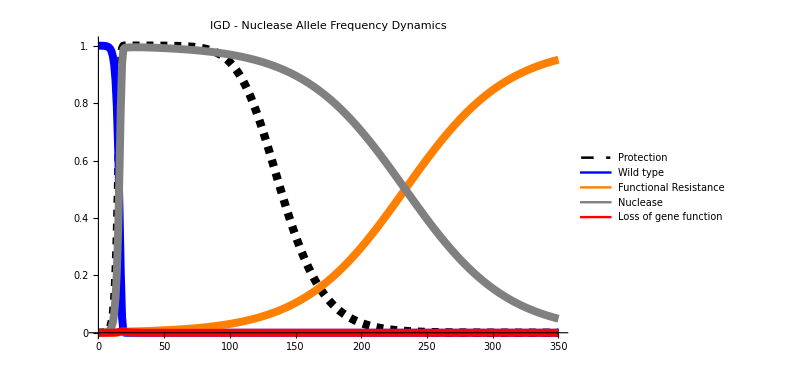

-Graphics-FrequencyTime (Generations)

```mathematica
graph=ListPlot[{Table[{t,1-vc[t](*reduction in vectorial capacity,protection*)},{t,0,tmax}],Table[{t,wild[t]},{t,0,tmax}],Table[{t,resist1[t]},{t,0,tmax}],Table[{t,nuclease[t]},{t,0,tmax}],Table[{t,resist2[t]},{t,0,tmax}]},Joined->True,PlotRange->{{0,tmax},{0,1.01}},ImageSize->600,PlotStyle->{{Thickness[.01],Black,Dashed},{Thickness[.0095],Blue},
{Thickness[.0095],Orange},{Thickness[0.0095],Gray}, {Thickness[.0095], Red}},AxesStyle->Thickness[.005],PlotRange->{{0,tmax},{0,1}},Frame->None,GridLines->None,Ticks->{Automatic,{0,.2,.4,.6,.8,1.0}},TicksStyle->Directive[Black,14], PlotLabel-> "IGD - Nuclease Allele Frequency Dynamics",LabelStyle-> Directive[Bold,Black,FontFamily->"Arial",FontSize->16], PlotLegends->{"Protection","Wild type","Functional Resistance","Nuclease","Loss of gene function"}]
Labeled[graph,{"Frequency","Time (Generations)"},{Left,Bottom },LabelStyle->Directive[Black,Bold, FontFamily->"Arial",FontSize->14],RotateLabel->True,Spacings->{1,1}]
```